True

<|λ→{eV(ϕ,-1)→ϕ(1),eV(ϕ̄,-2)→ϕ̄(2),eV(ψ,-3)→ψ(3),eV(ψ̄,-4)→ψ̄(4)},g→{eV(ϕ,-1)→ϕ(1),eV(ϕ,-3)→ϕ(2),eV(ϕ,-5)→ϕ(3),eV(ϕ̄,-2)→ϕ̄(4),eV(ϕ̄,-4)→ϕ̄(5),eV(ϕ̄,-6)→ϕ̄(6)},ϕϕb→{eV(ϕ,-1)→ϕ(1),eV(ϕ̄,-2)→ϕ̄(2)},ψψb→{eV(ψ,-1)→ψ(1),eV(ψ̄,-2)→ψ̄(2)}|>

CGTT: Running tests:

Loading graphs for symGroup {orthogonal,3} and bubble data <|ϕ→4,ψ→0,ψ̄→0|>

Loading graphs for symGroup {orthogonal,3} and bubble data <|ϕ→4,ψ→0,ψ̄→0|>

Loading graphs for symGroup {orthogonal,3} and bubble data <|ϕ→4,ψ→0,ψ̄→0|>

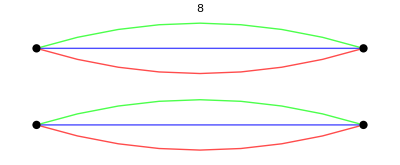
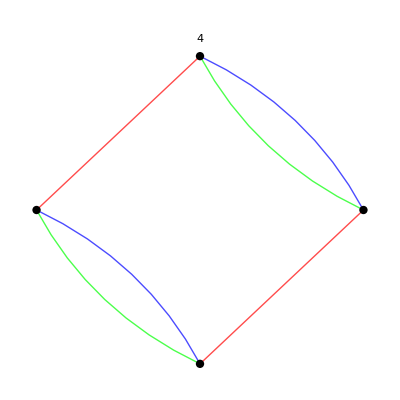
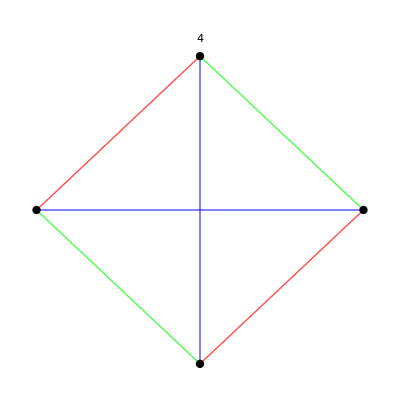
{ϕψψ̄,{-Graphics-  x 1 col perms, #CFs=6,-Graphics-  x 3 col perms, #CFs=4,-Graphics-  x 1 col perms, #CFs=3}}

Loading graphs for symGroup {orthogonal,3} and bubble data <|ϕ→2,ψ→1,ψ̄→1|>

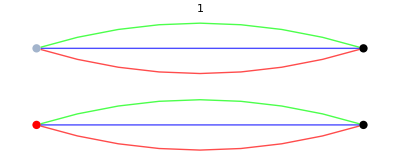
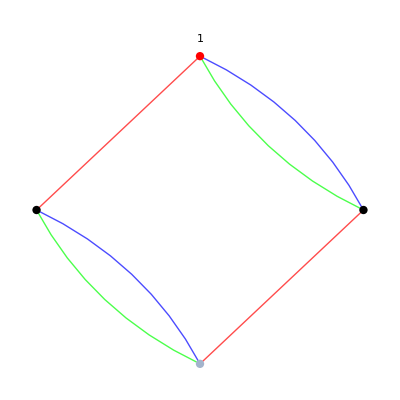
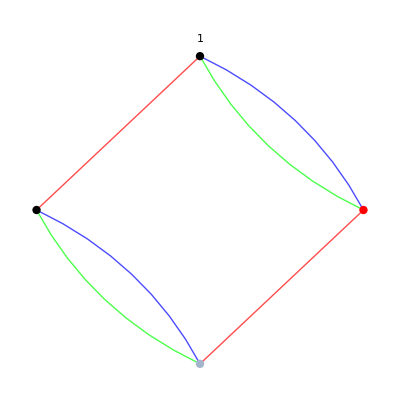
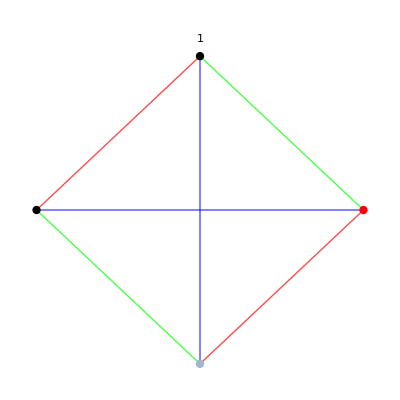
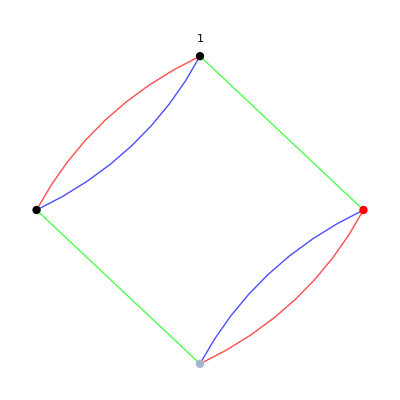
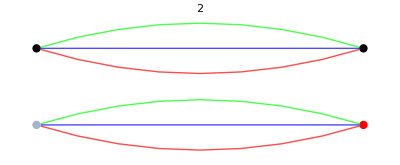
{ϕψψ̄,{-Graphics-  x 1 col perms, #CFs=6,-Graphics-  x 3 col perms, #CFs=4,-Graphics-  x 3 col perms, #CFs=4,-Graphics-  x 3 col perms, #CFs=3,-Graphics-  x 3 col perms, #CFs=4,-Graphics-  x 1 col perms, #CFs=6}}

```mathematica
homePath="~/dphil/largeNmodels/";
homePath="~/dphil/largeNmodels/";
runTestsCGTT=True
symGroup={orthogonal, 3};(*We want SO(symmetryGroupSize)*) 

gData =<|ϕ->2,ϕ̄->2|>;
λData =<|ϕ->1,ϕ̄->1,ψ->1,ψ̄-> 1|>;
hData =<|ϕ->3,ϕ̄->3|>;
phiphibarData =<|ϕ->1,ϕ̄->1|>;
psipsibarData =<|ψ->1, ψ̄ -> 1|>;
vertexData = <|g->gData, λ->λData, ϕϕb->phiphibarData,ψψb->psipsibarData, h->hData|>;
subExternalNamesForBubble=<|λ->{eV[ϕ,-1]->ϕ[1], eV[ϕ̄,-2]->ϕ̄[2], eV[ψ,-3]->ψ[3], eV[ψ̄,-4]->ψ̄[4]},
								g->{eV[ϕ,-1]->ϕ[1], eV[ϕ̄,-2]->ϕ̄[3],eV[ϕ,-3]->ϕ[2], eV[ϕ̄,-4]->ϕ̄[4]},
								ϕϕb->{eV[ϕ,-1]->ϕ[1], eV[ϕ̄,-2]->ϕ̄[2]},
								ψψb->{eV[ψ,-1]->ψ[1], eV[ψ̄,-2]->ψ̄[2]},
g->{eV[ϕ,-1]->ϕ[1],eV[ϕ,-3]->ϕ[2],eV[ϕ,-5]->ϕ[3], eV[ϕ̄,-2]->ϕ̄[4], eV[ϕ̄,-4]->ϕ̄[5],eV[ϕ̄,-6]->ϕ̄[6]}|>
allFields = Union@@Values[Keys/@vertexData];
(*{symmetryGroup,symmetryGroupSize}=symGroup;*)
NotebookEvaluate[FileNameJoin[{homePath,"ColourGrapherTwoTypes.m"}]];
NotebookEvaluate[FileNameJoin[{homePath,"colourisingDiagrams.m"}]];
Get["helpfulFunctions.m", Path->homePath];
```

```mathematica
$Assumptions=( (gT|gt|gd|gp|gdt|λT|λt|λpE|λpS|λpO|λdS|λdD|λpD|gt|gp|gd|ϵ)∈Reals) &&((N|Na|Nb|Nc) ∈ NonNegativeIntegers);
(*LijklA∈Arrays[{Na,Nb,Nc,Na,Nb,Nc,Na,Nb,Nc,Na,Nb,Nc}, Reals],(*TensorDimensions[OT]*)*)(*,(a|b|c) ∈Vectors[d,Reals],id∈Arrays[{N,N}, Reals]&&*)
(*Symbolic scalars need to be specified with assumptions*)
```

```mathematica
symSetForRk3QuadraticPhi = {{Cycles[{{1,4},{2,5},{3,6}}],1}};
(*symSetForRk3QuarticG={{Cycles[{{1,4},{2,5},{3,6}}],1}, {Cycles[{{1,4+3},{2,5+3},{3,6+3}}],1},{Cycles[{{1,4+3*2},{2,5+3*2},{3,6+3*2}}],1}};*)
symSetForRk3QuarticG={{Cycles[{{1,4},{2,5},{3,6}}],1},{Cycles[{{7,7+3},{8,8+3},{9,9+3}}],1}};
symSetForRk3QuarticLam={(*(*Not actually symmetric in Fermions:*),{Cycles[{{1+3*2,4+3*2},{2+3*2,5+3*2},{3+3*2,6+3*2}}],1}*)};
symSetForRk3QuarticG={{Cycles[{{1,1+3},{2,2+3},{3,3+3}}],1}, {Cycles[{{1,1+3*2},{2,2+3*2},{3,3+3*2}}],1}, {Cycles[{{10,10+3},{11,11+3},{12,12+3}}],1},  {Cycles[{{10,10+3*2},{11,11+3*2},{12,12+3*2}}],1}};
Id=IdentityMatrix;

generateFromPhiForm[phiform_List,IndicesAndColour_Association]:=Module[{thusObtained,tensorForm},
thusObtained=DeleteCases[KeyValueMap[Flatten@Position[Flatten[List@@#&/@phiform],#1,{1}]->#2&,IndicesAndColour],{}->a_];
(*Remove indices that don't appear from the list of indices*)
If[Union[Length[#[[1]]]&/@thusObtained]!={2},Print[thusObtained,Union[Length[#[[1]]]&/@thusObtained]];Abort[]];
tensorForm=TensorTranspose[TensorProduct@@(Id[#[[2]]]&/@thusObtained),Flatten[First/@thusObtained]];
Return@tensorForm
];
mySymmetrize[tensor_,listOfCycles:{{_Cycles,1}..}]:=Module[{expandTensor,group, order,tensorDimensions,listOfElements,symmetrised},
expandTensor=tensor//TensorExpand;
group=PermutationGroup[First/@listOfCycles];
listOfElements=GroupElements[group];
tensorDimensions=TensorDimensions[expandTensor];
(*Print[tensorDimensions];*)
If[Length@Union[Permute[tensorDimensions,#]&/@listOfElements]!= 1, Print["Permuting illegal tensor dimensions in mySymmetrize: ", tensorDimensions, " asked to be permuted by ",listOfCycles ];
Abort[]
];(*Make sure we are not symmetrising over illegal dimensions*)
order=GroupOrder[group];
symmetrised=1/order Total[TensorTranspose[expandTensor,#]&/@listOfElements]//TensorReduce;
FullSimplify[symmetrised, TimeConstraint->{1,5}]
];

mapColourNsToN={Na->eN,Nb->eN,Nc->eN};
(*
IndicesAndColour=<|a->Na,b->Nb,c->Nc,ap->Na,bp->Nb,cp->Nc|>;
OTphiform={ϕ[a,b,c],ϕ[a,bp,cp],ϕ[ap,b,cp], ϕ[ap,bp,c]};

singleOT=generateFromPhiForm[OTphiform,IndicesAndColour]
OT= mySymmetrize[singleOT, symSetForRk3QuarticG];

Odtphiform= {ϕ[a,b,c],ϕ[a,b,c],ϕ[ap,bp,cp], ϕ[ap,bp,cp]}
singleOdt=generateFromPhiForm[Odtphiform,IndicesAndColour]
Odt= mySymmetrize[singleOdt, symSetForRk3QuarticG];

Opphiforms={ {ϕ[a,b,c],ϕ[a,b,cp],ϕ[ap,bp,c], ϕ[ap,bp,cp]}, {ϕ[a,b,c],ϕ[a,bp,c],ϕ[ap,b,cp], ϕ[ap,bp,cp]}, {ϕ[a,b,c],ϕ[ap,b,c],ϕ[a,bp,cp], ϕ[ap,bp,cp]}};

singleOps=generateFromPhiForm[#,IndicesAndColour]&/@Opphiforms

Ops= mySymmetrize[#, symSetForRk3QuarticG]&/@singleOps;
Op= 1/Length[Ops] Total[Ops]//FullSimplify*)
```

```mathematica
vertexGraphsTemp = fetchVertices[#,groupByColourIso->False] & /@vertexData;
everyPossibleVertexInFullForm = Association[KeyValueMap[numberBubbles, vertexGraphsTemp]];
 everyPossibleMapAssoc =getEveryPossibleMap/@everyPossibleVertexInFullForm;
```

Loading graphs for symGroup {orthogonal,3} and bubble data <|ϕ→2,ϕ̄→2|>

Loading graphs for symGroup {orthogonal,3} and bubble data <|ϕ→1,ϕ̄→1,ψ→1,ψ̄→1|>

Loading graphs for symGroup {orthogonal,3} and bubble data <|ϕ→1,ϕ̄→1|>

Loading graphs for symGroup {orthogonal,3} and bubble data <|ψ→1,ψ̄→1|>

Loading graphs for symGroup {orthogonal,3} and bubble data <|ϕ→3,ϕ̄→3|>

```mathematica
allHookPermsWithReverser = Association[KeyValueMap[generateAllHookPermutationsWithReverser[#1, #2] &,everyPossibleVertexInFullForm]];
everyPossibleColAndHookPermOfVtx = Association[KeyValueMap[(#1->applySubNumberingToAllHookPerms[#2])&, allHookPermsWithReverser]];
```

```mathematica
Print["Gathering by isomorphic coloured multigraphs, we observe: ", 
coloredMultigraphIsomorphicGather[(#[[2]]&/@Values[everyPossibleVertexInFullForm[λ]])/.reduceHooks, λData], " and ",
coloredMultigraphIsomorphicGather[(#[[2]]&/@Values[everyPossibleVertexInFullForm[g]])/.reduceHooks, gData]];
```

Gathering by isomorphic coloured multigraphs, we observe: {{1,2,3,4,5,6},{7,8,9},{10,11,12},{13,14,15},{16,17,18},{19,20,21},{22,23,24},{25},{26},{27}} and {{1,2,3},{4,5,6},{7,8,9},{10,11,12},{13},{14}}

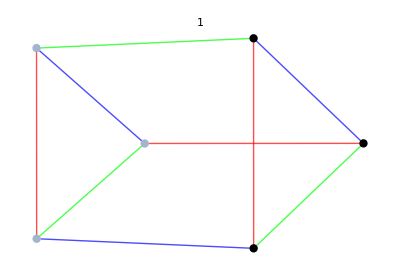
{-Graphics-,{MyGraph({α(ϕ(1))α(ϕ(2))α,α(ϕ(3))α(ϕ̄(4))α,α(ϕ̄(5))α(ϕ̄(6))α,β(ϕ(1))β(ϕ(3))β,β(ϕ(2))β(ϕ̄(5))β,β(ϕ̄(4))β(ϕ̄(6))β,γ(ϕ(1))γ(ϕ̄(6))γ,γ(ϕ(2))γ(ϕ(3))γ,γ(ϕ̄(4))γ(ϕ̄(5))γ}),1},3,1/N^3}

```mathematica
everyPossibleVertexInFullForm[h][[1]]
```

```mathematica
coloredMultigraphIsomorphicGather[(#[[2]]&/@Values[everyPossibleVertexInFullForm[h]])/.reduceHooks, gData]
```

IGraphM::bdvcol: Vertex colors: the following vertices are not in the graph: {ϕ̄(3)}.

General::stop: Further output of IGraphM::bdvcol will be suppressed during this calculation.

{{1,9,11},{2},{3},{4,5,10,12,13,14},{6,7,8},{15,21},{16,17,18,19,34,36},{20,30},{22,23,24,25,37,38},{26},{27,39,41,43},{28,29,31,32,40,42,44},{33,35},{45,46,47,51,52,53,54,55,56},{48,49,50,75,76,77,78,79,80},{57,58},{59},{60,61,62},{63,64,65,66,67,68,69,70,71,72,73,74,81,82,83,84,85,86},{87,89},{88,90,91},{92,93,94,98,99,100},{95,96,97,101,102,103,104,105,106},{107,108}}

```mathematica
kn
```

```mathematica
verticesToSFs={λ[1]->λt/(3*N^(3/2)),λ[2]->λt/(3*N^(3/2)),λ[3]->λt/(3*N^(3/2)),λ[4]->Subscript[λp,E]/(3*N^2),λ[5]->Subscript[λp,E]/(3*N^2),λ[6]->Subscript[λp,E]/(3*N^2),λ[7]->Subscript[λp,S]/(3*N^2),λ[8]->Subscript[λp,S]/(3*N^2),λ[9]->Subscript[λp,S]/(3*N^2),λ[10]->Subscript[λp,O]/(3*N^2),λ[11]->Subscript[λp,O]/(3*N^2),λ[12]->Subscript[λp,O]/(3*N^2),λ[13]->Subscript[λd,S]/N^3,λ[14]->Subscript[λd,D]/N^3,g[1]->gt/N^(3/2),g[2]->gp/(3*N^2),g[3]->gp/(3*N^2),g[4]->gp/(3*N^2),g[5]->gd/N^3};
everyColPermOfEveryVtx= {{Graph[{ϕ[1],ϕ[2],ψ[3],OverBar[ψ][4]},{UndirectedEdge[ϕ[1],ϕ[2],RGBColor[1,0,0]],UndirectedEdge[ψ[3],OverBar[ψ][4],RGBColor[1,0,0]],UndirectedEdge[ϕ[1],ψ[3],RGBColor[0,0,1]],UndirectedEdge[ϕ[2],OverBar[ψ][4],RGBColor[0,0,1]],UndirectedEdge[ϕ[1],OverBar[ψ][4],RGBColor[0,1,0]],UndirectedEdge[ϕ[2],ψ[3],RGBColor[0,1,0]]},{BaseStyle->Thickness[Large],EdgeStyle->{UndirectedEdge[ϕ[2],ψ[3],RGBColor[0,1,0]]->{RGBColor[0,1,0]},UndirectedEdge[ψ[3],OverBar[ψ][4],RGBColor[1,0,0]]->{RGBColor[1,0,0]},UndirectedEdge[ϕ[1],ψ[3],RGBColor[0,0,1]]->{RGBColor[0,0,1]},UndirectedEdge[ϕ[2],OverBar[ψ][4],RGBColor[0,0,1]]->{RGBColor[0,0,1]},UndirectedEdge[ϕ[1],OverBar[ψ][4],RGBColor[0,1,0]]->{RGBColor[0,1,0]},UndirectedEdge[ϕ[1],ϕ[2],RGBColor[1,0,0]]->{RGBColor[1,0,0]}},ImagePadding->7,PlotLabel->1,VertexShapeFunction->{{AbsolutePointSize[6],Point[#1]}&},VertexStyle->{ϕ[2]->GrayLevel[0],ψ[3]->RGBColor[1,0,0],ϕ[1]->GrayLevel[0]}}],{MyGraph[{UndirectedEdge[α[ϕ[1]],α[ϕ[2]],α],UndirectedEdge[α[ψ[3]],α[OverBar[ψ][4]],α],UndirectedEdge[β[ϕ[1]],β[ψ[3]],β],UndirectedEdge[β[ϕ[2]],β[OverBar[ψ][4]],β],UndirectedEdge[γ[ϕ[1]],γ[OverBar[ψ][4]],γ],UndirectedEdge[γ[ϕ[2]],γ[ψ[3]],γ]}],1},3,N^(-3/2)},{Graph[{ϕ[1],ψ[3],ϕ[2],OverBar[ψ][4]},{UndirectedEdge[ϕ[1],ψ[3],RGBColor[1,0,0]],UndirectedEdge[ϕ[2],OverBar[ψ][4],RGBColor[1,0,0]],UndirectedEdge[ϕ[1],ϕ[2],RGBColor[0,0,1]],UndirectedEdge[ψ[3],OverBar[ψ][4],RGBColor[0,0,1]],UndirectedEdge[ϕ[1],OverBar[ψ][4],RGBColor[0,1,0]],UndirectedEdge[ϕ[2],ψ[3],RGBColor[0,1,0]]},{BaseStyle->Thickness[Large],EdgeStyle->{UndirectedEdge[ϕ[2],ψ[3],RGBColor[0,1,0]]->{RGBColor[0,1,0]},UndirectedEdge[ϕ[1],ϕ[2],RGBColor[0,0,1]]->{RGBColor[0,0,1]},UndirectedEdge[ϕ[1],ψ[3],RGBColor[1,0,0]]->{RGBColor[1,0,0]},UndirectedEdge[ϕ[1],OverBar[ψ][4],RGBColor[0,1,0]]->{RGBColor[0,1,0]},UndirectedEdge[ϕ[2],OverBar[ψ][4],RGBColor[1,0,0]]->{RGBColor[1,0,0]},UndirectedEdge[ψ[3],OverBar[ψ][4],RGBColor[0,0,1]]->{RGBColor[0,0,1]}},ImagePadding->7,PlotLabel->1,VertexShapeFunction->{{AbsolutePointSize[6],Point[#1]}&},VertexStyle->{ϕ[2]->GrayLevel[0],ψ[3]->RGBColor[1,0,0],ϕ[1]->GrayLevel[0]}}],{MyGraph[{UndirectedEdge[α[ϕ[1]],α[ψ[3]],α],UndirectedEdge[α[ϕ[2]],α[OverBar[ψ][4]],α],UndirectedEdge[β[ϕ[1]],β[ϕ[2]],β],UndirectedEdge[β[ψ[3]],β[OverBar[ψ][4]],β],UndirectedEdge[γ[ϕ[1]],γ[OverBar[ψ][4]],γ],UndirectedEdge[γ[ϕ[2]],γ[ψ[3]],γ]}],1},3,N^(-3/2)},{Graph[{ϕ[1],ψ[3],ϕ[2],OverBar[ψ][4]},{UndirectedEdge[ϕ[1],ψ[3],RGBColor[1,0,0]],UndirectedEdge[ϕ[2],OverBar[ψ][4],RGBColor[1,0,0]],UndirectedEdge[ϕ[1],OverBar[ψ][4],RGBColor[0,0,1]],UndirectedEdge[ϕ[2],ψ[3],RGBColor[0,0,1]],UndirectedEdge[ϕ[1],ϕ[2],RGBColor[0,1,0]],UndirectedEdge[ψ[3],OverBar[ψ][4],RGBColor[0,1,0]]},{BaseStyle->Thickness[Large],EdgeStyle->{UndirectedEdge[ϕ[1],OverBar[ψ][4],RGBColor[0,0,1]]->{RGBColor[0,0,1]},UndirectedEdge[ϕ[2],ψ[3],RGBColor[0,0,1]]->{RGBColor[0,0,1]},UndirectedEdge[ϕ[1],ψ[3],RGBColor[1,0,0]]->{RGBColor[1,0,0]},UndirectedEdge[ϕ[1],ϕ[2],RGBColor[0,1,0]]->{RGBColor[0,1,0]},UndirectedEdge[ϕ[2],OverBar[ψ][4],RGBColor[1,0,0]]->{RGBColor[1,0,0]},UndirectedEdge[ψ[3],OverBar[ψ][4],RGBColor[0,1,0]]->{RGBColor[0,1,0]}},ImagePadding->7,PlotLabel->1,VertexShapeFunction->{{AbsolutePointSize[6],Point[#1]}&},VertexStyle->{ϕ[2]->GrayLevel[0],ψ[3]->RGBColor[1,0,0],ϕ[1]->GrayLevel[0]}}],{MyGraph[{UndirectedEdge[α[ϕ[1]],α[ψ[3]],α],UndirectedEdge[α[ϕ[2]],α[OverBar[ψ][4]],α],UndirectedEdge[β[ϕ[1]],β[OverBar[ψ][4]],β],UndirectedEdge[β[ϕ[2]],β[ψ[3]],β],UndirectedEdge[γ[ϕ[1]],γ[ϕ[2]],γ],UndirectedEdge[γ[ψ[3]],γ[OverBar[ψ][4]],γ]}],1},3,N^(-3/2)},{Graph[{ϕ[1],ϕ[2],ψ[3],OverBar[ψ][4]},{UndirectedEdge[ϕ[1],ϕ[2],RGBColor[1,0,0]],UndirectedEdge[ψ[3],OverBar[ψ][4],RGBColor[1,0,0]],UndirectedEdge[ϕ[1],ϕ[2],RGBColor[0,0,1]],UndirectedEdge[ψ[3],OverBar[ψ][4],RGBColor[0,0,1]],UndirectedEdge[ϕ[1],OverBar[ψ][4],RGBColor[0,1,0]],UndirectedEdge[ϕ[2],ψ[3],RGBColor[0,1,0]]},{BaseStyle->Thickness[Large],EdgeStyle->{UndirectedEdge[ϕ[2],ψ[3],RGBColor[0,1,0]]->{RGBColor[0,1,0]},UndirectedEdge[ϕ[1],ϕ[2],RGBColor[0,0,1]]->{RGBColor[0,0,1]},UndirectedEdge[ψ[3],OverBar[ψ][4],RGBColor[1,0,0]]->{RGBColor[1,0,0]},UndirectedEdge[ϕ[1],OverBar[ψ][4],RGBColor[0,1,0]]->{RGBColor[0,1,0]},UndirectedEdge[ϕ[1],ϕ[2],RGBColor[1,0,0]]->{RGBColor[1,0,0]},UndirectedEdge[ψ[3],OverBar[ψ][4],RGBColor[0,0,1]]->{RGBColor[0,0,1]}},ImagePadding->7,PlotLabel->1,VertexShapeFunction->{{AbsolutePointSize[6],Point[#1]}&},VertexStyle->{ϕ[2]->GrayLevel[0],ψ[3]->RGBColor[1,0,0],ϕ[1]->GrayLevel[0]}}],{MyGraph[{UndirectedEdge[α[ϕ[1]],α[ϕ[2]],α],UndirectedEdge[α[ψ[3]],α[OverBar[ψ][4]],α],UndirectedEdge[β[ϕ[1]],β[ϕ[2]],β],UndirectedEdge[β[ψ[3]],β[OverBar[ψ][4]],β],UndirectedEdge[γ[ϕ[1]],γ[OverBar[ψ][4]],γ],UndirectedEdge[γ[ϕ[2]],γ[ψ[3]],γ]}],1},4,N^(-2)},{Graph[{ϕ[1],ϕ[2],ψ[3],OverBar[ψ][4]},{UndirectedEdge[ϕ[1],ϕ[2],RGBColor[1,0,0]],UndirectedEdge[ψ[3],OverBar[ψ][4],RGBColor[1,0,0]],UndirectedEdge[ϕ[1],OverBar[ψ][4],RGBColor[0,0,1]],UndirectedEdge[ϕ[2],ψ[3],RGBColor[0,0,1]],UndirectedEdge[ϕ[1],ϕ[2],RGBColor[0,1,0]],UndirectedEdge[ψ[3],OverBar[ψ][4],RGBColor[0,1,0]]},{BaseStyle->Thickness[Large],EdgeStyle->{UndirectedEdge[ϕ[1],OverBar[ψ][4],RGBColor[0,0,1]]->{RGBColor[0,0,1]},UndirectedEdge[ϕ[2],ψ[3],RGBColor[0,0,1]]->{RGBColor[0,0,1]},UndirectedEdge[ϕ[1],ϕ[2],RGBColor[0,1,0]]->{RGBColor[0,1,0]},UndirectedEdge[ψ[3],OverBar[ψ][4],RGBColor[1,0,0]]->{RGBColor[1,0,0]},UndirectedEdge[ϕ[1],ϕ[2],RGBColor[1,0,0]]->{RGBColor[1,0,0]},UndirectedEdge[ψ[3],OverBar[ψ][4],RGBColor[0,1,0]]->{RGBColor[0,1,0]}},ImagePadding->7,PlotLabel->1,VertexShapeFunction->{{AbsolutePointSize[6],Point[#1]}&},VertexStyle->{ϕ[2]->GrayLevel[0],ψ[3]->RGBColor[1,0,0],ϕ[1]->GrayLevel[0]}}],{MyGraph[{UndirectedEdge[α[ϕ[1]],α[ϕ[2]],α],UndirectedEdge[α[ψ[3]],α[OverBar[ψ][4]],α],UndirectedEdge[β[ϕ[1]],β[OverBar[ψ][4]],β],UndirectedEdge[β[ϕ[2]],β[ψ[3]],β],UndirectedEdge[γ[ϕ[1]],γ[ϕ[2]],γ],UndirectedEdge[γ[ψ[3]],γ[OverBar[ψ][4]],γ]}],1},4,N^(-2)},{Graph[{ϕ[1],OverBar[ψ][4],ϕ[2],ψ[3]},{UndirectedEdge[ϕ[1],OverBar[ψ][4],RGBColor[1,0,0]],UndirectedEdge[ϕ[2],ψ[3],RGBColor[1,0,0]],UndirectedEdge[ϕ[1],ϕ[2],RGBColor[0,0,1]],UndirectedEdge[ψ[3],OverBar[ψ][4],RGBColor[0,0,1]],UndirectedEdge[ϕ[1],ϕ[2],RGBColor[0,1,0]],UndirectedEdge[ψ[3],OverBar[ψ][4],RGBColor[0,1,0]]},{BaseStyle->Thickness[Large],EdgeStyle->{UndirectedEdge[ϕ[1],OverBar[ψ][4],RGBColor[1,0,0]]->{RGBColor[1,0,0]},UndirectedEdge[ϕ[1],ϕ[2],RGBColor[0,0,1]]->{RGBColor[0,0,1]},UndirectedEdge[ϕ[2],ψ[3],RGBColor[1,0,0]]->{RGBColor[1,0,0]},UndirectedEdge[ϕ[1],ϕ[2],RGBColor[0,1,0]]->{RGBColor[0,1,0]},UndirectedEdge[ψ[3],OverBar[ψ][4],RGBColor[0,1,0]]->{RGBColor[0,1,0]},UndirectedEdge[ψ[3],OverBar[ψ][4],RGBColor[0,0,1]]->{RGBColor[0,0,1]}},ImagePadding->7,PlotLabel->1,VertexShapeFunction->{{AbsolutePointSize[6],Point[#1]}&},VertexStyle->{ϕ[2]->GrayLevel[0],ψ[3]->RGBColor[1,0,0],ϕ[1]->GrayLevel[0]}}],{MyGraph[{UndirectedEdge[α[ϕ[1]],α[OverBar[ψ][4]],α],UndirectedEdge[α[ϕ[2]],α[ψ[3]],α],UndirectedEdge[β[ϕ[1]],β[ϕ[2]],β],UndirectedEdge[β[ψ[3]],β[OverBar[ψ][4]],β],UndirectedEdge[γ[ϕ[1]],γ[ϕ[2]],γ],UndirectedEdge[γ[ψ[3]],γ[OverBar[ψ][4]],γ]}],1},4,N^(-2)},{Graph[{ϕ[1],ϕ[2],ψ[3],OverBar[ψ][4]},{UndirectedEdge[ϕ[1],ϕ[2],RGBColor[1,0,0]],UndirectedEdge[ψ[3],OverBar[ψ][4],RGBColor[1,0,0]],UndirectedEdge[ϕ[1],OverBar[ψ][4],RGBColor[0,0,1]],UndirectedEdge[ϕ[2],ψ[3],RGBColor[0,0,1]],UndirectedEdge[ϕ[1],OverBar[ψ][4],RGBColor[0,1,0]],UndirectedEdge[ϕ[2],ψ[3],RGBColor[0,1,0]]},{BaseStyle->Thickness[Large],EdgeStyle->{UndirectedEdge[ϕ[1],OverBar[ψ][4],RGBColor[0,0,1]]->{RGBColor[0,0,1]},UndirectedEdge[ϕ[2],ψ[3],RGBColor[0,0,1]]->{RGBColor[0,0,1]},UndirectedEdge[ϕ[2],ψ[3],RGBColor[0,1,0]]->{RGBColor[0,1,0]},UndirectedEdge[ψ[3],OverBar[ψ][4],RGBColor[1,0,0]]->{RGBColor[1,0,0]},UndirectedEdge[ϕ[1],OverBar[ψ][4],RGBColor[0,1,0]]->{RGBColor[0,1,0]},UndirectedEdge[ϕ[1],ϕ[2],RGBColor[1,0,0]]->{RGBColor[1,0,0]}},ImagePadding->7,PlotLabel->1,VertexShapeFunction->{{AbsolutePointSize[6],Point[#1]}&},VertexStyle->{ϕ[2]->GrayLevel[0],ψ[3]->RGBColor[1,0,0],ϕ[1]->GrayLevel[0]}}],{MyGraph[{UndirectedEdge[α[ϕ[1]],α[ϕ[2]],α],UndirectedEdge[α[ψ[3]],α[OverBar[ψ][4]],α],UndirectedEdge[β[ϕ[1]],β[OverBar[ψ][4]],β],UndirectedEdge[β[ϕ[2]],β[ψ[3]],β],UndirectedEdge[γ[ϕ[1]],γ[OverBar[ψ][4]],γ],UndirectedEdge[γ[ϕ[2]],γ[ψ[3]],γ]}],1},4,N^(-2)},{Graph[{ϕ[1],OverBar[ψ][4],ϕ[2],ψ[3]},{UndirectedEdge[ϕ[1],OverBar[ψ][4],RGBColor[1,0,0]],UndirectedEdge[ϕ[2],ψ[3],RGBColor[1,0,0]],UndirectedEdge[ϕ[1],ϕ[2],RGBColor[0,0,1]],UndirectedEdge[ψ[3],OverBar[ψ][4],RGBColor[0,0,1]],UndirectedEdge[ϕ[1],OverBar[ψ][4],RGBColor[0,1,0]],UndirectedEdge[ϕ[2],ψ[3],RGBColor[0,1,0]]},{BaseStyle->Thickness[Large],EdgeStyle->{UndirectedEdge[ϕ[1],OverBar[ψ][4],RGBColor[1,0,0]]->{RGBColor[1,0,0]},UndirectedEdge[ϕ[2],ψ[3],RGBColor[0,1,0]]->{RGBColor[0,1,0]},UndirectedEdge[ϕ[1],ϕ[2],RGBColor[0,0,1]]->{RGBColor[0,0,1]},UndirectedEdge[ϕ[2],ψ[3],RGBColor[1,0,0]]->{RGBColor[1,0,0]},UndirectedEdge[ϕ[1],OverBar[ψ][4],RGBColor[0,1,0]]->{RGBColor[0,1,0]},UndirectedEdge[ψ[3],OverBar[ψ][4],RGBColor[0,0,1]]->{RGBColor[0,0,1]}},ImagePadding->7,PlotLabel->1,VertexShapeFunction->{{AbsolutePointSize[6],Point[#1]}&},VertexStyle->{ϕ[2]->GrayLevel[0],ψ[3]->RGBColor[1,0,0],ϕ[1]->GrayLevel[0]}}],{MyGraph[{UndirectedEdge[α[ϕ[1]],α[OverBar[ψ][4]],α],UndirectedEdge[α[ϕ[2]],α[ψ[3]],α],UndirectedEdge[β[ϕ[1]],β[ϕ[2]],β],UndirectedEdge[β[ψ[3]],β[OverBar[ψ][4]],β],UndirectedEdge[γ[ϕ[1]],γ[OverBar[ψ][4]],γ],UndirectedEdge[γ[ϕ[2]],γ[ψ[3]],γ]}],1},4,N^(-2)},{Graph[{ϕ[1],OverBar[ψ][4],ϕ[2],ψ[3]},{UndirectedEdge[ϕ[1],OverBar[ψ][4],RGBColor[1,0,0]],UndirectedEdge[ϕ[2],ψ[3],RGBColor[1,0,0]],UndirectedEdge[ϕ[1],OverBar[ψ][4],RGBColor[0,0,1]],UndirectedEdge[ϕ[2],ψ[3],RGBColor[0,0,1]],UndirectedEdge[ϕ[1],ϕ[2],RGBColor[0,1,0]],UndirectedEdge[ψ[3],OverBar[ψ][4],RGBColor[0,1,0]]},{BaseStyle->Thickness[Large],EdgeStyle->{UndirectedEdge[ϕ[1],OverBar[ψ][4],RGBColor[0,0,1]]->{RGBColor[0,0,1]},UndirectedEdge[ϕ[1],OverBar[ψ][4],RGBColor[1,0,0]]->{RGBColor[1,0,0]},UndirectedEdge[ϕ[2],ψ[3],RGBColor[0,0,1]]->{RGBColor[0,0,1]},UndirectedEdge[ϕ[2],ψ[3],RGBColor[1,0,0]]->{RGBColor[1,0,0]},UndirectedEdge[ϕ[1],ϕ[2],RGBColor[0,1,0]]->{RGBColor[0,1,0]},UndirectedEdge[ψ[3],OverBar[ψ][4],RGBColor[0,1,0]]->{RGBColor[0,1,0]}},ImagePadding->7,PlotLabel->1,VertexShapeFunction->{{AbsolutePointSize[6],Point[#1]}&},VertexStyle->{ϕ[2]->GrayLevel[0],ψ[3]->RGBColor[1,0,0],ϕ[1]->GrayLevel[0]}}],{MyGraph[{UndirectedEdge[α[ϕ[1]],α[OverBar[ψ][4]],α],UndirectedEdge[α[ϕ[2]],α[ψ[3]],α],UndirectedEdge[β[ϕ[1]],β[OverBar[ψ][4]],β],UndirectedEdge[β[ϕ[2]],β[ψ[3]],β],UndirectedEdge[γ[ϕ[1]],γ[ϕ[2]],γ],UndirectedEdge[γ[ψ[3]],γ[OverBar[ψ][4]],γ]}],1},4,N^(-2)},{Graph[{ϕ[1],ψ[3],ϕ[2],OverBar[ψ][4]},{UndirectedEdge[ϕ[1],ψ[3],RGBColor[1,0,0]],UndirectedEdge[ϕ[2],OverBar[ψ][4],RGBColor[1,0,0]],UndirectedEdge[ϕ[1],OverBar[ψ][4],RGBColor[0,0,1]],UndirectedEdge[ϕ[2],ψ[3],RGBColor[0,0,1]],UndirectedEdge[ϕ[1],OverBar[ψ][4],RGBColor[0,1,0]],UndirectedEdge[ϕ[2],ψ[3],RGBColor[0,1,0]]},{BaseStyle->Thickness[Large],EdgeStyle->{UndirectedEdge[ϕ[1],OverBar[ψ][4],RGBColor[0,0,1]]->{RGBColor[0,0,1]},UndirectedEdge[ϕ[2],ψ[3],RGBColor[0,0,1]]->{RGBColor[0,0,1]},UndirectedEdge[ϕ[2],ψ[3],RGBColor[0,1,0]]->{RGBColor[0,1,0]},UndirectedEdge[ϕ[1],ψ[3],RGBColor[1,0,0]]->{RGBColor[1,0,0]},UndirectedEdge[ϕ[1],OverBar[ψ][4],RGBColor[0,1,0]]->{RGBColor[0,1,0]},UndirectedEdge[ϕ[2],OverBar[ψ][4],RGBColor[1,0,0]]->{RGBColor[1,0,0]}},ImagePadding->7,PlotLabel->1,VertexShapeFunction->{{AbsolutePointSize[6],Point[#1]}&},VertexStyle->{ϕ[2]->GrayLevel[0],ψ[3]->RGBColor[1,0,0],ϕ[1]->GrayLevel[0]}}],{MyGraph[{UndirectedEdge[α[ϕ[1]],α[ψ[3]],α],UndirectedEdge[α[ϕ[2]],α[OverBar[ψ][4]],α],UndirectedEdge[β[ϕ[1]],β[OverBar[ψ][4]],β],UndirectedEdge[β[ϕ[2]],β[ψ[3]],β],UndirectedEdge[γ[ϕ[1]],γ[OverBar[ψ][4]],γ],UndirectedEdge[γ[ϕ[2]],γ[ψ[3]],γ]}],1},4,N^(-2)},{Graph[{ϕ[1],OverBar[ψ][4],ϕ[2],ψ[3]},{UndirectedEdge[ϕ[1],OverBar[ψ][4],RGBColor[1,0,0]],UndirectedEdge[ϕ[2],ψ[3],RGBColor[1,0,0]],UndirectedEdge[ϕ[1],ψ[3],RGBColor[0,0,1]],UndirectedEdge[ϕ[2],OverBar[ψ][4],RGBColor[0,0,1]],UndirectedEdge[ϕ[1],OverBar[ψ][4],RGBColor[0,1,0]],UndirectedEdge[ϕ[2],ψ[3],RGBColor[0,1,0]]},{BaseStyle->Thickness[Large],EdgeStyle->{UndirectedEdge[ϕ[1],OverBar[ψ][4],RGBColor[1,0,0]]->{RGBColor[1,0,0]},UndirectedEdge[ϕ[2],ψ[3],RGBColor[0,1,0]]->{RGBColor[0,1,0]},UndirectedEdge[ϕ[2],ψ[3],RGBColor[1,0,0]]->{RGBColor[1,0,0]},UndirectedEdge[ϕ[1],ψ[3],RGBColor[0,0,1]]->{RGBColor[0,0,1]},UndirectedEdge[ϕ[2],OverBar[ψ][4],RGBColor[0,0,1]]->{RGBColor[0,0,1]},UndirectedEdge[ϕ[1],OverBar[ψ][4],RGBColor[0,1,0]]->{RGBColor[0,1,0]}},ImagePadding->7,PlotLabel->1,VertexShapeFunction->{{AbsolutePointSize[6],Point[#1]}&},VertexStyle->{ϕ[2]->GrayLevel[0],ψ[3]->RGBColor[1,0,0],ϕ[1]->GrayLevel[0]}}],{MyGraph[{UndirectedEdge[α[ϕ[1]],α[OverBar[ψ][4]],α],UndirectedEdge[α[ϕ[2]],α[ψ[3]],α],UndirectedEdge[β[ϕ[1]],β[ψ[3]],β],UndirectedEdge[β[ϕ[2]],β[OverBar[ψ][4]],β],UndirectedEdge[γ[ϕ[1]],γ[OverBar[ψ][4]],γ],UndirectedEdge[γ[ϕ[2]],γ[ψ[3]],γ]}],1},4,N^(-2)},{Graph[{ϕ[1],ψ[3],ϕ[2],OverBar[ψ][4]},{UndirectedEdge[ϕ[1],ψ[3],RGBColor[1,0,0]],UndirectedEdge[ϕ[2],OverBar[ψ][4],RGBColor[1,0,0]],UndirectedEdge[ϕ[1],ψ[3],RGBColor[0,0,1]],UndirectedEdge[ϕ[2],OverBar[ψ][4],RGBColor[0,0,1]],UndirectedEdge[ϕ[1],OverBar[ψ][4],RGBColor[0,1,0]],UndirectedEdge[ϕ[2],ψ[3],RGBColor[0,1,0]]},{BaseStyle->Thickness[Large],EdgeStyle->{UndirectedEdge[ϕ[2],ψ[3],RGBColor[0,1,0]]->{RGBColor[0,1,0]},UndirectedEdge[ϕ[1],ψ[3],RGBColor[1,0,0]]->{RGBColor[1,0,0]},UndirectedEdge[ϕ[1],ψ[3],RGBColor[0,0,1]]->{RGBColor[0,0,1]},UndirectedEdge[ϕ[2],OverBar[ψ][4],RGBColor[0,0,1]]->{RGBColor[0,0,1]},UndirectedEdge[ϕ[1],OverBar[ψ][4],RGBColor[0,1,0]]->{RGBColor[0,1,0]},UndirectedEdge[ϕ[2],OverBar[ψ][4],RGBColor[1,0,0]]->{RGBColor[1,0,0]}},ImagePadding->7,PlotLabel->1,VertexShapeFunction->{{AbsolutePointSize[6],Point[#1]}&},VertexStyle->{ϕ[2]->GrayLevel[0],ψ[3]->RGBColor[1,0,0],ϕ[1]->GrayLevel[0]}}],{MyGraph[{UndirectedEdge[α[ϕ[1]],α[ψ[3]],α],UndirectedEdge[α[ϕ[2]],α[OverBar[ψ][4]],α],UndirectedEdge[β[ϕ[1]],β[ψ[3]],β],UndirectedEdge[β[ϕ[2]],β[OverBar[ψ][4]],β],UndirectedEdge[γ[ϕ[1]],γ[OverBar[ψ][4]],γ],UndirectedEdge[γ[ϕ[2]],γ[ψ[3]],γ]}],1},4,N^(-2)},{Graph[{ϕ[1],ϕ[2],ψ[3],OverBar[ψ][4]},{UndirectedEdge[ϕ[1],ϕ[2],RGBColor[1,0,0]],UndirectedEdge[ψ[3],OverBar[ψ][4],RGBColor[1,0,0]],UndirectedEdge[ϕ[1],ϕ[2],RGBColor[0,0,1]],UndirectedEdge[ψ[3],OverBar[ψ][4],RGBColor[0,0,1]],UndirectedEdge[ϕ[1],ϕ[2],RGBColor[0,1,0]],UndirectedEdge[ψ[3],OverBar[ψ][4],RGBColor[0,1,0]]},{BaseStyle->Thickness[Large],EdgeStyle->{UndirectedEdge[ϕ[1],ϕ[2],RGBColor[0,0,1]]->{RGBColor[0,0,1]},UndirectedEdge[ϕ[1],ϕ[2],RGBColor[0,1,0]]->{RGBColor[0,1,0]},UndirectedEdge[ψ[3],OverBar[ψ][4],RGBColor[1,0,0]]->{RGBColor[1,0,0]},UndirectedEdge[ϕ[1],ϕ[2],RGBColor[1,0,0]]->{RGBColor[1,0,0]},UndirectedEdge[ψ[3],OverBar[ψ][4],RGBColor[0,1,0]]->{RGBColor[0,1,0]},UndirectedEdge[ψ[3],OverBar[ψ][4],RGBColor[0,0,1]]->{RGBColor[0,0,1]}},ImagePadding->7,PlotLabel->2,VertexShapeFunction->{{AbsolutePointSize[6],Point[#1]}&},VertexStyle->{ϕ[2]->GrayLevel[0],ψ[3]->RGBColor[1,0,0],ϕ[1]->GrayLevel[0]}}],{MyGraph[{UndirectedEdge[α[ϕ[1]],α[ϕ[2]],α],UndirectedEdge[α[ψ[3]],α[OverBar[ψ][4]],α],UndirectedEdge[β[ϕ[1]],β[ϕ[2]],β],UndirectedEdge[β[ψ[3]],β[OverBar[ψ][4]],β],UndirectedEdge[γ[ϕ[1]],γ[ϕ[2]],γ],UndirectedEdge[γ[ψ[3]],γ[OverBar[ψ][4]],γ]}],2},6,N^(-3)},{Graph[{ϕ[1],OverBar[ψ][4],ϕ[2],ψ[3]},{UndirectedEdge[ϕ[1],OverBar[ψ][4],RGBColor[1,0,0]],UndirectedEdge[ϕ[2],ψ[3],RGBColor[1,0,0]],UndirectedEdge[ϕ[1],OverBar[ψ][4],RGBColor[0,0,1]],UndirectedEdge[ϕ[2],ψ[3],RGBColor[0,0,1]],UndirectedEdge[ϕ[1],OverBar[ψ][4],RGBColor[0,1,0]],UndirectedEdge[ϕ[2],ψ[3],RGBColor[0,1,0]]},{BaseStyle->Thickness[Large],EdgeStyle->{UndirectedEdge[ϕ[1],OverBar[ψ][4],RGBColor[0,0,1]]->{RGBColor[0,0,1]},UndirectedEdge[ϕ[1],OverBar[ψ][4],RGBColor[1,0,0]]->{RGBColor[1,0,0]},UndirectedEdge[ϕ[2],ψ[3],RGBColor[0,0,1]]->{RGBColor[0,0,1]},UndirectedEdge[ϕ[2],ψ[3],RGBColor[0,1,0]]->{RGBColor[0,1,0]},UndirectedEdge[ϕ[2],ψ[3],RGBColor[1,0,0]]->{RGBColor[1,0,0]},UndirectedEdge[ϕ[1],OverBar[ψ][4],RGBColor[0,1,0]]->{RGBColor[0,1,0]}},ImagePadding->7,PlotLabel->1,VertexShapeFunction->{{AbsolutePointSize[6],Point[#1]}&},VertexStyle->{ϕ[2]->GrayLevel[0],ψ[3]->RGBColor[1,0,0],ϕ[1]->GrayLevel[0]}}],{MyGraph[{UndirectedEdge[α[ϕ[1]],α[OverBar[ψ][4]],α],UndirectedEdge[α[ϕ[2]],α[ψ[3]],α],UndirectedEdge[β[ϕ[1]],β[OverBar[ψ][4]],β],UndirectedEdge[β[ϕ[2]],β[ψ[3]],β],UndirectedEdge[γ[ϕ[1]],γ[OverBar[ψ][4]],γ],UndirectedEdge[γ[ϕ[2]],γ[ψ[3]],γ]}],1},6,N^(-3)},{Graph[{ϕ[1],ϕ[2],ϕ[3],ϕ[4]},{UndirectedEdge[ϕ[1],ϕ[2],RGBColor[1,0,0]],UndirectedEdge[ϕ[3],ϕ[4],RGBColor[1,0,0]],UndirectedEdge[ϕ[1],ϕ[3],RGBColor[0,0,1]],UndirectedEdge[ϕ[2],ϕ[4],RGBColor[0,0,1]],UndirectedEdge[ϕ[1],ϕ[4],RGBColor[0,1,0]],UndirectedEdge[ϕ[2],ϕ[3],RGBColor[0,1,0]]},{BaseStyle->Thickness[Large],EdgeStyle->{UndirectedEdge[ϕ[2],ϕ[4],RGBColor[0,0,1]]->{RGBColor[0,0,1]},UndirectedEdge[ϕ[1],ϕ[4],RGBColor[0,1,0]]->{RGBColor[0,1,0]},UndirectedEdge[ϕ[2],ϕ[3],RGBColor[0,1,0]]->{RGBColor[0,1,0]},UndirectedEdge[ϕ[1],ϕ[2],RGBColor[1,0,0]]->{RGBColor[1,0,0]},UndirectedEdge[ϕ[1],ϕ[3],RGBColor[0,0,1]]->{RGBColor[0,0,1]},UndirectedEdge[ϕ[3],ϕ[4],RGBColor[1,0,0]]->{RGBColor[1,0,0]}},ImagePadding->7,PlotLabel->4,VertexShapeFunction->{{AbsolutePointSize[6],Point[#1]}&},VertexStyle->{ϕ[2]->GrayLevel[0],ϕ[1]->GrayLevel[0],ϕ[3]->GrayLevel[0],ϕ[4]->GrayLevel[0]}}],{MyGraph[{UndirectedEdge[α[ϕ[1]],α[ϕ[2]],α],UndirectedEdge[α[ϕ[3]],α[ϕ[4]],α],UndirectedEdge[β[ϕ[1]],β[ϕ[3]],β],UndirectedEdge[β[ϕ[2]],β[ϕ[4]],β],UndirectedEdge[γ[ϕ[1]],γ[ϕ[4]],γ],UndirectedEdge[γ[ϕ[2]],γ[ϕ[3]],γ]}],4},3,N^(-3/2)},{Graph[{ϕ[1],ϕ[3],ϕ[2],ϕ[4]},{UndirectedEdge[ϕ[1],ϕ[3],RGBColor[1,0,0]],UndirectedEdge[ϕ[2],ϕ[4],RGBColor[1,0,0]],UndirectedEdge[ϕ[1],ϕ[4],RGBColor[0,0,1]],UndirectedEdge[ϕ[2],ϕ[3],RGBColor[0,0,1]],UndirectedEdge[ϕ[1],ϕ[4],RGBColor[0,1,0]],UndirectedEdge[ϕ[2],ϕ[3],RGBColor[0,1,0]]},{BaseStyle->Thickness[Large],EdgeStyle->{UndirectedEdge[ϕ[1],ϕ[3],RGBColor[1,0,0]]->{RGBColor[1,0,0]},UndirectedEdge[ϕ[1],ϕ[4],RGBColor[0,1,0]]->{RGBColor[0,1,0]},UndirectedEdge[ϕ[2],ϕ[3],RGBColor[0,0,1]]->{RGBColor[0,0,1]},UndirectedEdge[ϕ[2],ϕ[3],RGBColor[0,1,0]]->{RGBColor[0,1,0]},UndirectedEdge[ϕ[1],ϕ[4],RGBColor[0,0,1]]->{RGBColor[0,0,1]},UndirectedEdge[ϕ[2],ϕ[4],RGBColor[1,0,0]]->{RGBColor[1,0,0]}},ImagePadding->7,PlotLabel->4,VertexShapeFunction->{{AbsolutePointSize[6],Point[#1]}&},VertexStyle->{ϕ[2]->GrayLevel[0],ϕ[1]->GrayLevel[0],ϕ[3]->GrayLevel[0],ϕ[4]->GrayLevel[0]}}],{MyGraph[{UndirectedEdge[α[ϕ[1]],α[ϕ[3]],α],UndirectedEdge[α[ϕ[2]],α[ϕ[4]],α],UndirectedEdge[β[ϕ[1]],β[ϕ[4]],β],UndirectedEdge[β[ϕ[2]],β[ϕ[3]],β],UndirectedEdge[γ[ϕ[1]],γ[ϕ[4]],γ],UndirectedEdge[γ[ϕ[2]],γ[ϕ[3]],γ]}],4},4,N^(-2)},{Graph[{ϕ[1],ϕ[4],ϕ[2],ϕ[3]},{UndirectedEdge[ϕ[1],ϕ[4],RGBColor[1,0,0]],UndirectedEdge[ϕ[2],ϕ[3],RGBColor[1,0,0]],UndirectedEdge[ϕ[1],ϕ[3],RGBColor[0,0,1]],UndirectedEdge[ϕ[2],ϕ[4],RGBColor[0,0,1]],UndirectedEdge[ϕ[1],ϕ[4],RGBColor[0,1,0]],UndirectedEdge[ϕ[2],ϕ[3],RGBColor[0,1,0]]},{BaseStyle->Thickness[Large],EdgeStyle->{UndirectedEdge[ϕ[2],ϕ[4],RGBColor[0,0,1]]->{RGBColor[0,0,1]},UndirectedEdge[ϕ[1],ϕ[4],RGBColor[0,1,0]]->{RGBColor[0,1,0]},UndirectedEdge[ϕ[2],ϕ[3],RGBColor[0,1,0]]->{RGBColor[0,1,0]},UndirectedEdge[ϕ[1],ϕ[3],RGBColor[0,0,1]]->{RGBColor[0,0,1]},UndirectedEdge[ϕ[2],ϕ[3],RGBColor[1,0,0]]->{RGBColor[1,0,0]},UndirectedEdge[ϕ[1],ϕ[4],RGBColor[1,0,0]]->{RGBColor[1,0,0]}},ImagePadding->7,PlotLabel->4,VertexShapeFunction->{{AbsolutePointSize[6],Point[#1]}&},VertexStyle->{ϕ[2]->GrayLevel[0],ϕ[1]->GrayLevel[0],ϕ[3]->GrayLevel[0],ϕ[4]->GrayLevel[0]}}],{MyGraph[{UndirectedEdge[α[ϕ[1]],α[ϕ[4]],α],UndirectedEdge[α[ϕ[2]],α[ϕ[3]],α],UndirectedEdge[β[ϕ[1]],β[ϕ[3]],β],UndirectedEdge[β[ϕ[2]],β[ϕ[4]],β],UndirectedEdge[γ[ϕ[1]],γ[ϕ[4]],γ],UndirectedEdge[γ[ϕ[2]],γ[ϕ[3]],γ]}],4},4,N^(-2)},{Graph[{ϕ[1],ϕ[3],ϕ[2],ϕ[4]},{UndirectedEdge[ϕ[1],ϕ[3],RGBColor[1,0,0]],UndirectedEdge[ϕ[2],ϕ[4],RGBColor[1,0,0]],UndirectedEdge[ϕ[1],ϕ[3],RGBColor[0,0,1]],UndirectedEdge[ϕ[2],ϕ[4],RGBColor[0,0,1]],UndirectedEdge[ϕ[1],ϕ[4],RGBColor[0,1,0]],UndirectedEdge[ϕ[2],ϕ[3],RGBColor[0,1,0]]},{BaseStyle->Thickness[Large],EdgeStyle->{UndirectedEdge[ϕ[1],ϕ[3],RGBColor[1,0,0]]->{RGBColor[1,0,0]},UndirectedEdge[ϕ[2],ϕ[4],RGBColor[0,0,1]]->{RGBColor[0,0,1]},UndirectedEdge[ϕ[1],ϕ[4],RGBColor[0,1,0]]->{RGBColor[0,1,0]},UndirectedEdge[ϕ[2],ϕ[3],RGBColor[0,1,0]]->{RGBColor[0,1,0]},UndirectedEdge[ϕ[1],ϕ[3],RGBColor[0,0,1]]->{RGBColor[0,0,1]},UndirectedEdge[ϕ[2],ϕ[4],RGBColor[1,0,0]]->{RGBColor[1,0,0]}},ImagePadding->7,PlotLabel->4,VertexShapeFunction->{{AbsolutePointSize[6],Point[#1]}&},VertexStyle->{ϕ[2]->GrayLevel[0],ϕ[1]->GrayLevel[0],ϕ[3]->GrayLevel[0],ϕ[4]->GrayLevel[0]}}],{MyGraph[{UndirectedEdge[α[ϕ[1]],α[ϕ[3]],α],UndirectedEdge[α[ϕ[2]],α[ϕ[4]],α],UndirectedEdge[β[ϕ[1]],β[ϕ[3]],β],UndirectedEdge[β[ϕ[2]],β[ϕ[4]],β],UndirectedEdge[γ[ϕ[1]],γ[ϕ[4]],γ],UndirectedEdge[γ[ϕ[2]],γ[ϕ[3]],γ]}],4},4,N^(-2)},{Graph[{ϕ[1],ϕ[4],ϕ[2],ϕ[3]},{UndirectedEdge[ϕ[1],ϕ[4],RGBColor[1,0,0]],UndirectedEdge[ϕ[2],ϕ[3],RGBColor[1,0,0]],UndirectedEdge[ϕ[1],ϕ[4],RGBColor[0,0,1]],UndirectedEdge[ϕ[2],ϕ[3],RGBColor[0,0,1]],UndirectedEdge[ϕ[1],ϕ[4],RGBColor[0,1,0]],UndirectedEdge[ϕ[2],ϕ[3],RGBColor[0,1,0]]},{BaseStyle->Thickness[Large],EdgeStyle->{UndirectedEdge[ϕ[1],ϕ[4],RGBColor[0,1,0]]->{RGBColor[0,1,0]},UndirectedEdge[ϕ[2],ϕ[3],RGBColor[0,0,1]]->{RGBColor[0,0,1]},UndirectedEdge[ϕ[2],ϕ[3],RGBColor[0,1,0]]->{RGBColor[0,1,0]},UndirectedEdge[ϕ[1],ϕ[4],RGBColor[0,0,1]]->{RGBColor[0,0,1]},UndirectedEdge[ϕ[2],ϕ[3],RGBColor[1,0,0]]->{RGBColor[1,0,0]},UndirectedEdge[ϕ[1],ϕ[4],RGBColor[1,0,0]]->{RGBColor[1,0,0]}},ImagePadding->7,PlotLabel->8,VertexShapeFunction->{{AbsolutePointSize[6],Point[#1]}&},VertexStyle->{ϕ[2]->GrayLevel[0],ϕ[1]->GrayLevel[0],ϕ[3]->GrayLevel[0],ϕ[4]->GrayLevel[0]}}],{MyGraph[{UndirectedEdge[α[ϕ[1]],α[ϕ[4]],α],UndirectedEdge[α[ϕ[2]],α[ϕ[3]],α],UndirectedEdge[β[ϕ[1]],β[ϕ[4]],β],UndirectedEdge[β[ϕ[2]],β[ϕ[3]],β],UndirectedEdge[γ[ϕ[1]],γ[ϕ[4]],γ],UndirectedEdge[γ[ϕ[2]],γ[ϕ[3]],γ]}],8},6,N^(-3)}};
```

```mathematica
getTensorContractionsFromGraph[input_Graph]:=Module[{thusObtained,tensorForm},
thusObtained =EdgeList[input]/.{f1_[a_]f2_[b_] col_:>({numColours* (a-1), numColours*(b-1)  } + (col/.colourToPosition))->(col/.colourMap)};
(*Stolen from generateFromPhiForm*)
If[Union[Length[#[[1]]]&/@thusObtained]!={2},Print[thusObtained,Union[Length[#[[1]]]&/@thusObtained]];Abort[]];
tensorForm=TensorTranspose[TensorProduct@@(Id[#[[2]]]&/@thusObtained),Flatten[First/@thusObtained]];
Return@tensorForm
];
colourMap={Red->Na, Blue->Nb, Green->Nc}
colourToPosition={Red->1, Blue->2, Green->3}
numColours=Length[colourMap]
for3DYukTensor =MapThread[(#2[[1]]->getTensorContractionsFromGraph[#1[[1]]] * #2[[2]])&, {everyColPermOfEveryVtx, Normal@verticesToSFs}];
grouped= GroupBy[for3DYukTensor, Head[#[[1]]]&,#[[2]]&/@#&]
```

{RGBColor[1, 0, 0]→Na,RGBColor[0, 0, 1]→Nb,RGBColor[0, 1, 0]→Nc}

{RGBColor[1, 0, 0]→1,RGBColor[0, 0, 1]→2,RGBColor[0, 1, 0]→3}

3

<|λ→{(λt TensorTranspose[IdentityMatrix[Na]⊗IdentityMatrix[Na]⊗IdentityMatrix[Nb]⊗IdentityMatrix[Nb]⊗IdentityMatrix[Nc]⊗IdentityMatrix[Nc],{1,4,7,10,2,8,5,11,3,12,6,9}])/(3 N^(3/2)),(λt TensorTranspose[IdentityMatrix[Na]⊗IdentityMatrix[Na]⊗IdentityMatrix[Nb]⊗IdentityMatrix[Nb]⊗IdentityMatrix[Nc]⊗IdentityMatrix[Nc],{1,7,4,10,2,5,8,11,3,12,6,9}])/(3 N^(3/2)),(λt TensorTranspose[IdentityMatrix[Na]⊗IdentityMatrix[Na]⊗IdentityMatrix[Nb]⊗IdentityMatrix[Nb]⊗IdentityMatrix[Nc]⊗IdentityMatrix[Nc],{1,7,4,10,2,11,5,8,3,6,9,12}])/(3 N^(3/2)),(λp_ⅇ TensorTranspose[IdentityMatrix[Na]⊗IdentityMatrix[Na]⊗IdentityMatrix[Nb]⊗IdentityMatrix[Nb]⊗IdentityMatrix[Nc]⊗IdentityMatrix[Nc],{1,4,7,10,2,5,8,11,3,12,6,9}])/(3 N^2),(λp_ⅇ TensorTranspose[IdentityMatrix[Na]⊗IdentityMatrix[Na]⊗IdentityMatrix[Nb]⊗IdentityMatrix[Nb]⊗IdentityMatrix[Nc]⊗IdentityMatrix[Nc],{1,4,7,10,2,11,5,8,3,6,9,12}])/(3 N^2),(λp_ⅇ TensorTranspose[IdentityMatrix[Na]⊗IdentityMatrix[Na]⊗IdentityMatrix[Nb]⊗IdentityMatrix[Nb]⊗IdentityMatrix[Nc]⊗IdentityMatrix[Nc],{1,10,4,7,2,5,8,11,3,6,9,12}])/(3 N^2),(λp_S TensorTranspose[IdentityMatrix[Na]⊗IdentityMatrix[Na]⊗IdentityMatrix[Nb]⊗IdentityMatrix[Nb]⊗IdentityMatrix[Nc]⊗IdentityMatrix[Nc],{1,4,7,10,2,11,5,8,3,12,6,9}])/(3 N^2),(λp_S TensorTranspose[IdentityMatrix[Na]⊗IdentityMatrix[Na]⊗IdentityMatrix[Nb]⊗IdentityMatrix[Nb]⊗IdentityMatrix[Nc]⊗IdentityMatrix[Nc],{1,10,4,7,2,5,8,11,3,12,6,9}])/(3 N^2),(λp_S TensorTranspose[IdentityMatrix[Na]⊗IdentityMatrix[Na]⊗IdentityMatrix[Nb]⊗IdentityMatrix[Nb]⊗IdentityMatrix[Nc]⊗IdentityMatrix[Nc],{1,10,4,7,2,11,5,8,3,6,9,12}])/(3 N^2),(λp_O TensorTranspose[IdentityMatrix[Na]⊗IdentityMatrix[Na]⊗IdentityMatrix[Nb]⊗IdentityMatrix[Nb]⊗IdentityMatrix[Nc]⊗IdentityMatrix[Nc],{1,7,4,10,2,11,5,8,3,12,6,9}])/(3 N^2),(λp_O TensorTranspose[IdentityMatrix[Na]⊗IdentityMatrix[Na]⊗IdentityMatrix[Nb]⊗IdentityMatrix[Nb]⊗IdentityMatrix[Nc]⊗IdentityMatrix[Nc],{1,10,4,7,2,8,5,11,3,12,6,9}])/(3 N^2),(λp_O TensorTranspose[IdentityMatrix[Na]⊗IdentityMatrix[Na]⊗IdentityMatrix[Nb]⊗IdentityMatrix[Nb]⊗IdentityMatrix[Nc]⊗IdentityMatrix[Nc],{1,7,4,10,2,8,5,11,3,12,6,9}])/(3 N^2),(λd_S TensorTranspose[IdentityMatrix[Na]⊗IdentityMatrix[Na]⊗IdentityMatrix[Nb]⊗IdentityMatrix[Nb]⊗IdentityMatrix[Nc]⊗IdentityMatrix[Nc],{1,4,7,10,2,5,8,11,3,6,9,12}])/N^3,(λd_D TensorTranspose[IdentityMatrix[Na]⊗IdentityMatrix[Na]⊗IdentityMatrix[Nb]⊗IdentityMatrix[Nb]⊗IdentityMatrix[Nc]⊗IdentityMatrix[Nc],{1,10,4,7,2,11,5,8,3,12,6,9}])/N^3},g→{(gt TensorTranspose[IdentityMatrix[Na]⊗IdentityMatrix[Na]⊗IdentityMatrix[Nb]⊗IdentityMatrix[Nb]⊗IdentityMatrix[Nc]⊗IdentityMatrix[Nc],{1,4,7,10,2,8,5,11,3,12,6,9}])/N^(3/2),(gp TensorTranspose[IdentityMatrix[Na]⊗IdentityMatrix[Na]⊗IdentityMatrix[Nb]⊗IdentityMatrix[Nb]⊗IdentityMatrix[Nc]⊗IdentityMatrix[Nc],{1,7,4,10,2,11,5,8,3,12,6,9}])/(3 N^2),(gp TensorTranspose[IdentityMatrix[Na]⊗IdentityMatrix[Na]⊗IdentityMatrix[Nb]⊗IdentityMatrix[Nb]⊗IdentityMatrix[Nc]⊗IdentityMatrix[Nc],{1,10,4,7,2,8,5,11,3,12,6,9}])/(3 N^2),(gp TensorTranspose[IdentityMatrix[Na]⊗IdentityMatrix[Na]⊗IdentityMatrix[Nb]⊗IdentityMatrix[Nb]⊗IdentityMatrix[Nc]⊗IdentityMatrix[Nc],{1,7,4,10,2,8,5,11,3,12,6,9}])/(3 N^2),(gd TensorTranspose[IdentityMatrix[Na]⊗IdentityMatrix[Na]⊗IdentityMatrix[Nb]⊗IdentityMatrix[Nb]⊗IdentityMatrix[Nc]⊗IdentityMatrix[Nc],{1,10,4,7,2,11,5,8,3,12,6,9}])/N^3}|>

```mathematica
couplingRepRule ={Subscript[λp,E]->λpE,Subscript[λp,S]->λpS, Subscript[λp,O]->λpO,Subscript[λd,S]->λdS,Subscript[λd,D]->λdD};
couplingConstants ={λt,Subscript[λp,E],Subscript[λp,S],Subscript[λp,O],Subscript[λd,S],Subscript[λd,D],gt,gp,gd}/.couplingRepRule

Lijkl=mySymmetrize[Total[grouped[λ]]/.couplingRepRule, symSetForRk3QuarticLam]/.N->1;
Gijkl=mySymmetrize[Total[grouped[g]]/.couplingRepRule, symSetForRk3QuarticG]/.N->1; 
Print["Remove N scaling for the moment; add it back later"];
```

{λt,λpE,λpS,λpO,λdS,λdD,gt,gp,gd}

Remove N scaling for the moment; add it back later

```mathematica
GijklOldWay =( gT OT+gp Op+gdt Odt)(*4! from definition*)(*/.mapColourNsToN*)//TensorReduce//FullSimplify;
(Gijkl/.{gt->gT,gd->gdt})-GijklOldWay//FullSimplify
Print["Checking that the two definitions here align."]
```

0

Checking that the two definitions here align.

```mathematica
(*kroneckerPower[t_/;(TensorRank[t]>0),1]:=kroneckerPower[t,1]=t
kroneckerPower[t_/;(TensorRank[t]>0),n_Integer/; n>1]:=kroneckerPower[t,n]=t⊗kroneckerPower[t,n-1]*)
```

```mathematica
(*GijklPow[0]=1;
LijklPow[0]=1;
GijklPow[1]=Gijkl;
LijklPow[1]=Lijkl;*)
```

```mathematica
(*GijklPow[2]=kroneckerPower[Gijkl,2]//TensorReduce//EchoTiming;
LijklPow[2]=kroneckerPower[Lijkl,2]//TensorReduce//EchoTiming;*)
```

```mathematica
(*(****************WARNING: we will always have all tensor structure wrapped by TensorTranspose, as we never have adjacent indices of teh same colour.
DO NOT USE THIS WITHOUT MODIFICATION ON NON-COLOUR RELATED TENSORS!*)
efficientTensorProductOfComplicatedAndSimpleCoeffsOnly[complicatedTensor_, simpleTensor_]:=Module[{tensorStructures},
tensorStructures = Union@Cases[complicatedTensor, TensorTranspose[_,_],Infinity];

ParallelMap[ {Coefficient[complicatedTensor, #],Assuming[Element[gT|gt|gd|gp|gdt|λT|λt|λpE|λpS|λpO|λdS|λdD|λpD|gt|gp|gd|ϵ,Reals] (*Weirdly need to force this information.*),TensorReduce[#⊗simpleTensor]]}&, tensorStructures]
];


Print["Never do TensorReduce then TensorExpand!"];
(*TensorReduce applies the same operations as TensorExpand,sorts the tensors lexicographically,and uses the symmetry information.In this example,the contraction term disappears because it involves the contraction of a symmetric and an antisymmetric tensor:*)

efficientTensorProductOfComplicatedAndSimple[complicatedTensor_, simpleTensor_]:=Module[{coeffsAndStructs},
coeffsAndStructs = efficientTensorProductOfComplicatedAndSimpleCoeffsOnly[complicatedTensor, simpleTensor]//EchoTiming;

totaled= EchoTiming@Total[Times@@# &/@coeffsAndStructs];(*
collected = EchoTiming@Collect[totaled,  TensorTranspose[_,_]];*)
Print["Begin 2:"];
EchoTiming[
structs =  EchoTiming[Union@Cases[totaled, TensorTranspose[_,_],Infinity]];
cas =EchoTiming@CoefficientArrays[totaled, structs];
AbortAssert[(Length[cas]===2)&&(cas[[1]]===0), "Should only been linear in TensorStructures"];
collected2=EchoTiming[cas[[2]].structs];
];
Print["Done"];
collected2
];*)
```

```mathematica
Clear[getCoeffArray,efficientTensorProductFromCoeffs ,efficientTensorProduct]
limitedSimplify=Quiet[Simplify[#, TimeConstraint->{1,5}], {Simplify::gtime, Simplify::time}]&;
efficientTensorProductFromCoeffs[tens1_tensCoeffs, tens2_tensCoeffs]:=Module[{possiblePairings},
possiblePairings =Tuples[{tens1[[1]], tens2[[1]]}];
tensCoeffs@ParallelMap[{#[[1,1]]*#[[2,1]],TensorReduce[#[[1,2]]⊗#[[2,2]]]}&, possiblePairings]
];

getCoeffArray[tensor_]:= Module[{structs, coeffs},
structs = Union@Cases[tensor, TensorTranspose[_,_],{0,Infinity}];
coeffs= CoefficientArrays[tensor, structs]; (*Need to include the case where the whole thing is the TensorTranspose*)
AbortAssert[(Length[coeffs]===2)&&(coeffs[[1]]===0), "Should only been linear in TensorTransposes"];
Return[tensCoeffs@Transpose[{coeffs[[2]], structs},{2,1}]]
];

tensFromCoeffArray[tens_tensCoeffs]:=Total[(Times@@#&/@tens[[1]])];
efficientTensorProduct[tens1_, tens2_]:=Module[{coeffArray1,coeffArray2,coeffsAndStructs},
coeffArray1=getCoeffArray[tens1];
coeffArray2=getCoeffArray[tens2];

EchoTiming[efficientTensorProductFromCoeffs[coeffArray1, coeffArray2]]
(*totaled= EchoTiming@Total[Times@@# &/@coeffsAndStructs];(*
collected = EchoTiming@Collect[totaled,  TensorTranspose[_,_]];*)
Print["Begin 2:"];
EchoTiming[
structs =  EchoTiming[Union@Cases[totaled, TensorTranspose[_,_],Infinity]];
cas =EchoTiming@CoefficientArrays[totaled, structs];
AbortAssert[(Length[cas]===2)&&(cas[[1]]===0), "Should only been linear in TensorStructures"];
collected2=EchoTiming[cas[[2]].structs];
];
Print["Done"];
collected2*)
];
```

```mathematica
GijklCoeffs= getCoeffArray[Gijkl];
LijklCoeffs= getCoeffArray[Lijkl];
wantToAnalyse =False;
If[wantToAnalyse===True,
Input["Run or not?"];

GijklPow[2]=EchoTiming@efficientTensorProductFromCoeffs[GijklCoeffs,GijklCoeffs];
LijklPow[2]=EchoTiming@efficientTensorProductFromCoeffs[LijklCoeffs,LijklCoeffs];
Print[GijklPow[2]//ByteCount];

GijklPow[3]=EchoTiming@efficientTensorProductFromCoeffs[GijklPow[2],GijklCoeffs];

];
```

```mathematica
Clear[calculatePowers];
calculatePowers[{ g->1,λ->0}]=GijklCoeffs;
calculatePowers[{ g->0,λ->1}]=LijklCoeffs;

calculatePowers[{ g->a_Integer/;a>=0,λ->b_Integer/; b>=0}]:=calculatePowers[{ g->a,λ->b}]=EchoTiming@actuallyCalculate[{g->a,λ->b}];

actuallyCalculate[{g->a_Integer/;a>=0,λ->b_Integer/;b>=0}]:=Module[{},
 Print["Calculating g^", a, "*λ^",b];
result =If[b>0,
glPowerOutputs[{ g->a,λ->b}]=efficientTensorProductFromCoeffs[calculatePowers[{ g->a,λ->Simplify[b-1]}] ,calculatePowers[{ g->0,λ->1}]]

,
AbortAssert[b===0,"Must be the case"];
glPowerOutputs[{ g->a,λ->0}]=efficientTensorProductFromCoeffs[calculatePowers[{ g->a-1,λ->0}] ,calculatePowers[{ g->1,λ->0}]] (*Ordering doesn't matter here*)
];
(*The object assigned to output should be returned.*)
Print["**Complete: g^", a, "*λ^",b];
PutAppend[{ g->a,λ->b}->result,"/tmp/allProductsOfGandLTo4-200323-InProgress.out"];
result
];
```

```mathematica
maxPow=4;
whichPowers=
Select[Flatten[Table[{j,i},{i,0,maxPow},{j,0,maxPow}],1],(Total[#]>0)&&(Total[#]<= maxPow)&];
Print[whichPowers//InputForm];
```

{{1, 0}, {2, 0}, {3, 0}, {4, 0}, {0, 1}, {1, 1}, {2, 1}, {3, 1}, {0, 2}, {1, 2}, {2, 2}, {0, 3}, {1, 3}, {0, 4}}

```mathematica
glPowerOutputs = <||>;
(*calculatePowers[{g->0,λ->2}];*)
```

Calculating g^0*λ^2

**Complete: g^0*λ^2

0.683517

```mathematica
Print["Note: tuple generation alone takes a signficant amount of time."];
```

Note: tuple generation alone takes a signficant amount of time.

```mathematica
foundThem = calculatePowers[{g->#[[1]],λ->#[[2]]}]&/@ whichPowers;
```

**Complete: g^3*λ^0

28.8467

Calculating g^4*λ^0

**Complete: g^4*λ^0

1389.53

Calculating g^1*λ^1

**Complete: g^1*λ^1

0.704275

Calculating g^2*λ^1

**Complete: g^2*λ^1

28.8224

Calculating g^3*λ^1

**Complete: g^3*λ^1

1407.58

Calculating g^1*λ^2

**Complete: g^1*λ^2

29.6458

Calculating g^2*λ^2

**Complete: g^2*λ^2

1408.04

Calculating g^0*λ^3

**Complete: g^0*λ^3

29.4105

Calculating g^1*λ^3

**Complete: g^1*λ^3

1422.82

Calculating g^0*λ^4

**Complete: g^0*λ^4

1431.89

```mathematica
(*{{1, 0}->0, {2, 0}->0, {3, 0}->29, {4, 0}->1390, {0, 1}, {1, 1}, {2, 1}, {3, 1}->1407, {0, 2}, {1, 2}, {2, 2}->1408, {0, 3}, {1, 3}->1422, {0, 4}->1431.89}*)
```

```mathematica
(*glPowerOutputs=Association@Thread[whichPowers->foundThem];*)
(*glPowerOutputs=Association@Thread[(whichPowers/.{a_Integer,b_Integer}->{g->a, λ->b})->foundThem];*)
```

```mathematica
(*Put[glPowerOutputs,"/home/f/fraser-taliente/dphil/largeNmodels/3dYukawa/allProductsOfGandLTo4-200323.out"];*)
If[False,
glPowerOutputs = Get["/home/f/fraser-taliente/dphil/largeNmodels/3dYukawa/allProductsOfGandLTo4-200323.out"]; (*LONG TIME TO LOAD*)(*This is an Association*)
];
```

```mathematica
allStructs = (*Select[{fullSym[go,g],fullSym[propColours,ϕϕ],fullSym[TensorContract[go,{{3,4}}],ϕϕ],fullSym[TensorContract[go⊗go,{{2,6},{3,7},{4,8}}],ϕϕ],fullSym[TensorContract[go⊗go,{{3,5},{4,6},{7,8}}],ϕϕ],fullSym[TensorContract[go⊗go⊗go,{{2,6},{3,7},{4,9},{8,10},{11,12}}],ϕϕ],fullSym[TensorContract[go⊗go⊗go,{{2,6},{3,9},{4,10},{7,11},{8,12}}],ϕϕ],fullSym[TensorContract[go⊗go⊗go,{{3,5},{4,6},{7,9},{8,10},{11,12}}],ϕϕ],fullSym[TensorContract[go⊗go⊗go,{{3,5},{4,9},{6,7},{8,10},{11,12}}],ϕϕ],fullSym[TensorContract[go⊗go⊗go,{{3,5},{4,9},{6,10},{7,11},{8,12}}],ϕϕ],fullSym[TensorContract[go⊗go⊗go⊗go,{{2,6},{3,10},{4,11},{7,14},{8,15},{12,16}}],g],fullSym[TensorContract[go⊗go⊗go⊗go,{{2,6},{3,10},{4,14},{7,11},{8,15},{12,16}}],g],fullSym[TensorTranspose[TensorContract[go⊗go,{{3,7},{4,8}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗go,{{3,6},{4,10},{7,11},{8,12}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗go,{{3,7},{4,9},{8,10},{11,12}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗go,{{3,9},{4,10},{7,11},{8,12}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗go⊗go,{{3,6},{4,10},{7,11},{8,13},{12,14},{15,16}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗go⊗go,{{3,6},{4,10},{7,13},{8,14},{11,15},{12,16}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗go⊗go,{{3,6},{4,13},{7,10},{8,11},{12,14},{15,16}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗go⊗go,{{3,6},{4,13},{7,10},{8,14},{11,15},{12,16}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗go⊗go,{{3,7},{4,9},{8,10},{11,13},{12,14},{15,16}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗go⊗go,{{3,7},{4,9},{8,13},{10,11},{12,14},{15,16}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗go⊗go,{{3,7},{4,9},{8,13},{10,14},{11,15},{12,16}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗go⊗go,{{3,9},{4,10},{7,13},{8,14},{11,15},{12,16}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗go⊗go,{{3,9},{4,13},{7,10},{8,11},{12,14},{15,16}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗go⊗go,{{3,9},{4,13},{7,10},{8,14},{11,12},{15,16}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗go⊗go,{{3,9},{4,13},{7,10},{8,14},{11,15},{12,16}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗go⊗go,{{3,13},{4,14},{6,10},{7,11},{8,15},{12,16}}],{1,3,2,4}],g]},FreeQ[#,(*go⊗go⊗go⊗go*)λo]&];*)Select[{fullSym[propColours, ϕϕ], fullSym[propColours, ψψb], fullSym[go, g], fullSym[λo, λ],fullSym[TensorContract[go,{{3,4}}],ϕϕ],fullSym[TensorContract[λo,{{1,2}}],ψψb],fullSym[TensorContract[λo,{{3,4}}],ϕϕ],fullSym[TensorContract[go⊗go,{{2,6},{3,7},{4,8}}],ϕϕ],fullSym[TensorContract[go⊗go,{{3,5},{4,6},{7,8}}],ϕϕ],fullSym[TensorContract[go⊗λo,{{3,5},{4,6}}],λ],fullSym[TensorContract[go⊗λo,{{1,2},{3,5},{4,6}}],ψψb],fullSym[TensorContract[go⊗λo,{{3,5},{4,6},{7,8}}],ϕϕ],fullSym[TensorContract[λo⊗λo,{{1,5},{2,6},{4,7}}],ψψb],fullSym[TensorContract[λo⊗λo,{{1,5},{2,6},{7,8}}],ψψb],fullSym[TensorContract[λo⊗λo,{{2,6},{3,8},{4,7}}],ϕϕ],fullSym[TensorContract[λo⊗λo,{{3,8},{4,7},{5,6}}],ϕϕ],fullSym[TensorContract[go⊗go⊗go,{{2,6},{3,7},{4,9},{8,10},{11,12}}],ϕϕ],fullSym[TensorContract[go⊗go⊗go,{{2,6},{3,9},{4,10},{7,11},{8,12}}],ϕϕ],fullSym[TensorContract[go⊗go⊗go,{{3,5},{4,6},{7,9},{8,10},{11,12}}],ϕϕ],fullSym[TensorContract[go⊗go⊗go,{{3,5},{4,9},{6,7},{8,10},{11,12}}],ϕϕ],fullSym[TensorContract[go⊗go⊗go,{{3,5},{4,9},{6,10},{7,11},{8,12}}],ϕϕ],fullSym[TensorContract[go⊗go⊗λo,{{2,6},{3,7},{4,9},{8,10}}],λ],fullSym[TensorContract[go⊗go⊗λo,{{3,5},{4,6},{7,9},{8,10}}],λ],fullSym[TensorContract[go⊗go⊗λo,{{3,5},{4,9},{6,7},{8,10}}],λ],fullSym[TensorContract[go⊗go⊗λo,{{1,2},{3,5},{4,6},{7,9},{8,10}}],ψψb],fullSym[TensorContract[go⊗go⊗λo,{{1,2},{3,5},{4,9},{6,7},{8,10}}],ψψb],fullSym[TensorContract[go⊗go⊗λo,{{1,5},{2,6},{3,7},{4,9},{8,10}}],ψψb],fullSym[TensorContract[go⊗go⊗λo,{{2,6},{3,7},{4,9},{8,10},{11,12}}],ϕϕ],fullSym[TensorContract[go⊗go⊗λo,{{3,5},{4,6},{7,9},{8,10},{11,12}}],ϕϕ],fullSym[TensorContract[go⊗go⊗λo,{{3,5},{4,9},{6,7},{8,10},{11,12}}],ϕϕ],fullSym[TensorContract[go⊗λo⊗λo,{{3,5},{4,9},{6,10},{8,11}}],λ],fullSym[TensorContract[go⊗λo⊗λo,{{3,5},{4,9},{6,10},{11,12}}],λ],fullSym[TensorContract[go⊗λo⊗λo,{{1,2},{3,5},{4,9},{6,10},{8,11}}],ψψb],fullSym[TensorContract[go⊗λo⊗λo,{{1,2},{3,5},{4,9},{6,10},{11,12}}],ψψb],fullSym[TensorContract[go⊗λo⊗λo,{{1,2},{3,6},{4,10},{7,12},{8,11}}],ϕϕ],fullSym[TensorContract[go⊗λo⊗λo,{{1,2},{3,9},{4,10},{7,12},{8,11}}],ϕϕ],fullSym[TensorContract[go⊗λo⊗λo,{{1,5},{2,6},{3,9},{4,10},{8,11}}],ψψb],fullSym[TensorContract[go⊗λo⊗λo,{{1,5},{2,6},{3,9},{4,10},{11,12}}],ψψb],fullSym[TensorContract[go⊗λo⊗λo,{{2,6},{3,9},{4,10},{7,12},{8,11}}],ϕϕ],fullSym[TensorContract[go⊗λo⊗λo,{{3,5},{4,6},{7,12},{8,11},{9,10}}],ϕϕ],fullSym[TensorContract[go⊗λo⊗λo,{{3,5},{4,9},{6,10},{7,8},{11,12}}],ϕϕ],fullSym[TensorContract[go⊗λo⊗λo,{{3,5},{4,9},{6,10},{7,12},{8,11}}],ϕϕ],fullSym[TensorContract[λo⊗λo⊗λo,{{2,9},{3,8},{4,7},{6,10}}],λ],fullSym[TensorContract[λo⊗λo⊗λo,{{3,8},{4,11},{5,9},{6,10}}],λ],fullSym[TensorContract[λo⊗λo⊗λo,{{3,12},{4,11},{5,9},{6,10}}],λ],fullSym[TensorContract[λo⊗λo⊗λo,{{1,5},{2,6},{4,11},{7,12},{9,10}}],ψψb],fullSym[TensorContract[λo⊗λo⊗λo,{{1,5},{2,6},{7,12},{8,11},{9,10}}],ψψb],fullSym[TensorContract[λo⊗λo⊗λo,{{1,5},{2,9},{4,7},{6,10},{11,12}}],ψψb],fullSym[TensorContract[λo⊗λo⊗λo,{{1,5},{2,9},{4,11},{6,10},{7,12}}],ψψb],fullSym[TensorContract[λo⊗λo⊗λo,{{1,5},{2,9},{6,10},{7,8},{11,12}}],ψψb],fullSym[TensorContract[λo⊗λo⊗λo,{{1,5},{2,9},{6,10},{7,12},{8,11}}],ψψb],fullSym[TensorContract[λo⊗λo⊗λo,{{2,6},{3,8},{4,11},{7,12},{9,10}}],ϕϕ],fullSym[TensorContract[λo⊗λo⊗λo,{{2,9},{3,8},{4,7},{6,10},{11,12}}],ϕϕ],fullSym[TensorContract[λo⊗λo⊗λo,{{2,9},{3,8},{4,11},{6,10},{7,12}}],ϕϕ],fullSym[TensorContract[λo⊗λo⊗λo,{{3,8},{4,7},{5,9},{6,10},{11,12}}],ϕϕ],fullSym[TensorContract[λo⊗λo⊗λo,{{3,12},{4,7},{5,6},{8,11},{9,10}}],ϕϕ],fullSym[TensorContract[λo⊗λo⊗λo,{{3,12},{4,7},{5,9},{6,10},{8,11}}],ϕϕ],fullSym[TensorContract[go⊗go⊗go⊗go,{{2,6},{3,10},{4,11},{7,14},{8,15},{12,16}}],g],fullSym[TensorContract[go⊗go⊗go⊗go,{{2,6},{3,10},{4,14},{7,11},{8,15},{12,16}}],g],fullSym[TensorContract[go⊗go⊗go⊗λo,{{2,6},{3,7},{4,9},{8,10},{11,13},{12,14}}],λ],fullSym[TensorContract[go⊗go⊗go⊗λo,{{2,6},{3,7},{4,13},{8,9},{10,11},{12,14}}],λ],fullSym[TensorContract[go⊗go⊗go⊗λo,{{2,6},{3,9},{4,13},{7,10},{8,11},{12,14}}],λ],fullSym[TensorContract[go⊗go⊗go⊗λo,{{2,6},{3,9},{4,13},{7,10},{8,14},{11,12}}],λ],fullSym[TensorContract[go⊗go⊗go⊗λo,{{2,9},{3,10},{4,13},{6,11},{7,12},{8,14}}],λ],fullSym[TensorContract[go⊗go⊗go⊗λo,{{3,5},{4,6},{7,9},{8,10},{11,13},{12,14}}],λ],fullSym[TensorContract[go⊗go⊗go⊗λo,{{3,5},{4,6},{7,9},{8,13},{10,11},{12,14}}],λ],fullSym[TensorContract[go⊗go⊗go⊗λo,{{3,5},{4,9},{6,7},{8,10},{11,13},{12,14}}],λ],fullSym[TensorContract[go⊗go⊗go⊗λo,{{3,5},{4,9},{6,7},{8,13},{10,11},{12,14}}],λ],fullSym[TensorContract[go⊗go⊗go⊗λo,{{3,5},{4,9},{6,10},{7,11},{8,13},{12,14}}],λ],fullSym[TensorContract[go⊗go⊗go⊗λo,{{3,5},{4,13},{6,7},{8,9},{10,11},{12,14}}],λ],fullSym[TensorContract[go⊗go⊗go⊗λo,{{3,5},{4,13},{6,9},{7,10},{8,11},{12,14}}],λ],fullSym[TensorContract[go⊗go⊗go⊗λo,{{3,5},{4,13},{6,9},{7,10},{8,14},{11,12}}],λ],fullSym[TensorContract[go⊗go⊗λo⊗λo,{{2,6},{3,7},{4,9},{8,13},{10,14},{12,15}}],λ],fullSym[TensorContract[go⊗go⊗λo⊗λo,{{2,6},{3,7},{4,9},{8,13},{10,14},{15,16}}],λ],fullSym[TensorContract[go⊗go⊗λo⊗λo,{{2,6},{3,9},{4,13},{7,10},{8,14},{12,15}}],λ],fullSym[TensorContract[go⊗go⊗λo⊗λo,{{2,6},{3,9},{4,13},{7,10},{8,14},{15,16}}],λ],fullSym[TensorContract[go⊗go⊗λo⊗λo,{{3,5},{4,6},{7,9},{8,13},{10,14},{11,12}}],λ],fullSym[TensorContract[go⊗go⊗λo⊗λo,{{3,5},{4,9},{6,7},{8,13},{10,14},{11,12}}],λ],fullSym[TensorContract[go⊗go⊗λo⊗λo,{{3,5},{4,9},{6,7},{8,13},{10,14},{12,15}}],λ],fullSym[TensorContract[go⊗go⊗λo⊗λo,{{3,5},{4,9},{6,7},{8,13},{10,14},{15,16}}],λ],fullSym[TensorContract[go⊗go⊗λo⊗λo,{{3,5},{4,9},{6,10},{7,13},{8,14},{11,12}}],λ],fullSym[TensorContract[go⊗go⊗λo⊗λo,{{3,5},{4,9},{6,10},{7,13},{8,14},{12,15}}],λ],fullSym[TensorContract[go⊗go⊗λo⊗λo,{{3,5},{4,9},{6,10},{7,13},{8,14},{15,16}}],λ],fullSym[TensorContract[go⊗go⊗λo⊗λo,{{3,9},{4,13},{5,6},{7,10},{8,14},{12,15}}],λ],fullSym[TensorContract[go⊗go⊗λo⊗λo,{{3,9},{4,13},{5,6},{7,10},{8,14},{15,16}}],λ],fullSym[TensorContract[go⊗λo⊗λo⊗λo,{{1,2},{3,9},{4,13},{7,12},{8,15},{10,14}}],λ],fullSym[TensorContract[go⊗λo⊗λo⊗λo,{{1,2},{3,9},{4,13},{7,16},{8,15},{10,14}}],λ],fullSym[TensorContract[go⊗λo⊗λo⊗λo,{{1,2},{3,10},{4,13},{6,14},{7,12},{8,11}}],λ],fullSym[TensorContract[go⊗λo⊗λo⊗λo,{{1,6},{2,10},{3,13},{4,14},{7,12},{8,11}}],λ],fullSym[TensorContract[go⊗λo⊗λo⊗λo,{{1,9},{2,10},{3,13},{4,14},{7,12},{8,15}}],λ],fullSym[TensorContract[go⊗λo⊗λo⊗λo,{{1,9},{2,10},{3,13},{4,14},{7,16},{8,15}}],λ],fullSym[TensorContract[go⊗λo⊗λo⊗λo,{{2,6},{3,9},{4,13},{7,12},{8,15},{10,14}}],λ],fullSym[TensorContract[go⊗λo⊗λo⊗λo,{{2,6},{3,9},{4,13},{7,16},{8,15},{10,14}}],λ],fullSym[TensorContract[go⊗λo⊗λo⊗λo,{{2,6},{3,10},{4,14},{7,16},{8,11},{12,15}}],g],fullSym[TensorContract[go⊗λo⊗λo⊗λo,{{2,9},{3,10},{4,13},{6,14},{7,12},{8,15}}],λ],fullSym[TensorContract[go⊗λo⊗λo⊗λo,{{2,9},{3,13},{4,14},{6,10},{7,16},{8,15}}],λ],fullSym[TensorContract[go⊗λo⊗λo⊗λo,{{3,5},{4,6},{7,12},{8,15},{9,13},{10,14}}],λ],fullSym[TensorContract[go⊗λo⊗λo⊗λo,{{3,5},{4,6},{7,16},{8,15},{9,13},{10,14}}],λ],fullSym[TensorContract[go⊗λo⊗λo⊗λo,{{3,5},{4,9},{6,10},{11,16},{12,15},{13,14}}],λ],fullSym[TensorContract[go⊗λo⊗λo⊗λo,{{3,5},{4,9},{6,13},{7,8},{10,14},{11,12}}],λ],fullSym[TensorContract[go⊗λo⊗λo⊗λo,{{3,5},{4,9},{6,13},{7,12},{8,11},{10,14}}],λ],fullSym[TensorContract[go⊗λo⊗λo⊗λo,{{3,5},{4,9},{6,13},{8,11},{10,14},{12,15}}],λ],fullSym[TensorContract[go⊗λo⊗λo⊗λo,{{3,5},{4,9},{6,13},{8,11},{10,14},{15,16}}],λ],fullSym[TensorContract[go⊗λo⊗λo⊗λo,{{3,5},{4,9},{6,13},{8,15},{10,14},{11,12}}],λ],fullSym[TensorContract[go⊗λo⊗λo⊗λo,{{3,5},{4,9},{6,13},{8,15},{10,14},{11,16}}],λ],fullSym[TensorContract[go⊗λo⊗λo⊗λo,{{3,5},{4,9},{6,13},{10,14},{11,12},{15,16}}],λ],fullSym[TensorContract[go⊗λo⊗λo⊗λo,{{3,5},{4,9},{6,13},{10,14},{11,16},{12,15}}],λ],fullSym[TensorContract[go⊗λo⊗λo⊗λo,{{3,9},{4,13},{5,6},{7,12},{8,15},{10,14}}],λ],fullSym[TensorContract[λo⊗λo⊗λo⊗λo,{{2,6},{3,8},{4,15},{7,16},{9,14},{10,13}}],λ],fullSym[TensorContract[λo⊗λo⊗λo⊗λo,{{2,6},{3,12},{4,11},{7,16},{8,15},{10,14}}],g],fullSym[TensorContract[λo⊗λo⊗λo⊗λo,{{2,9},{3,8},{4,15},{6,10},{7,16},{13,14}}],λ],fullSym[TensorContract[λo⊗λo⊗λo⊗λo,{{2,10},{3,8},{4,7},{6,14},{9,13},{12,15}}],λ],fullSym[TensorContract[λo⊗λo⊗λo⊗λo,{{2,10},{3,8},{4,7},{6,14},{9,13},{15,16}}],λ],fullSym[TensorContract[λo⊗λo⊗λo⊗λo,{{2,10},{3,8},{4,15},{6,14},{7,12},{11,16}}],g],fullSym[TensorContract[λo⊗λo⊗λo⊗λo,{{2,10},{3,8},{4,15},{6,14},{7,16},{9,13}}],λ],fullSym[TensorContract[λo⊗λo⊗λo⊗λo,{{2,10},{3,12},{4,7},{6,14},{8,15},{9,13}}],λ],fullSym[TensorContract[λo⊗λo⊗λo⊗λo,{{2,10},{3,12},{4,7},{6,14},{8,15},{11,16}}],g],fullSym[TensorContract[λo⊗λo⊗λo⊗λo,{{2,10},{3,16},{4,7},{6,14},{8,15},{9,13}}],λ],fullSym[TensorContract[λo⊗λo⊗λo⊗λo,{{3,8},{4,11},{5,9},{6,13},{10,14},{15,16}}],λ],fullSym[TensorContract[λo⊗λo⊗λo⊗λo,{{3,8},{4,15},{5,9},{6,13},{10,14},{11,16}}],λ],fullSym[TensorContract[λo⊗λo⊗λo⊗λo,{{3,12},{4,7},{5,6},{8,15},{9,13},{10,14}}],λ],fullSym[TensorContract[λo⊗λo⊗λo⊗λo,{{3,12},{4,15},{5,9},{6,10},{11,16},{13,14}}],λ],fullSym[TensorContract[λo⊗λo⊗λo⊗λo,{{3,16},{4,11},{5,9},{6,10},{12,15},{13,14}}],λ],fullSym[TensorContract[λo⊗λo⊗λo⊗λo,{{3,16},{4,11},{5,9},{6,13},{10,14},{12,15}}],λ],fullSym[TensorContract[λo⊗λo⊗λo⊗λo,{{3,16},{4,15},{5,9},{6,13},{7,8},{10,14}}],λ],fullSym[TensorTranspose[TensorContract[go⊗go,{{3,7},{4,8}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[λo⊗λo,{{2,6},{4,7}}],{1,3,2,4}],λ],fullSym[TensorTranspose[TensorContract[λo⊗λo,{{3,8},{4,7}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗go,{{3,6},{4,10},{7,11},{8,12}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗go,{{3,7},{4,9},{8,10},{11,12}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗go,{{3,9},{4,10},{7,11},{8,12}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗λo,{{3,7},{4,9},{8,10},{11,12}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo,{{1,2},{3,6},{4,10},{8,11}}],{1,3,2,4}],λ],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo,{{2,6},{3,9},{4,10},{7,12}}],{2,1,4,3}],λ],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo,{{2,6},{3,9},{4,10},{8,11}}],{2,1,3,4}],λ],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo,{{3,6},{4,10},{7,12},{8,11}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo,{{3,9},{4,10},{7,12},{8,11}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo,{{2,6},{4,11},{7,12},{9,10}}],{1,3,2,4}],λ],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo,{{2,9},{3,8},{6,10},{7,12}}],{1,4,2,3}],λ],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo,{{2,9},{4,7},{6,10},{8,11}}],{1,3,2,4}],λ],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo,{{2,9},{4,7},{6,10},{11,12}}],{1,3,2,4}],λ],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo,{{2,9},{4,11},{6,10},{7,12}}],{1,3,2,4}],λ],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo,{{3,8},{4,11},{6,10},{7,12}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo,{{3,8},{4,11},{7,12},{9,10}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗go⊗go,{{3,6},{4,10},{7,11},{8,13},{12,14},{15,16}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗go⊗go,{{3,6},{4,10},{7,13},{8,14},{11,15},{12,16}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗go⊗go,{{3,6},{4,13},{7,10},{8,11},{12,14},{15,16}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗go⊗go,{{3,6},{4,13},{7,10},{8,14},{11,15},{12,16}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗go⊗go,{{3,7},{4,9},{8,10},{11,13},{12,14},{15,16}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗go⊗go,{{3,7},{4,9},{8,13},{10,11},{12,14},{15,16}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗go⊗go,{{3,7},{4,9},{8,13},{10,14},{11,15},{12,16}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗go⊗go,{{3,9},{4,10},{7,13},{8,14},{11,15},{12,16}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗go⊗go,{{3,9},{4,13},{7,10},{8,11},{12,14},{15,16}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗go⊗go,{{3,9},{4,13},{7,10},{8,14},{11,12},{15,16}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗go⊗go,{{3,9},{4,13},{7,10},{8,14},{11,15},{12,16}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗go⊗go,{{3,13},{4,14},{6,10},{7,11},{8,15},{12,16}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗go⊗λo,{{3,6},{4,10},{7,11},{8,13},{12,14},{15,16}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗go⊗λo,{{3,6},{4,13},{7,10},{8,11},{12,14},{15,16}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗go⊗λo,{{3,7},{4,9},{8,10},{11,13},{12,14},{15,16}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗go⊗λo,{{3,7},{4,9},{8,13},{10,11},{12,14},{15,16}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗go⊗λo,{{3,9},{4,13},{7,10},{8,11},{12,14},{15,16}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗go⊗λo,{{3,9},{4,13},{7,10},{8,14},{11,12},{15,16}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,{{1,2},{3,5},{4,6},{7,10},{8,14},{12,15}}],{1,3,2,4}],λ],fullSym[TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,{{1,2},{3,5},{4,10},{6,7},{8,14},{12,15}}],{1,3,2,4}],λ],fullSym[TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,{{1,5},{2,6},{3,7},{4,10},{8,14},{12,15}}],{1,3,2,4}],λ],fullSym[TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,{{2,5},{3,6},{4,10},{7,13},{8,14},{11,16}}],{2,1,4,3}],λ],fullSym[TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,{{2,5},{3,6},{4,10},{7,13},{8,14},{12,15}}],{2,1,3,4}],λ],fullSym[TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,{{2,5},{3,6},{4,13},{7,10},{8,14},{11,16}}],{2,1,4,3}],λ],fullSym[TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,{{2,5},{3,6},{4,13},{7,10},{8,14},{12,15}}],{2,1,3,4}],λ],fullSym[TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,{{2,5},{3,10},{4,13},{6,7},{8,14},{11,16}}],{2,1,4,3}],λ],fullSym[TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,{{2,5},{3,10},{4,13},{6,7},{8,14},{12,15}}],{2,1,3,4}],λ],fullSym[TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,{{2,5},{3,13},{4,14},{6,7},{8,10},{11,16}}],{2,1,4,3}],λ],fullSym[TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,{{2,5},{3,13},{4,14},{6,7},{8,10},{12,15}}],{2,1,3,4}],λ],fullSym[TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,{{2,6},{3,7},{4,10},{8,14},{11,16},{12,15}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,{{2,6},{3,7},{4,13},{8,14},{11,16},{12,15}}],{2,4,1,3}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,{{2,6},{3,13},{4,14},{7,9},{8,10},{11,16}}],{1,2,4,3}],λ],fullSym[TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,{{3,5},{4,6},{7,9},{8,13},{10,14},{11,16}}],{1,2,4,3}],λ],fullSym[TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,{{3,5},{4,6},{7,10},{8,14},{11,16},{12,15}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,{{3,5},{4,6},{7,13},{8,14},{11,16},{12,15}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,{{3,5},{4,9},{6,7},{8,13},{10,14},{11,16}}],{1,2,4,3}],λ],fullSym[TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,{{3,5},{4,9},{6,10},{7,13},{8,14},{11,16}}],{1,2,4,3}],λ],fullSym[TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,{{3,5},{4,10},{6,7},{8,14},{11,16},{12,15}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,{{3,5},{4,13},{6,7},{8,14},{11,16},{12,15}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,{{3,6},{4,10},{7,13},{8,14},{11,16},{12,15}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,{{3,6},{4,13},{7,10},{8,14},{11,16},{12,15}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,{{3,7},{4,9},{8,10},{11,16},{12,15},{13,14}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,{{3,7},{4,9},{8,13},{10,14},{11,12},{15,16}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,{{3,7},{4,9},{8,13},{10,14},{11,16},{12,15}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,{{3,9},{4,10},{7,13},{8,14},{11,16},{12,15}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,{{3,9},{4,13},{7,10},{8,14},{11,12},{15,16}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,{{3,9},{4,13},{7,10},{8,14},{11,16},{12,15}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,{{1,2},{3,6},{4,10},{8,15},{11,16},{13,14}}],{1,3,2,4}],λ],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,{{1,2},{3,6},{4,13},{7,12},{10,14},{11,16}}],{1,4,2,3}],λ],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,{{1,2},{3,6},{4,13},{7,16},{10,14},{12,15}}],{1,4,2,3}],λ],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,{{1,2},{3,6},{4,13},{8,11},{10,14},{12,15}}],{1,3,2,4}],λ],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,{{1,2},{3,6},{4,13},{8,11},{10,14},{15,16}}],{1,3,2,4}],λ],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,{{1,2},{3,6},{4,13},{8,15},{10,14},{11,16}}],{1,3,2,4}],λ],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,{{1,2},{3,10},{4,13},{6,14},{7,12},{11,16}}],{1,4,2,3}],λ],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,{{1,2},{3,10},{4,13},{6,14},{8,11},{12,15}}],{1,3,2,4}],λ],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,{{1,2},{3,10},{4,13},{6,14},{8,11},{15,16}}],{1,3,2,4}],λ],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,{{1,2},{3,10},{4,14},{7,12},{8,15},{11,16}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,{{1,2},{3,13},{4,14},{6,10},{8,15},{11,16}}],{1,3,2,4}],λ],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,{{1,2},{3,13},{4,14},{7,12},{8,15},{11,16}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,{{1,6},{2,10},{3,13},{4,14},{7,12},{11,16}}],{1,4,2,3}],λ],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,{{1,6},{2,10},{3,13},{4,14},{8,11},{12,15}}],{1,3,2,4}],λ],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,{{1,6},{2,10},{3,13},{4,14},{8,11},{15,16}}],{1,3,2,4}],λ],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,{{1,6},{2,10},{3,13},{4,14},{8,15},{11,16}}],{1,3,2,4}],λ],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,{{2,6},{3,9},{4,13},{7,12},{10,14},{15,16}}],{2,1,4,3}],λ],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,{{2,6},{3,9},{4,13},{7,16},{10,14},{12,15}}],{2,1,4,3}],λ],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,{{2,6},{3,9},{4,13},{8,11},{10,14},{15,16}}],{2,1,3,4}],λ],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,{{2,6},{3,9},{4,13},{8,15},{10,14},{11,16}}],{2,1,3,4}],λ],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,{{2,6},{3,13},{4,14},{7,12},{9,10},{11,16}}],{2,1,4,3}],λ],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,{{2,6},{3,13},{4,14},{8,11},{9,10},{12,15}}],{2,1,3,4}],λ],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,{{2,9},{3,10},{4,13},{6,14},{7,12},{11,16}}],{2,1,4,3}],λ],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,{{2,9},{3,10},{4,13},{6,14},{8,11},{12,15}}],{2,1,3,4}],λ],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,{{2,9},{3,13},{4,14},{6,10},{7,12},{8,15}}],{2,1,3,4}],λ],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,{{2,9},{3,13},{4,14},{6,10},{7,12},{11,16}}],{2,1,4,3}],λ],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,{{2,9},{3,13},{4,14},{6,10},{7,16},{11,12}}],{2,1,4,3}],λ],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,{{2,9},{3,13},{4,14},{6,10},{8,11},{12,15}}],{2,1,3,4}],λ],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,{{2,9},{3,13},{4,14},{6,10},{8,15},{11,12}}],{2,1,3,4}],λ],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,{{2,10},{3,13},{4,14},{7,12},{8,15},{11,16}}],{4,1,3,2}],g],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,{{2,10},{3,13},{4,14},{7,16},{8,11},{12,15}}],{4,1,3,2}],g],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,{{3,5},{4,9},{6,13},{7,12},{10,14},{11,16}}],{1,2,4,3}],λ],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,{{3,5},{4,9},{6,13},{7,16},{10,14},{11,12}}],{1,2,4,3}],λ],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,{{3,6},{4,10},{7,12},{8,15},{11,16},{13,14}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,{{3,6},{4,13},{7,12},{8,11},{10,14},{15,16}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,{{3,6},{4,13},{7,12},{8,15},{10,14},{11,16}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,{{3,6},{4,13},{7,16},{8,11},{10,14},{12,15}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,{{3,9},{4,10},{7,12},{8,15},{11,16},{13,14}}],{2,4,1,3}],g],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,{{3,9},{4,10},{7,16},{8,11},{12,15},{13,14}}],{2,4,1,3}],g],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,{{3,9},{4,13},{7,12},{8,11},{10,14},{15,16}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,{{3,9},{4,13},{7,16},{8,11},{10,14},{12,15}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,{{3,13},{4,14},{6,10},{7,12},{8,15},{11,16}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{2,6},{3,12},{7,16},{8,11},{9,13},{10,14}}],{1,4,2,3}],λ],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{2,6},{3,12},{7,16},{8,15},{9,13},{10,14}}],{1,4,2,3}],λ],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{2,6},{3,16},{4,7},{8,11},{9,14},{10,13}}],{1,2,4,3}],λ],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{2,6},{4,11},{7,12},{8,15},{9,13},{10,14}}],{1,3,2,4}],λ],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{2,6},{4,11},{7,12},{9,14},{10,13},{15,16}}],{1,3,2,4}],λ],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{2,6},{4,11},{7,16},{9,10},{12,15},{13,14}}],{1,3,2,4}],λ],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{2,6},{4,11},{7,16},{9,14},{10,13},{12,15}}],{1,3,2,4}],λ],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{2,6},{4,15},{7,12},{8,11},{9,13},{10,14}}],{1,3,2,4}],λ],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{2,10},{3,8},{6,13},{7,12},{9,14},{11,16}}],{1,4,2,3}],λ],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{2,10},{3,8},{6,13},{7,12},{9,14},{15,16}}],{1,4,2,3}],λ],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{2,10},{3,8},{6,13},{7,16},{9,14},{11,12}}],{1,4,2,3}],λ],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{2,10},{3,8},{6,13},{7,16},{9,14},{12,15}}],{1,4,2,3}],λ],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{2,10},{3,12},{6,13},{7,16},{8,11},{9,14}}],{1,4,2,3}],λ],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{2,10},{3,16},{6,13},{7,12},{8,11},{9,14}}],{1,4,2,3}],λ],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{2,10},{3,16},{6,13},{7,12},{8,15},{9,14}}],{1,4,2,3}],λ],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{2,10},{3,16},{6,14},{8,15},{9,13},{11,12}}],{1,4,2,3}],λ],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{2,10},{4,7},{6,13},{8,11},{9,14},{12,15}}],{1,3,2,4}],λ],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{2,10},{4,7},{6,13},{8,11},{9,14},{15,16}}],{1,3,2,4}],λ],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{2,10},{4,7},{6,13},{8,15},{9,14},{11,12}}],{1,3,2,4}],λ],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{2,10},{4,7},{6,13},{8,15},{9,14},{11,16}}],{1,3,2,4}],λ],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{2,10},{4,7},{6,14},{9,13},{11,12},{15,16}}],{1,3,2,4}],λ],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{2,10},{4,7},{6,14},{9,13},{11,16},{12,15}}],{1,3,2,4}],λ],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{2,10},{4,11},{6,14},{7,16},{9,13},{12,15}}],{1,3,2,4}],λ],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{2,10},{4,15},{6,13},{7,12},{8,11},{9,14}}],{1,3,2,4}],λ],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{2,10},{4,15},{6,13},{7,16},{8,11},{9,14}}],{1,3,2,4}],λ],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{2,10},{4,15},{6,14},{7,12},{9,13},{11,16}}],{1,3,2,4}],λ],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{2,10},{4,15},{6,14},{7,16},{9,13},{11,12}}],{1,3,2,4}],λ],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{2,13},{3,8},{6,14},{7,12},{9,10},{11,16}}],{1,4,2,3}],λ],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{2,13},{3,12},{6,14},{7,16},{8,11},{9,10}}],{1,4,2,3}],λ],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{2,13},{3,12},{6,14},{8,15},{9,10},{11,16}}],{1,4,2,3}],λ],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{2,13},{4,7},{6,14},{8,11},{9,10},{12,15}}],{1,3,2,4}],λ],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{2,13},{4,7},{6,14},{9,10},{11,16},{12,15}}],{1,3,2,4}],λ],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{2,13},{4,11},{6,14},{7,12},{8,15},{9,10}}],{1,3,2,4}],λ],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{2,13},{4,11},{6,14},{7,12},{9,10},{15,16}}],{1,3,2,4}],λ],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{2,13},{4,11},{6,14},{7,16},{9,10},{12,15}}],{1,3,2,4}],λ],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{2,13},{4,15},{6,10},{7,16},{8,11},{9,14}}],{1,3,2,4}],λ],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{2,14},{3,8},{4,11},{6,10},{7,16},{9,13}}],{1,2,4,3}],λ],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{3,8},{4,7},{5,9},{6,13},{10,14},{11,16}}],{1,2,4,3}],λ],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{3,8},{4,11},{5,6},{7,16},{9,13},{10,14}}],{1,2,4,3}],λ],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{3,8},{4,11},{6,10},{7,16},{12,15},{13,14}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{3,8},{4,11},{6,13},{7,12},{10,14},{15,16}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{3,8},{4,11},{6,13},{7,16},{10,14},{12,15}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{3,8},{4,11},{7,12},{9,13},{10,14},{15,16}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{3,8},{4,11},{7,16},{9,10},{12,15},{13,14}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{3,8},{4,11},{7,16},{9,13},{10,14},{12,15}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{3,8},{4,15},{6,10},{7,12},{11,16},{13,14}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{3,8},{4,15},{6,13},{7,12},{10,14},{11,16}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{3,12},{4,11},{7,16},{8,15},{9,13},{10,14}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{3,16},{4,7},{5,9},{6,13},{10,14},{12,15}}],{1,2,4,3}],λ],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{3,16},{4,7},{6,10},{8,11},{12,15},{13,14}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{3,16},{4,7},{6,13},{8,11},{10,14},{12,15}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{3,16},{4,11},{7,12},{8,15},{9,10},{13,14}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{3,16},{4,11},{7,12},{8,15},{9,13},{10,14}}],{1,3,2,4}],g],fullSym[TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,{{3,16},{4,15},{6,13},{7,12},{8,11},{10,14}}],{1,3,2,4}],g]},True&(*!MemberQ[{g,ϕϕ},#[[2]]]&*)];
```

```mathematica
kp[m_,0]:=1;
kp[m_,k_Integer]:=Nest[TensorProduct[#,m]&,m,k-1];

(*glPowerOutputs2= mergeDisjointKeys[{glPowerOutputs, <|{g->1,λ->0}->GijklCoeffs, {g->0,λ->1}->LijklCoeffs|>}];
Keys@glPowerOutputs2

possibleUncontracted = Keys[glPowerOutputs2]/.{g->a_Integer, λ->b_Integer}:>(kp[go, a]⊗kp[λo,b]);
repRulesToFull = Association@Join[(    Keys[glPowerOutputs2]/.{g->a_Integer, λ->b_Integer}:>(kp[go, a]⊗kp[λo,b]->glPowerOutputs2[{g->a, λ->b}])     ), {propColours->getCoeffArray[TensorTranspose[IdentityMatrix[Na]⊗IdentityMatrix[Nb]⊗IdentityMatrix[Nc],{1,4,2,5,3,6}]]}];
repRulesToFullNed =ParallelMap[ #/.removeNcolours&, repRulesToFull];*)
```

```mathematica
removeNcolours=Dispatch@Thread[{Na,Nb,Nc}->N];

(*glPowerOutputs2=Just3VAndLower;
repRulesToFull = Association@Join[(    Keys[glPowerOutputs2]/.{g->a_Integer, λ->b_Integer}:>(kp[go, a]⊗kp[λo,b]->glPowerOutputs2[{g->a, λ->b}])     ), {propColours->getCoeffArray[TensorTranspose[IdentityMatrix[Na]⊗IdentityMatrix[Nb]⊗IdentityMatrix[Nc],{1,4,2,5,3,6}]]}];
repRulesToFullNed =ParallelMap[ #/.removeNcolours&, repRulesToFull];*)
```

```mathematica
(*

(*Put[repRulesToFullNed,???????????????];*)
repRulesToFullNed=Get[???????????????];
*)
mapToNames={λo->"l",go->"g",propColours->"prop"};
getFileNameFromKey[key_]:=StringJoin["/tmp/tensorStruct",key/.TensorProduct->Hold@*StringJoin/.mapToNames//Release];
(*
getFileNameFromKey/@Keys[repRulesToFullNed]
KeyValueMap[Put[#2, getFileNameFromKey[#1]]&, repRulesToFullNed]*)
```

```mathematica
tensAssums={(λo)∈Arrays[{n,n,n,n}, Reals,Symmetric[{1,2}]],(go)∈Arrays[{n,n,n,n}, Reals,Symmetric[{1,2,3,4}]],(ho)∈Arrays[{n,n,n,n,n,n}, Reals,Symmetric[{1,2,3,4,5,6}]]};
$Assumptions
AbortAssert[Sort[{Na,Nb,Nc,TensorTranspose[bla]}]==={Na,Nb,Nc,TensorTranspose[bla]}]

symmetryFromWhatHead=<|ϕϕ-> symSetForRk3QuadraticPhi, ψψb -> {}, g->symSetForRk3QuarticG, λ->symSetForRk3QuarticLam|>
```

(gT|gt|gd|gp|gdt|λT|λt|λpE|λpS|λpO|λdS|λdD|λpD|gt|gp|gd|ϵ)∈ℝ∧(N|Na|Nb|Nc)∈ℤ∧N≥0∧Na≥0∧Nb≥0∧Nc≥0

True

<|ϕϕ→(Cycles[(1 | 4
2 | 5
3 | 6)] | 1),ψψb→{},g→(Cycles[(1 | 4
2 | 5
3 | 6)] | 1
Cycles[(1 | 7
2 | 8
3 | 9)] | 1
Cycles[(1 | 10
2 | 11
3 | 12)] | 1),λ→(Cycles[(1 | 4
2 | 5
3 | 6)] | 1)|>

```mathematica
numFieldsPerVertex =4;
colours={a,b,c}
numColours=Length[colours];
generateColouredSymmetry[rank_Integer,symmetriseHighLevel_]:=Module[{eachBigIndex,symGp},
(*toSym=Yijkl2;*)
(*rank = TensorRank[toSym];*)
eachBigIndex=TakeList[Range[1,rank], ConstantArray[numColours,rank/numColours]];
symGp=Symmetric/@Transpose[eachBigIndex[[#]]&/@symmetriseHighLevel];
symGp
];

generateColouredContraction[rankToSym_Integer,listOfContractions:{{_Integer,_Integer}..}]:=Join@@(generateColouredContraction[rankToSym, #]&/@listOfContractions)
generateColouredContraction[rankToSym_Integer, {firstIndex_Integer, secondIndex_Integer}]:=Module[{eachBigIndex,symGp,rank,toContract},
(*toSym=Yijkl2;*)

eachBigIndex=TakeList[Range[1,rankToSym], ConstantArray[numColours,rankToSym/numColours]];
toContract=Transpose[eachBigIndex[[#]]&/@ {firstIndex, secondIndex}];
toContract
];

generateColouredTransposition[rankToSym_Integer,transpositions:{_Integer..}]:=Module[{eachBigIndex,symGp,rank,toContract},
(*toSym=Yijkl2;*)

eachBigIndex=TakeList[Range[1,rankToSym], ConstantArray[numColours,rankToSym/numColours]];
toContract=Flatten[eachBigIndex[[#]]&/@ transpositions];
toContract
];



identityTensorReduce=ResourceFunction["IdentityTensorReduce"]; (*much faster than <<TensorSimplify`'s TensorSimplify*)
contrCol[tensor_,indices:{{_Integer, _Integer}..}]:= TensorContract[tensor, generateColouredContraction[TensorRank@tensor,indices]]//identityTensorReduce//EchoTiming//Collect[#,TensorTranspose[_,_]]&//EchoTiming;
(*identityTensorReduce seems to do the same as TensorReduce*)
(*sym12[tensor_]:=mySymmetrize[tensor,symSetForRk3QuarticG];
contrCol[tensor_,indices:{{_Integer, _Integer}..}]:= TensorContract[tensor, generateColouredContraction[TensorRank@tensor,indices]]//TensorReduce//TensorSimplify//EchoTiming//Collect[#,TensorTranpose[_,_]]&//EchoTiming;


contrCol3[tensor_,indices:{{_Integer, _Integer}..}]:= TensorContract[tensor, generateColouredContraction[TensorRank@tensor,indices]]//TensorReduce//TensorSimplify//EchoTiming//FullSimplify[#,TimeConstraint->{0.1,2}]&//EchoTiming;

contrCol4[tensor_,indices:{{_Integer, _Integer}..}]:= TensorContract[tensor, generateColouredContraction[TensorRank@tensor,indices]]//TensorReduce//identityTensorReduce//EchoTiming//FullSimplify[#,TimeConstraint->{0.1,2}]&//EchoTiming;*)
```

{a,b,c}

```mathematica
(*getRes = Compile[{{connectedComps,_Integer, 2},{list, _Integer,2}},
tally =Tally[Flatten@list];
singles =First/@Select[tally, #[[2]]==1&];(*
matchSingles= Alternatives@@singles;*)

num = Length[connectedComps];

containsExtQ=(*MemberQ[matchSingles]*)ContainsAny[#, singles]& ;
justExternalOnes =Select[ connectedComps,containsExtQ](*Faster than !FreeQ, ContainsAny, etc.*);

numCycles =num-Length[justUnconnectedOnes];
externalsOnly=Intersection[#,singles]&/@justExternalOnes ;
flattenedElementsSorted=Flatten@Sort@externalsOnly;
AbortAssert[flattenedElementsSorted===Sort@flattenedElementsSorted, " Assuming that Contract[Transpose[]] switches such that the result of Contract[] never contains a Transpose."];
{numCycles, Length[externalsOnly]}
];

(*Very unsafe code! No Inactives allowed, etc. Assuming everything is a Delta function!*)
iRComp[t_TensorProduct, contractions_] := Module[{(*indices, imIndices, ids, dummy*)},
	thingLength=2*Length[t];
allPoints=Range@thingLength;
list =Join[contractions,Partition[allPoints, 2]];
connectedComps = ConnectedComponents[list];

padto=Max[Length/@connectedComps];
connectedCompsPad = PadRight[#, padto]&/@connectedComps;

result = getRes[connectedCompsPad ,list];
N^(#[[1]])arrayOfLotsOfIdentities[[1;;result[[2]]]]
];*)
```

```mathematica
6*4*3/2
```

36

```mathematica
(*IdentityTensorReduce, from the file*)
nITRed[e_] := e /. TensorContract -> iR ;
arrayOfLotsOfIdentities = TensorProduct@@ConstantArray[IdentityMatrix[N], 37];
Print["Unlikely to ever hit this cap of 30x2 indices."];
(*Very unsafe code! No Inactives allowed, etc. Assuming everything is a Delta function!*)
iR[t_TensorProduct, contractions_] := Module[{(*thingLength,allPoints,list, lst, singles, matchSingles, connectedComps,containsExtQ, justExternalOnes,numCycles,externalsOnly, flattenedElementsSorted*)},
	thingLength=2*Length[t];
allPoints=Range@thingLength;
list =Join[contractions,Partition[allPoints, 2]];
lst = Flatten@list;
singles=Pick[lst,Lookup[Counts[lst],lst],1];
(*tally =Tally[Flatten@list];
singles =First/@Select[tally, #[[2]]==1&];*)
matchSingles= Alternatives@@singles;

(*doubles =Complement[allPoints,singles];
matchDoubles=Alternatives@@doubles*)
connectedComps = ConnectedComponents[list];

containsExtQ=MemberQ[matchSingles] ;
justExternalOnes =Select[ connectedComps,containsExtQ](*Faster than !FreeQ, ContainsAny, etc.*);

numCycles = Length[connectedComps]-Length[justExternalOnes];
externalsOnly=Cases[#,matchSingles]&/@justExternalOnes ;
flattenedElementsSorted=Flatten@Sort@externalsOnly;
(*AbortAssert[flattenedElementsSorted===Sort@flattenedElementsSorted, " Assuming that Contract[Transpose[]] switches such that the result of Contract[] never contains a Transpose."];*)
N^numCycles TensorTranspose[arrayOfLotsOfIdentities[[1;;Length[externalsOnly]]],FindPermutation[flattenedElementsSorted,Sort@flattenedElementsSorted]] (*Checked this*)
];
```

Unlikely to ever hit this cap of 30x2 indices.

```mathematica
(applyContraction2[#[[2]]]-applyContraction[#[[2]]])&/@tensorCoefficientsNed[[1,{-1}]]
```

{0}

```mathematica
Compile`CompilerFunctions[]//Sort
```

{Abs,AddTo,And,Append,AppendTo,Apply,ArcCos,ArcCosh,ArcCot,ArcCoth,ArcCsc,ArcCsch,ArcSec,ArcSech,ArcSin,ArcSinh,ArcTan,ArcTanh,Arg,Array,ArrayDepth,Internal`Bag,Internal`BagPart,BitAnd,BitNot,BitOr,BitXor,Block,BlockRandom,Boole,Break,Cases,Catch,Ceiling,Chop,Internal`CompileError,System`Private`CompileSymbol,Complement,ComposeList,CompoundExpression,Conjugate,ConjugateTranspose,Continue,Cos,Cosh,Cot,Coth,Count,Csc,Csch,Decrement,Delete,DeleteCases,Dimensions,Divide,DivideBy,Do,Dot,Drop,Equal,Erf,Erfc,EvenQ,Exp,Internal`Expm1,Fibonacci,First,FixedPoint,FixedPointList,Flatten,NDSolve`FEM`FlattenAll,Floor,Fold,FoldList,For,FractionalPart,FreeQ,Gamma,Compile`GetElement,Goto,Greater,GreaterEqual,Gudermannian,Haversine,If,Im,Implies,Increment,Indexed,Inequality,Compile`InnerDo,Insert,IntegerDigits,IntegerPart,Intersection,InverseGudermannian,InverseHaversine,Compile`IteratorCount,Join,Label,Last,Length,Less,LessEqual,List,Log,Log10,Internal`Log1p,Log2,LogGamma,LogisticSigmoid,LucasL,Map,MapAll,MapAt,MapIndexed,MapThread,NDSolve`FEM`MapThreadDot,MatrixQ,Max,MemberQ,Min,Minus,Mod,Compile`Mod1,Module,Most,N,Negative,Nest,NestList,NonNegative,Not,OddQ,Or,OrderedQ,Out,Outer,Part,Partition,Piecewise,Plus,Position,Positive,Power,PreDecrement,PreIncrement,Prepend,PrependTo,Product,Quotient,Ramp,Random,RandomChoice,RandomComplex,RandomInteger,RandomReal,RandomSample,RandomVariate,Range,Re,RealAbs,RealSign,Internal`ReciprocalSqrt,ReplacePart,Rest,Return,Reverse,RotateLeft,RotateRight,Round,RuleCondition,SameQ,Scan,Sec,Sech,SeedRandom,Select,Set,SetDelayed,Compile`SetIterate,Sign,Sin,Sinc,Sinh,Sort,Sqrt,Internal`Square,Internal`StuffBag,Subtract,SubtractFrom,Sum,Switch,Table,Take,Tan,Tanh,TensorRank,Throw,Times,TimesBy,Tr,Transpose,Unequal,Union,Unitize,UnitStep,UnsameQ,VectorQ,Which,While,With,Xor}

```mathematica
thingLength=24
list= Join[{{1,5},{2,6},{4,7},{9,13},{10,14},{12,15},{17,21},{18,22},{20,23}},Partition[Range@thingLength, 2]]
```

24

{{1,5},{2,6},{4,7},{9,13},{10,14},{12,15},{17,21},{18,22},{20,23},{1,2},{3,4},{5,6},{7,8},{9,10},{11,12},{13,14},{15,16},{17,18},{19,20},{21,22},{23,24}}

```mathematica
(*
(*Initialize a set to keep track of visited vertices.Initialize a variable to count the number of cycles.Iterate over all pairs in the input list:a.If both vertices have already been visited,continue to the next pair.b.If neither vertex has been visited,start a new cycle and mark both vertices as visited.c.If exactly one vertex has been visited,continue the cycle by following the unvisited edge to the next vertex and marking it as visited.d.If both vertices have been visited,but they belong to different cycles,merge the cycles and decrement the cycle count.e.If both vertices have been visited and belong to the same cycle,continue to the next pair.Return the cycle count.*)
countCycles[pairs_List]:=Module[{visited={},cycleCount=0},
Do[
If[MemberQ[visited,pair[[1]]]||MemberQ[visited,pair[[2]]],Continue[]];

visited=Join[visited,pair];
{currentVertex,previousVertex}={pair[[2]],pair[[1]]};
While[True,
nextVertices=DeleteCases[Flatten@Select[pairs,(#[[1]]==currentVertex||#[[2]]==currentVertex)&], currentVertex];
If[Length[nextVertices]==0,Break[]];
{previousVertex,currentVertex}={currentVertex,nextVertices[[1]]};
AppendTo[visited,currentVertex];
If[currentVertex==pair[[1]],
cycleCount++;
Break[]];
],
{pair,pairs}
];
cycleCount
]
pairs=list
pair =list[[1]]
visited={}
visited=Join[visited,pair];
{currentVertex,previousVertex}={pair[[2]],pair[[1]]}
nextVertices=DeleteCases[Flatten@Select[pairs,(#[[1]]==currentVertex||#[[2]]==currentVertex)&,1], currentVertex];*)
```

```mathematica
mark = ConstantArray[False,thingLength]
numCycles = 0;
Do[
Switch[{visited[pair[[1]]],visited[pair[[2]]]}
,
{True, True}, Continue[]; 
,
{False, False}

(*Then start a new potential cycle*)
, {pair, pairs}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}

{{3,4},{11,12},{19,20}}

```mathematica
$Assumptions//InputForm
```

Element[gT | gt | gd | gp | gdt | λT | λt | λpE | λpS | λpO | λdS | λdD | λpD | gt | gp | gd | ϵ, Reals] && Element[N | Na | Nb | Nc, Integers] && N >= 0 && Na >= 0 && Nb >= 0 && Nc >= 0

```mathematica
separateStruct[{coeff_,struct_TensorTranspose}]:={coeff,struct}
separateStruct[{coeff_,Times[somethingelse__,struct_TensorTranspose]}]:={coeff*(Times@somethingelse), struct}

doThisStructure[thisStructure_]:=Block[{$Assumptions=Element[N,Integers]}, (*Makes parallel safe*)Module[{whatHead,uncontractedForm,contractionToD,transposeRules,bigIndices, applyContraction, tensorCoefficients, tensorCoefficientsNed, contractionApplied, keyStructValCoeff, tensorStructureReturned},
Print["Doing ", thisStructure];
whatHead=thisStructure[[2]];


If[(Head[thisStructure[[1]]]===TensorContract)||Head[thisStructure[[1]]]===TensorTranspose,
If[(Head[thisStructure[[1]]]===TensorTranspose),
(*AbortAssert[MatchQ[whatHead ,Alternatives@@{ϕϕ,g}],"THIS IMPLEMENTATION REQURIES FULL SYMMETRY"];*)
{uncontractedForm,bigIndices,transposeRules}=(thisStructure[[1]]/.TensorTranspose[TensorContract[uncontr_, contrRules_],transp_]->{uncontr, contrRules,transp});
rankOfColoured=numColours*Assuming[tensAssums,TensorRank@uncontractedForm];
contractionToD=generateColouredContraction[rankOfColoured,bigIndices];
transpositionToDo=generateColouredTransposition[rankOfColoured,transposeRules];

applyContraction = (TensorTranspose[TensorContract[#,List@@contractionToD]//nITRed,transpositionToDo](*//TensorReduce*))&; 
(*Checked equivalence of nITRed and identityTensorReduce*)
(*applyContraction = (TensorTranspose[TensorContract[#,List@@contractionToD],transpositionToDo]//TensorReduce//identityTensorReduce)&; *)(*TensorReduce in parallel, as otherwise need to do again when constructing keyStructValCoeff.*)
(*Why is the List@@ there? Unknown, but it stops the error "Permutation Cycles[{2,4,5,3}] moves slots beyond tensor rank -5100273652" when acting on TensorTranspose[go, {3,4}]*)


,
{uncontractedForm,bigIndices,transposeRules}=(thisStructure[[1]]/.TensorContract[uncontr_, contrRules_]->{uncontr, contrRules,{}});
rankOfColoured=numColours*Assuming[tensAssums,TensorRank@uncontractedForm];
contractionToD=generateColouredContraction[rankOfColoured,bigIndices];
(*No transpose!*)
applyContraction = (TensorContract[#,List@@contractionToD]//nITRed(*//Sow//TensorReduce//Sow*))&; 
(*TensorReduce in parallel, as otherwise need to do again when constructing keyStructValCoeff*)
(*Why is the List@@ there? Unknown, but it stops the error "Permutation Cycles[{2,4,5,3}] moves slots beyond tensor rank -5100273652" when acting on TensorTranspose[go, {3,4}]*)

(*Experimentally showed that on a 3-vertex object, //TensorReduce//identityTensorReduce is very slightly faster. Don't actually need to do it here; so just forget it.*)
];
(*AbortAssert[FreeQ[uncontractedForm,λo], "We don't have symmetry, bla bla bla"];*)

tensorCoefficientsNed=Lookup[repRulesToFullNed, uncontractedForm,Print[InputForm@uncontractedForm, " not found. "]; Abort[]]; (*Otherwise this fails*)
(*tensorCoefficients=Lookup[repRulesToFull, uncontractedForm,Print[InputForm@uncontractedForm, " not found. "]; Abort[]]; (*Otherwise this fails*)
tensorCoefficientsNed= tensorCoefficients/.removeNcolours;*)

contractionApplied=(*EchoTiming@*)Map[{#[[1]],applyContraction[ #[[2]]]}&,tensorCoefficientsNed[[1]]]; (*Weirdly not parallelising properly*)

keyStructValCoeff=GroupBy[separateStruct/@contractionApplied, #[[2]]&, First/@#& ](*All have same tensor structure, so drop that*);
tensorStructureReturned= tensCoeffs@KeyValueMap[{Collect[Total[#2],couplingConstants],#1} &,keyStructValCoeff ]; (*Takes negligible time*)
,
tensorStructureReturned = Lookup[repRulesToFullNed,thisStructure[[1]]];
];
PutAppend[thisStructure->fullSym[tensorStructureReturned,whatHead],"/tmp/longRunAllStructs3LQuartic-inProgress.out"];
fullSym[tensorStructureReturned,whatHead]
]
];
```

```mathematica
doThisStructure[fullSym[propColours,ψψb]]
```

Doing fullSym(propColours,ψψb)

fullSym(Missing[KeyAbsent,propColours],ψψb)

```mathematica
Transpose[KeySelect[analysisComplete, #[[2]]===ψψb&][[2]][[1,1]]][[1]]//Total /.N->1
```

λdD+λpO+λdS N^3+λpE N^2+λpS N+λt N

```mathematica
KeySelect[analysisComplete, #[[2]]===ψψb&][[1;;5]]
```

<|fullSym(propColours,ψψb)→fullSym(tensCoeffs((1 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}])),ψψb),fullSym(TensorContract[λo,(1 | 2)],ψψb)→fullSym(tensCoeffs((λdS N^3+(λpE N^2)/2+(λpS N)/2+λdD/2 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}]
(λpE N^2)/6+(λt N)/3+λpO/6 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,6,3}]
(λpE N^2)/6+(λt N)/3+λpO/6 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,5,2,3,6}]
λpO/6+(N λpS)/6 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,5,2,6,3}]
(λpE N^2)/6+(λt N)/3+λpO/6 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,2,5,3,6}]
λpO/6+(N λpS)/6 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,2,5,6,3}]
λpO/6+(N λpS)/6 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,5,2,3,6}]
λdD/2 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,5,2,6,3}])),ψψb),fullSym(TensorContract[go⊗λo,(1 | 2
3 | 5
4 | 6)],ψψb)→fullSym(tensCoeffs(((gp (N^2/12+N/12)+gd (N^3/6+1/3)) λdD+(gt N^4+gp (N^5/3+N^4/3+N^3/3)+gd (N^6/3+(2 N^3)/3)) λdS+((gt N^3)/2+gp (N^4/6+N^3/6+N^2/6)+gd (N^5/6+N^2/3)) λpE+((gt N)/6+gp (N^2/36+N/36+1/18)) λpO+((gt N^2)/6+gp (N^3/9+N^2/9+N/18)+gd (N^4/6+N/3)) λpS+((gt N^2)/3+gp (N^3/18+N^2/18+N/9)) λt | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}]
((gt N)/6+gp (N^2/36+N/36+1/18)) λdD+((gt N^3)/6+gp (N^4/18+N^3/18+N^2/18)+gd (N^5/18+N^2/9)) λpE+((gt N)/9+gp ((5 N^2)/108+(5 N)/108+1/27)+gd (N^3/18+1/9)) λpO+((2 gt N^2)/9+gp (N^3/27+N^2/27+(2 N)/27)) λpS+((gt N^2)/9+gp ((2 N^3)/27+(2 N^2)/27+N/27)+gd (N^4/9+(2 N)/9)) λt | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,6,3}]
((gt N)/6+gp (N^2/36+N/36+1/18)) λdD+((gt N^3)/6+gp (N^4/18+N^3/18+N^2/18)+gd (N^5/18+N^2/9)) λpE+((gt N)/9+gp ((5 N^2)/108+(5 N)/108+1/27)+gd (N^3/18+1/9)) λpO+((2 gt N^2)/9+gp (N^3/27+N^2/27+(2 N)/27)) λpS+((gt N^2)/9+gp ((2 N^3)/27+(2 N^2)/27+N/27)+gd (N^4/9+(2 N)/9)) λt | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,5,2,3,6}]
((gt N)/6+gp (N^2/36+N/36+1/18)) λdD+((gt N)/9+gp ((5 N^2)/108+(5 N)/108+1/27)+gd (N^3/18+1/9)) λpO+((gt N^2)/18+gp (N^3/27+N^2/27+N/54)+gd (N^4/18+N/9)) λpS+((gt N^2)/9+gp (N^3/54+N^2/54+N/27)) λt | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,5,2,6,3}]
((gt N)/6+gp (N^2/36+N/36+1/18)) λdD+((gt N^3)/6+gp (N^4/18+N^3/18+N^2/18)+gd (N^5/18+N^2/9)) λpE+((gt N)/9+gp ((5 N^2)/108+(5 N)/108+1/27)+gd (N^3/18+1/9)) λpO+((2 gt N^2)/9+gp (N^3/27+N^2/27+(2 N)/27)) λpS+((gt N^2)/9+gp ((2 N^3)/27+(2 N^2)/27+N/27)+gd (N^4/9+(2 N)/9)) λt | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,2,5,3,6}]
((gt N)/6+gp (N^2/36+N/36+1/18)) λdD+((gt N)/9+gp ((5 N^2)/108+(5 N)/108+1/27)+gd (N^3/18+1/9)) λpO+((gt N^2)/18+gp (N^3/27+N^2/27+N/54)+gd (N^4/18+N/9)) λpS+((gt N^2)/9+gp (N^3/54+N^2/54+N/27)) λt | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,2,5,6,3}]
((gt N)/6+gp (N^2/36+N/36+1/18)) λdD+((gt N)/9+gp ((5 N^2)/108+(5 N)/108+1/27)+gd (N^3/18+1/9)) λpO+((gt N^2)/18+gp (N^3/27+N^2/27+N/54)+gd (N^4/18+N/9)) λpS+((gt N^2)/9+gp (N^3/54+N^2/54+N/27)) λt | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,5,2,3,6}]
(gp (N^2/12+N/12)+gd (N^3/6+1/3)) λdD+((gt N)/6+gp (N^2/36+N/36+1/18)) λpO | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,5,2,6,3}])),ψψb),fullSym(TensorContract[λo⊗λo,(1 | 5
2 | 6
4 | 7)],ψψb)→fullSym(tensCoeffs((λdS^2 N^3+(λt^2 N^3)/6+(N^3/2+1/4) λdD^2+(N^3/6+N^2/12) λpE^2+(N^3/6+N^2/6) λpO^2+(N^3/6+N/12) λpS^2+(λdD λdS)/2+(N^2/2+N/2) λdD λpO+((N^2/4+1/4) λdD+(N λdS)/2+(N^2/12+N/6) λpO) λpS+λpE ((λdS N^2)/2+(λpO N)/12+(N/4+1/4) λdD+(N^2/6+N/6) λpS)+((λpE N^2)/6+(λpO N^2)/6+(λpS N^2)/3+(λdD N)/2) λt | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}]
(N^2/36+N/9) λpE^2+((λdS N^2)/2+(N/9+1/12) λpO+(N^2/6+N/18+1/18) λpS) λpE+(N^2/18+N/9+1/36) λpO^2+(N/18+1/18) λpS^2+(N λt^2)/9+((λdD N^2)/6+λdS/6) λpO+((N^2/4+1/12) λdD+(N^2/12+(2 N)/9+1/18) λpO) λpS+((N λdD)/6+(N λdS)/3+(N^2/6+N/6) λpE+(N^2/6+N/6+1/18) λpO+(N^2/9+N/9+1/18) λpS) λt | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,6,3}]
(N^2/36+N/9) λpE^2+((λdS N^2)/2+(N/9+1/12) λpO+(N^2/6+N/18+1/18) λpS) λpE+(N^2/18+N/9+1/36) λpO^2+(N/18+1/18) λpS^2+(N λt^2)/9+((λdD N^2)/6+λdS/6) λpO+((N^2/4+1/12) λdD+(N^2/12+(2 N)/9+1/18) λpO) λpS+((N λdD)/6+(N λdS)/3+(N^2/6+N/6) λpE+(N^2/6+N/6+1/18) λpO+(N^2/9+N/9+1/18) λpS) λt | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,5,2,3,6}]
(N λpE^2)/9+((N/4+1/12) λdD+((7 N)/36+1/6) λpO+(N/9+1/18) λpS) λpE+λpO^2/36+(N λpS^2)/12+(N/18+1/9) λt^2+((N λdD)/6+λdS/6) λpO+((N λdS)/2+(N/6+1/36) λpO) λpS+((N λdD)/3+(N λdS)/3+(N/18+1/6) λpE+(N/18+1/6) λpO+(N/9+1/9) λpS) λt | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,5,2,6,3}]
(N^2/36+N/9) λpE^2+((λdS N^2)/2+(N/9+1/12) λpO+(N^2/6+N/18+1/18) λpS) λpE+(N^2/18+N/9+1/36) λpO^2+(N/18+1/18) λpS^2+(N λt^2)/9+((λdD N^2)/6+λdS/6) λpO+((N^2/4+1/12) λdD+(N^2/12+(2 N)/9+1/18) λpO) λpS+((N λdD)/6+(N λdS)/3+(N^2/6+N/6) λpE+(N^2/6+N/6+1/18) λpO+(N^2/9+N/9+1/18) λpS) λt | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,2,5,3,6}]
(N λpE^2)/9+((N/4+1/12) λdD+((7 N)/36+1/6) λpO+(N/9+1/18) λpS) λpE+λpO^2/36+(N λpS^2)/12+(N/18+1/9) λt^2+((N λdD)/6+λdS/6) λpO+((N λdS)/2+(N/6+1/36) λpO) λpS+((N λdD)/3+(N λdS)/3+(N/18+1/6) λpE+(N/18+1/6) λpO+(N/9+1/9) λpS) λt | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,2,5,6,3}]
(N λpE^2)/9+((N/4+1/12) λdD+((7 N)/36+1/6) λpO+(N/9+1/18) λpS) λpE+λpO^2/36+(N λpS^2)/12+(N/18+1/9) λt^2+((N λdD)/6+λdS/6) λpO+((N λdS)/2+(N/6+1/36) λpO) λpS+((N λdD)/3+(N λdS)/3+(N/18+1/6) λpE+(N/18+1/6) λpO+(N/9+1/9) λpS) λt | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,5,2,3,6}]
λdD^2/4+(3 λdS λdD)/2+λpS^2/6+λdS λpO+λpE (λdD/2+λpO/4+λpS/3)+(λdD/2+λpO/12) λpS+(λpE/6+λpS/6) λt | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,5,2,6,3}])),ψψb),fullSym(TensorContract[λo⊗λo,(1 | 5
2 | 6
7 | 8)],ψψb)→fullSym(tensCoeffs((λdS^2 N^6+(λpE^2 N^4)/2+3/2 λdD λdS N^3+(λpS^2 N^2)/2+λdD^2/2+(λdS N^3+λdD/2) λpO+((3 λdS N^4)/2+λdD N+(λpO N)/2) λpS+λpE ((3 λdS N^5)/2+λpS N^3+λdD N^2+(λpO N^2)/2)+(λdS N^4+(λpE N^3)/2+(λpS N^2)/2+(λdD N)/2) λt | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}]
(λpE^2 N^4)/6+(λt^2 N^2)/3+(λpO λpS N)/6+λpO^2/6+((λdS N^3)/6+λdD/6) λpO+λpE ((λdS N^5)/6+(λpS N^3)/6+(λdD N^2)/6+(λpO N^2)/3)+((λdS N^4)/3+(λpE N^3)/2+(λpS N^2)/3+(λdD N)/3+(λpO N)/2) λt | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,6,3}]
(λpE^2 N^4)/6+(λt^2 N^2)/3+(λpO λpS N)/6+λpO^2/6+((λdS N^3)/6+λdD/6) λpO+λpE ((λdS N^5)/6+(λpS N^3)/6+(λdD N^2)/6+(λpO N^2)/3)+((λdS N^4)/3+(λpE N^3)/2+(λpS N^2)/3+(λdD N)/3+(λpO N)/2) λt | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,5,2,3,6}]
λpO^2/6+((λdS N^3)/6+λdD/6) λpO+(N^2 λpS^2)/6+((λdS N^4)/6+(λdD N)/6+(λpO N)/3) λpS+λpE ((λpS N^3)/6+(λpO N^2)/6)+((λpS N^2)/6+(λpO N)/6) λt | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,5,2,6,3}]
(λpE^2 N^4)/6+(λt^2 N^2)/3+(λpO λpS N)/6+λpO^2/6+((λdS N^3)/6+λdD/6) λpO+λpE ((λdS N^5)/6+(λpS N^3)/6+(λdD N^2)/6+(λpO N^2)/3)+((λdS N^4)/3+(λpE N^3)/2+(λpS N^2)/3+(λdD N)/3+(λpO N)/2) λt | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,2,5,3,6}]
λpO^2/6+((λdS N^3)/6+λdD/6) λpO+(N^2 λpS^2)/6+((λdS N^4)/6+(λdD N)/6+(λpO N)/3) λpS+λpE ((λpS N^3)/6+(λpO N^2)/6)+((λpS N^2)/6+(λpO N)/6) λt | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,2,5,6,3}]
λpO^2/6+((λdS N^3)/6+λdD/6) λpO+(N^2 λpS^2)/6+((λdS N^4)/6+(λdD N)/6+(λpO N)/3) λpS+λpE ((λpS N^3)/6+(λpO N^2)/6)+((λpS N^2)/6+(λpO N)/6) λt | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,5,2,3,6}]
1/2 λdD λdS N^3+1/2 λdD λpE N^2+(λdD λpS N)/2+(λdD λt N)/2+λdD^2/2+(λdD λpO)/2 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,5,2,6,3}])),ψψb)|>

```mathematica
groupedByType = GroupBy[allStructs,#/.TensorTranspose[a_,_]->a/.TensorContract[a_,_]->a/.fullSym[a_,_]->a&];
```

```mathematica
(*{thisKey,theseStructs} =List@@(Normal[groupedByType][[8]])*)
thisKey= go⊗go⊗go⊗go
theseStructs=groupedByType[thisKey]
```

go⊗go⊗go⊗go

{fullSym(TensorContract[go⊗go⊗go⊗go,(2 | 6
3 | 10
4 | 11
7 | 14
8 | 15
12 | 16)],g),fullSym(TensorContract[go⊗go⊗go⊗go,(2 | 6
3 | 10
4 | 14
7 | 11
8 | 15
12 | 16)],g),fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 6
4 | 10
7 | 11
8 | 13
12 | 14
15 | 16)],{1,3,2,4}],g),fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 6
4 | 10
7 | 13
8 | 14
11 | 15
12 | 16)],{1,3,2,4}],g),fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 6
4 | 13
7 | 10
8 | 11
12 | 14
15 | 16)],{1,3,2,4}],g),fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 6
4 | 13
7 | 10
8 | 14
11 | 15
12 | 16)],{1,3,2,4}],g),fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 7
4 | 9
8 | 10
11 | 13
12 | 14
15 | 16)],{1,3,2,4}],g),fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 7
4 | 9
8 | 13
10 | 11
12 | 14
15 | 16)],{1,3,2,4}],g),fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 7
4 | 9
8 | 13
10 | 14
11 | 15
12 | 16)],{1,3,2,4}],g),fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 9
4 | 10
7 | 13
8 | 14
11 | 15
12 | 16)],{1,3,2,4}],g),fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 9
4 | 13
7 | 10
8 | 11
12 | 14
15 | 16)],{1,3,2,4}],g),fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 9
4 | 13
7 | 10
8 | 14
11 | 12
15 | 16)],{1,3,2,4}],g),fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 9
4 | 13
7 | 10
8 | 14
11 | 15
12 | 16)],{1,3,2,4}],g),fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 13
4 | 14
6 | 10
7 | 11
8 | 15
12 | 16)],{1,3,2,4}],g)}

```mathematica
Print["Loading: ", thisKey];
repRulesToFullNed=EchoTiming@<|thisKey->Get[getFileNameFromKey[thisKey]]|>;
Print["Loading complete: ", thisKey, " is ", ByteCount@repRulesToFullNed, " bytes."];
```

Loading: go⊗go⊗go⊗go

52.9226

Loading complete: go⊗go⊗go⊗go is 1545481096 bytes.

```mathematica
runForKey[thisKey_]:=Module[{theseStructs, output2},
theseStructs = Lookup[groupedByType,thisKey, Abort[]; (*Key not found*)];
Print["*** Loading: ", thisKey];
repRulesToFullNed=EchoTiming@<|thisKey->Get[getFileNameFromKey[thisKey]]|>;
Print["Loaded: ", thisKey, " is ", ByteCount@repRulesToFullNed, " bytes."];
output2 = Association@ParallelMap[#->EchoTiming@doThisStructure[#] &,theseStructs]; (*3x speedup from that*)
output2
];
```

```mathematica
keysIWant=Keys@groupedByType;(*Select[Keys[groupedByType], FreeQ[#, λo]&& Length[#]<4&]*)
```

```mathematica
analysedTheseKeys=EchoTiming@AssociationMap[AbsoluteTiming@*runForKey,keysIWant];
```

>> 8.39298

>> 8.41435

>> 8.54458

>> 8.52533

>> 8.55226

>> 8.68923

>> 8.78427

>> 9.09259

Doing fullSym(TensorContract[go⊗go⊗λo,(3 | 5
4 | 6
7 | 9
8 | 10)],λ)

Doing fullSym(TensorContract[go⊗go⊗λo,(1 | 2
3 | 5
4 | 6
7 | 9
8 | 10)],ψψb)

>> 7.30424

>> 7.41403

*** Loading: go⊗λo⊗λo

1.53087

Loaded: go⊗λo⊗λo is 43717976 bytes.

Doing fullSym(TensorContract[go⊗λo⊗λo,(3 | 5
4 | 9
6 | 10
8 | 11)],λ)

Doing fullSym(TensorContract[go⊗λo⊗λo,(1 | 2
3 | 5
4 | 9
6 | 10
8 | 11)],ψψb)

Doing fullSym(TensorContract[go⊗λo⊗λo,(1 | 2
3 | 5
4 | 9
6 | 10
11 | 12)],ψψb)

Doing fullSym(TensorContract[go⊗λo⊗λo,(1 | 2
3 | 6
4 | 10
7 | 12
8 | 11)],ϕϕ)

Doing fullSym(TensorContract[go⊗λo⊗λo,(1 | 2
3 | 9
4 | 10
7 | 12
8 | 11)],ϕϕ)

Doing fullSym(TensorContract[go⊗λo⊗λo,(1 | 5
2 | 6
3 | 9
4 | 10
8 | 11)],ψψb)

Doing fullSym(TensorContract[go⊗λo⊗λo,(1 | 5
2 | 6
3 | 9
4 | 10
11 | 12)],ψψb)

Doing fullSym(TensorContract[go⊗λo⊗λo,(2 | 6
3 | 9
4 | 10
7 | 12
8 | 11)],ϕϕ)

>> 8.1432

>> 8.20174

>> 8.29255

>> 8.44641

>> 8.55567

>> 8.53185

Doing fullSym(TensorContract[go⊗λo⊗λo,(3 | 5
4 | 9
6 | 10
11 | 12)],λ)

>> 8.47193

>> 8.68406

Doing fullSym(TensorContract[go⊗λo⊗λo,(3 | 5
4 | 6
7 | 12
8 | 11
9 | 10)],ϕϕ)

Doing fullSym(TensorContract[go⊗λo⊗λo,(3 | 5
4 | 9
6 | 10
7 | 8
11 | 12)],ϕϕ)

Doing fullSym(TensorContract[go⊗λo⊗λo,(3 | 5
4 | 9
6 | 10
7 | 12
8 | 11)],ϕϕ)

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo,(1 | 2
3 | 6
4 | 10
8 | 11)],{1,3,2,4}],λ)

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo,(2 | 6
3 | 9
4 | 10
7 | 12)],{2,1,4,3}],λ)

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo,(2 | 6
3 | 9
4 | 10
8 | 11)],{2,1,3,4}],λ)

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo,(3 | 6
4 | 10
7 | 12
8 | 11)],{1,3,2,4}],g)

>> 7.72446

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo,(3 | 9
4 | 10
7 | 12
8 | 11)],{1,3,2,4}],g)

>> 7.58206

>> 7.567

>> 7.71725

>> 8.02483

>> 7.64588

>> 7.95938

>> 8.46201

>> 7.46579

*** Loading: λo⊗λo⊗λo

1.53871

Loaded: λo⊗λo⊗λo is 44114080 bytes.

Doing fullSym(TensorContract[λo⊗λo⊗λo,(2 | 9
3 | 8
4 | 7
6 | 10)],λ)

Doing fullSym(TensorContract[λo⊗λo⊗λo,(3 | 12
4 | 11
5 | 9
6 | 10)],λ)

Doing fullSym(TensorContract[λo⊗λo⊗λo,(1 | 5
2 | 6
7 | 12
8 | 11
9 | 10)],ψψb)

Doing fullSym(TensorContract[λo⊗λo⊗λo,(1 | 5
2 | 9
4 | 11
6 | 10
7 | 12)],ψψb)

Doing fullSym(TensorContract[λo⊗λo⊗λo,(1 | 5
2 | 9
6 | 10
7 | 12
8 | 11)],ψψb)

Doing fullSym(TensorContract[λo⊗λo⊗λo,(2 | 9
3 | 8
4 | 7
6 | 10
11 | 12)],ϕϕ)

Doing fullSym(TensorContract[λo⊗λo⊗λo,(3 | 8
4 | 7
5 | 9
6 | 10
11 | 12)],ϕϕ)

Doing fullSym(TensorContract[λo⊗λo⊗λo,(3 | 12
4 | 7
5 | 6
8 | 11
9 | 10)],ϕϕ)

>> 8.33262

>> 8.3399

>> 8.48599

>> 8.42495

Doing fullSym(TensorContract[λo⊗λo⊗λo,(3 | 8
4 | 11
5 | 9
6 | 10)],λ)

>> 8.57804

>> 8.65416

>> 8.52079

Doing fullSym(TensorContract[λo⊗λo⊗λo,(2 | 6
3 | 8
4 | 11
7 | 12
9 | 10)],ϕϕ)

>> 8.69693

Doing fullSym(TensorContract[λo⊗λo⊗λo,(1 | 5
2 | 6
4 | 11
7 | 12
9 | 10)],ψψb)

Doing fullSym(TensorContract[λo⊗λo⊗λo,(1 | 5
2 | 9
4 | 7
6 | 10
11 | 12)],ψψb)

Doing fullSym(TensorContract[λo⊗λo⊗λo,(1 | 5
2 | 9
6 | 10
7 | 8
11 | 12)],ψψb)

Doing fullSym(TensorContract[λo⊗λo⊗λo,(2 | 9
3 | 8
4 | 11
6 | 10
7 | 12)],ϕϕ)

Doing fullSym(TensorContract[λo⊗λo⊗λo,(3 | 12
4 | 7
5 | 9
6 | 10
8 | 11)],ϕϕ)

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo,(2 | 6
4 | 11
7 | 12
9 | 10)],{1,3,2,4}],λ)

>> 8.70618

>> 8.69652

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo,(2 | 9
3 | 8
6 | 10
7 | 12)],{1,4,2,3}],λ)

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo,(2 | 9
4 | 7
6 | 10
8 | 11)],{1,3,2,4}],λ)

>> 8.78988

>> 9.18128

>> 9.03892

>> 8.98857

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo,(2 | 9
4 | 7
6 | 10
11 | 12)],{1,3,2,4}],λ)

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo,(2 | 9
4 | 11
6 | 10
7 | 12)],{1,3,2,4}],λ)

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo,(3 | 8
4 | 11
6 | 10
7 | 12)],{1,3,2,4}],g)

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo,(3 | 8
4 | 11
7 | 12
9 | 10)],{1,3,2,4}],g)

>> 9.54271

>> 9.78021

>> 8.70385

>> 8.70124

>> 8.68432

>> 8.70461

>> 8.8431

>> 8.94174

*** Loading: go⊗go⊗go⊗go

52.2218

Loaded: go⊗go⊗go⊗go is 1545481096 bytes.

Doing fullSym(TensorContract[go⊗go⊗go⊗go,(2 | 6
3 | 10
4 | 11
7 | 14
8 | 15
12 | 16)],g)

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 6
4 | 10
7 | 11
8 | 13
12 | 14
15 | 16)],{1,3,2,4}],g)

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 6
4 | 13
7 | 10
8 | 11
12 | 14
15 | 16)],{1,3,2,4}],g)

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 7
4 | 9
8 | 10
11 | 13
12 | 14
15 | 16)],{1,3,2,4}],g)

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 7
4 | 9
8 | 13
10 | 14
11 | 15
12 | 16)],{1,3,2,4}],g)

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 9
4 | 13
7 | 10
8 | 11
12 | 14
15 | 16)],{1,3,2,4}],g)

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 9
4 | 13
7 | 10
8 | 14
11 | 15
12 | 16)],{1,3,2,4}],g)

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 13
4 | 14
6 | 10
7 | 11
8 | 15
12 | 16)],{1,3,2,4}],g)

>> 318.764

Doing fullSym(TensorContract[go⊗go⊗go⊗go,(2 | 6
3 | 10
4 | 14
7 | 11
8 | 15
12 | 16)],g)

>> 325.435

>> 328.216

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 9
4 | 13
7 | 10
8 | 14
11 | 12
15 | 16)],{1,3,2,4}],g)

>> 330.176

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 9
4 | 10
7 | 13
8 | 14
11 | 15
12 | 16)],{1,3,2,4}],g)

>> 331.6

>> 331.667

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 6
4 | 10
7 | 13
8 | 14
11 | 15
12 | 16)],{1,3,2,4}],g)

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 6
4 | 13
7 | 10
8 | 14
11 | 15
12 | 16)],{1,3,2,4}],g)

>> 334.154

>> 337.138

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 7
4 | 9
8 | 13
10 | 11
12 | 14
15 | 16)],{1,3,2,4}],g)

>> 262.284

>> 270.784

>> 272.906

>> 272.183

>> 278.183

>> 279.156

*** Loading: go⊗go⊗go⊗λo

53.2384

Loaded: go⊗go⊗go⊗λo is 1538633680 bytes.

Doing fullSym(TensorContract[go⊗go⊗go⊗λo,(2 | 6
3 | 7
4 | 9
8 | 10
11 | 13
12 | 14)],λ)

Doing fullSym(TensorContract[go⊗go⊗go⊗λo,(2 | 6
3 | 9
4 | 13
7 | 10
8 | 11
12 | 14)],λ)

Doing fullSym(TensorContract[go⊗go⊗go⊗λo,(2 | 9
3 | 10
4 | 13
6 | 11
7 | 12
8 | 14)],λ)

Doing fullSym(TensorContract[go⊗go⊗go⊗λo,(3 | 5
4 | 6
7 | 9
8 | 13
10 | 11
12 | 14)],λ)

Doing fullSym(TensorContract[go⊗go⊗go⊗λo,(3 | 5
4 | 9
6 | 7
8 | 10
11 | 13
12 | 14)],λ)

Doing fullSym(TensorContract[go⊗go⊗go⊗λo,(3 | 5
4 | 9
6 | 7
8 | 13
10 | 11
12 | 14)],λ)

Doing fullSym(TensorContract[go⊗go⊗go⊗λo,(3 | 5
4 | 9
6 | 10
7 | 11
8 | 13
12 | 14)],λ)

Doing fullSym(TensorContract[go⊗go⊗go⊗λo,(3 | 5
4 | 13
6 | 7
8 | 9
10 | 11
12 | 14)],λ)

>> 316.869

Doing fullSym(TensorContract[go⊗go⊗go⊗λo,(3 | 5
4 | 13
6 | 9
7 | 10
8 | 11
12 | 14)],λ)

>> 317.483

Doing fullSym(TensorContract[go⊗go⊗go⊗λo,(2 | 6
3 | 7
4 | 13
8 | 9
10 | 11
12 | 14)],λ)

>> 317.978

Doing fullSym(TensorContract[go⊗go⊗go⊗λo,(2 | 6
3 | 9
4 | 13
7 | 10
8 | 14
11 | 12)],λ)

>> 321.407

Doing fullSym(TensorContract[go⊗go⊗go⊗λo,(3 | 5
4 | 6
7 | 9
8 | 10
11 | 13
12 | 14)],λ)

>> 322.365

Doing fullSym(TensorContract[go⊗go⊗go⊗λo,(3 | 5
4 | 13
6 | 9
7 | 10
8 | 14
11 | 12)],λ)

>> 322.655

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗λo,(3 | 6
4 | 10
7 | 11
8 | 13
12 | 14
15 | 16)],{1,3,2,4}],g)

>> 323.356

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗λo,(3 | 6
4 | 13
7 | 10
8 | 11
12 | 14
15 | 16)],{1,3,2,4}],g)

>> 323.763

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗λo,(3 | 7
4 | 9
8 | 10
11 | 13
12 | 14
15 | 16)],{1,3,2,4}],g)

>> 285.736

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗λo,(3 | 7
4 | 9
8 | 13
10 | 11
12 | 14
15 | 16)],{1,3,2,4}],g)

>> 288.452

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗λo,(3 | 9
4 | 13
7 | 10
8 | 11
12 | 14
15 | 16)],{1,3,2,4}],g)

>> 288.158

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗λo,(3 | 9
4 | 13
7 | 10
8 | 14
11 | 12
15 | 16)],{1,3,2,4}],g)

>> 294.057

>> 293.476

>> 299.587

>> 303.236

>> 306.601

>> 244.259

>> 247.602

>> 250.471

*** Loading: go⊗go⊗λo⊗λo

53.4138

Loaded: go⊗go⊗λo⊗λo is 1533460696 bytes.

Doing fullSym(TensorContract[go⊗go⊗λo⊗λo,(2 | 6
3 | 9
4 | 13
7 | 10
8 | 14
15 | 16)],λ)

Doing fullSym(TensorContract[go⊗go⊗λo⊗λo,(3 | 5
4 | 9
6 | 7
8 | 13
10 | 14
12 | 15)],λ)

Doing fullSym(TensorContract[go⊗go⊗λo⊗λo,(3 | 5
4 | 9
6 | 10
7 | 13
8 | 14
12 | 15)],λ)

Doing fullSym(TensorContract[go⊗go⊗λo⊗λo,(3 | 9
4 | 13
5 | 6
7 | 10
8 | 14
15 | 16)],λ)

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(1 | 5
2 | 6
3 | 7
4 | 10
8 | 14
12 | 15)],{1,3,2,4}],λ)

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(2 | 5
3 | 6
4 | 13
7 | 10
8 | 14
11 | 16)],{2,1,4,3}],λ)

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(2 | 5
3 | 10
4 | 13
6 | 7
8 | 14
12 | 15)],{2,1,3,4}],λ)

Doing fullSym(TensorContract[go⊗go⊗λo⊗λo,(2 | 6
3 | 7
4 | 9
8 | 13
10 | 14
12 | 15)],λ)

>> 318.212

Doing fullSym(TensorContract[go⊗go⊗λo⊗λo,(2 | 6
3 | 7
4 | 9
8 | 13
10 | 14
15 | 16)],λ)

>> 320.48

Doing fullSym(TensorContract[go⊗go⊗λo⊗λo,(3 | 5
4 | 9
6 | 10
7 | 13
8 | 14
15 | 16)],λ)

>> 323.185

Doing fullSym(TensorContract[go⊗go⊗λo⊗λo,(3 | 5
4 | 6
7 | 9
8 | 13
10 | 14
11 | 12)],λ)

>> 323.51

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(1 | 2
3 | 5
4 | 6
7 | 10
8 | 14
12 | 15)],{1,3,2,4}],λ)

>> 327.394

Doing fullSym(TensorContract[go⊗go⊗λo⊗λo,(3 | 5
4 | 9
6 | 7
8 | 13
10 | 14
15 | 16)],λ)

>> 334.76

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(2 | 5
3 | 6
4 | 10
7 | 13
8 | 14
11 | 16)],{2,1,4,3}],λ)

>> 336.324

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(2 | 5
3 | 6
4 | 13
7 | 10
8 | 14
12 | 15)],{2,1,3,4}],λ)

>> 337.521

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(2 | 5
3 | 13
4 | 14
6 | 7
8 | 10
11 | 16)],{2,1,4,3}],λ)

>> 290.635

Doing fullSym(TensorContract[go⊗go⊗λo⊗λo,(2 | 6
3 | 9
4 | 13
7 | 10
8 | 14
12 | 15)],λ)

>> 292.113

Doing fullSym(TensorContract[go⊗go⊗λo⊗λo,(3 | 9
4 | 13
5 | 6
7 | 10
8 | 14
12 | 15)],λ)

>> 289.845

Doing fullSym(TensorContract[go⊗go⊗λo⊗λo,(3 | 5
4 | 9
6 | 7
8 | 13
10 | 14
11 | 12)],λ)

>> 293.747

Doing fullSym(TensorContract[go⊗go⊗λo⊗λo,(3 | 5
4 | 9
6 | 10
7 | 13
8 | 14
11 | 12)],λ)

>> 298.037

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(2 | 5
3 | 6
4 | 10
7 | 13
8 | 14
12 | 15)],{2,1,3,4}],λ)

>> 311.593

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(1 | 2
3 | 5
4 | 10
6 | 7
8 | 14
12 | 15)],{1,3,2,4}],λ)

>> 303.008

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(2 | 5
3 | 10
4 | 13
6 | 7
8 | 14
11 | 16)],{2,1,4,3}],λ)

>> 303.442

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(2 | 5
3 | 13
4 | 14
6 | 7
8 | 10
12 | 15)],{2,1,3,4}],λ)

>> 285.809

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(2 | 6
3 | 7
4 | 10
8 | 14
11 | 16
12 | 15)],{1,3,2,4}],g)

>> 292.504

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(3 | 5
4 | 6
7 | 9
8 | 13
10 | 14
11 | 16)],{1,2,4,3}],λ)

>> 293.417

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(3 | 5
4 | 9
6 | 7
8 | 13
10 | 14
11 | 16)],{1,2,4,3}],λ)

>> 292.304

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(3 | 5
4 | 10
6 | 7
8 | 14
11 | 16
12 | 15)],{1,3,2,4}],g)

>> 297.373

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(3 | 6
4 | 10
7 | 13
8 | 14
11 | 16
12 | 15)],{1,3,2,4}],g)

>> 309.577

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(3 | 7
4 | 9
8 | 10
11 | 16
12 | 15
13 | 14)],{1,3,2,4}],g)

>> 304.47

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(3 | 7
4 | 9
8 | 13
10 | 14
11 | 16
12 | 15)],{1,3,2,4}],g)

>> 311.621

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(3 | 9
4 | 13
7 | 10
8 | 14
11 | 12
15 | 16)],{1,3,2,4}],g)

>> 298.14

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(2 | 6
3 | 7
4 | 13
8 | 14
11 | 16
12 | 15)],{2,4,1,3}],g)

>> 300.174

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(3 | 5
4 | 6
7 | 10
8 | 14
11 | 16
12 | 15)],{1,3,2,4}],g)

>> 304.918

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(3 | 5
4 | 9
6 | 10
7 | 13
8 | 14
11 | 16)],{1,2,4,3}],λ)

>> 306.096

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(3 | 5
4 | 13
6 | 7
8 | 14
11 | 16
12 | 15)],{1,3,2,4}],g)

>> 297.916

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(3 | 6
4 | 13
7 | 10
8 | 14
11 | 16
12 | 15)],{1,3,2,4}],g)

>> 299.974

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(3 | 9
4 | 10
7 | 13
8 | 14
11 | 16
12 | 15)],{1,3,2,4}],g)

>> 307.85

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(3 | 7
4 | 9
8 | 13
10 | 14
11 | 12
15 | 16)],{1,3,2,4}],g)

>> 313.703

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(3 | 9
4 | 13
7 | 10
8 | 14
11 | 16
12 | 15)],{1,3,2,4}],g)

>> 297.132

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(2 | 6
3 | 13
4 | 14
7 | 9
8 | 10
11 | 16)],{1,2,4,3}],λ)

>> 301.062

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(3 | 5
4 | 6
7 | 13
8 | 14
11 | 16
12 | 15)],{1,3,2,4}],g)

>> 296.73

>> 294.441

>> 305.669

>> 294.617

>> 303.57

>> 297.208

>> 246.368

>> 246.426

*** Loading: go⊗λo⊗λo⊗λo

54.2995

Loaded: go⊗λo⊗λo⊗λo is 1526942464 bytes.

Doing fullSym(TensorContract[go⊗λo⊗λo⊗λo,(1 | 2
3 | 9
4 | 13
7 | 12
8 | 15
10 | 14)],λ)

Doing fullSym(TensorContract[go⊗λo⊗λo⊗λo,(1 | 9
2 | 10
3 | 13
4 | 14
7 | 16
8 | 15)],λ)

Doing fullSym(TensorContract[go⊗λo⊗λo⊗λo,(2 | 9
3 | 10
4 | 13
6 | 14
7 | 12
8 | 15)],λ)

Doing fullSym(TensorContract[go⊗λo⊗λo⊗λo,(3 | 5
4 | 9
6 | 10
11 | 16
12 | 15
13 | 14)],λ)

Doing fullSym(TensorContract[go⊗λo⊗λo⊗λo,(3 | 5
4 | 9
6 | 13
8 | 11
10 | 14
15 | 16)],λ)

Doing fullSym(TensorContract[go⊗λo⊗λo⊗λo,(3 | 5
4 | 9
6 | 13
10 | 14
11 | 16
12 | 15)],λ)

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(1 | 2
3 | 6
4 | 13
7 | 16
10 | 14
12 | 15)],{1,4,2,3}],λ)

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(1 | 2
3 | 10
4 | 13
6 | 14
7 | 12
11 | 16)],{1,4,2,3}],λ)

>> 320.372

Doing fullSym(TensorContract[go⊗λo⊗λo⊗λo,(2 | 6
3 | 9
4 | 13
7 | 12
8 | 15
10 | 14)],λ)

>> 320.734

Doing fullSym(TensorContract[go⊗λo⊗λo⊗λo,(3 | 9
4 | 13
5 | 6
7 | 12
8 | 15
10 | 14)],λ)

>> 321.005

Doing fullSym(TensorContract[go⊗λo⊗λo⊗λo,(2 | 9
3 | 13
4 | 14
6 | 10
7 | 16
8 | 15)],λ)

>> 321.939

Doing fullSym(TensorContract[go⊗λo⊗λo⊗λo,(3 | 5
4 | 9
6 | 13
8 | 15
10 | 14
11 | 12)],λ)

>> 324.295

Doing fullSym(TensorContract[go⊗λo⊗λo⊗λo,(3 | 5
4 | 9
6 | 13
7 | 8
10 | 14
11 | 12)],λ)

>> 327.593

Doing fullSym(TensorContract[go⊗λo⊗λo⊗λo,(1 | 2
3 | 9
4 | 13
7 | 16
8 | 15
10 | 14)],λ)

>> 338.614

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(1 | 2
3 | 10
4 | 13
6 | 14
8 | 11
12 | 15)],{1,3,2,4}],λ)

>> 343.753

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(1 | 2
3 | 6
4 | 13
8 | 11
10 | 14
12 | 15)],{1,3,2,4}],λ)

>> 282.629

Doing fullSym(TensorContract[go⊗λo⊗λo⊗λo,(2 | 6
3 | 9
4 | 13
7 | 16
8 | 15
10 | 14)],λ)

>> 288.551

Doing fullSym(TensorContract[go⊗λo⊗λo⊗λo,(3 | 5
4 | 6
7 | 12
8 | 15
9 | 13
10 | 14)],λ)

>> 290.917

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(1 | 2
3 | 6
4 | 10
8 | 15
11 | 16
13 | 14)],{1,3,2,4}],λ)

>> 292.701

Doing fullSym(TensorContract[go⊗λo⊗λo⊗λo,(3 | 5
4 | 9
6 | 13
8 | 15
10 | 14
11 | 16)],λ)

>> 291.357

Doing fullSym(TensorContract[go⊗λo⊗λo⊗λo,(3 | 5
4 | 9
6 | 13
7 | 12
8 | 11
10 | 14)],λ)

>> 293.381

Doing fullSym(TensorContract[go⊗λo⊗λo⊗λo,(1 | 2
3 | 10
4 | 13
6 | 14
7 | 12
8 | 11)],λ)

>> 304.494

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(1 | 2
3 | 10
4 | 13
6 | 14
8 | 11
15 | 16)],{1,3,2,4}],λ)

>> 310.961

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(1 | 2
3 | 6
4 | 13
8 | 11
10 | 14
15 | 16)],{1,3,2,4}],λ)

>> 285.601

Doing fullSym(TensorContract[go⊗λo⊗λo⊗λo,(2 | 6
3 | 10
4 | 14
7 | 16
8 | 11
12 | 15)],g)

>> 286.97

Doing fullSym(TensorContract[go⊗λo⊗λo⊗λo,(3 | 5
4 | 6
7 | 16
8 | 15
9 | 13
10 | 14)],λ)

>> 284.112

Doing fullSym(TensorContract[go⊗λo⊗λo⊗λo,(3 | 5
4 | 9
6 | 13
8 | 11
10 | 14
12 | 15)],λ)

>> 288.195

Doing fullSym(TensorContract[go⊗λo⊗λo⊗λo,(3 | 5
4 | 9
6 | 13
10 | 14
11 | 12
15 | 16)],λ)

>> 294.712

Doing fullSym(TensorContract[go⊗λo⊗λo⊗λo,(1 | 6
2 | 10
3 | 13
4 | 14
7 | 12
8 | 11)],λ)

>> 306.367

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(1 | 2
3 | 6
4 | 13
7 | 12
10 | 14
11 | 16)],{1,4,2,3}],λ)

>> 310.127

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(1 | 2
3 | 10
4 | 14
7 | 12
8 | 15
11 | 16)],{1,3,2,4}],g)

>> 312.109

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(1 | 2
3 | 6
4 | 13
8 | 15
10 | 14
11 | 16)],{1,3,2,4}],λ)

>> 283.969

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(1 | 2
3 | 13
4 | 14
6 | 10
8 | 15
11 | 16)],{1,3,2,4}],λ)

>> 284.077

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(1 | 6
2 | 10
3 | 13
4 | 14
8 | 11
15 | 16)],{1,3,2,4}],λ)

>> 288.936

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(2 | 6
3 | 9
4 | 13
8 | 11
10 | 14
15 | 16)],{2,1,3,4}],λ)

>> 292.726

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(2 | 9
3 | 10
4 | 13
6 | 14
7 | 12
11 | 16)],{2,1,4,3}],λ)

>> 293.477

Doing fullSym(TensorContract[go⊗λo⊗λo⊗λo,(1 | 9
2 | 10
3 | 13
4 | 14
7 | 12
8 | 15)],λ)

>> 305.506

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(2 | 9
3 | 13
4 | 14
6 | 10
7 | 16
11 | 12)],{2,1,4,3}],λ)

>> 307.074

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(2 | 10
3 | 13
4 | 14
7 | 16
8 | 11
12 | 15)],{4,1,3,2}],g)

>> 312.486

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(3 | 6
4 | 13
7 | 12
8 | 11
10 | 14
15 | 16)],{1,3,2,4}],g)

>> 309.065

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(1 | 2
3 | 13
4 | 14
7 | 12
8 | 15
11 | 16)],{1,3,2,4}],g)

>> 306.656

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(1 | 6
2 | 10
3 | 13
4 | 14
8 | 15
11 | 16)],{1,3,2,4}],λ)

>> 296.445

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(2 | 9
3 | 10
4 | 13
6 | 14
8 | 11
12 | 15)],{2,1,3,4}],λ)

>> 307.035

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(2 | 6
3 | 9
4 | 13
8 | 15
10 | 14
11 | 16)],{2,1,3,4}],λ)

>> 291.081

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(3 | 9
4 | 10
7 | 16
8 | 11
12 | 15
13 | 14)],{2,4,1,3}],g)

>> 303.076

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(2 | 9
3 | 13
4 | 14
6 | 10
8 | 11
12 | 15)],{2,1,3,4}],λ)

>> 298.681

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(3 | 5
4 | 9
6 | 13
7 | 12
10 | 14
11 | 16)],{1,2,4,3}],λ)

>> 310.805

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(3 | 6
4 | 13
7 | 12
8 | 15
10 | 14
11 | 16)],{1,3,2,4}],g)

>> 300.33

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(2 | 6
3 | 9
4 | 13
7 | 12
10 | 14
15 | 16)],{2,1,4,3}],λ)

>> 299.153

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(2 | 9
3 | 13
4 | 14
6 | 10
7 | 12
8 | 15)],{2,1,3,4}],λ)

>> 299.924

>> 310.743

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(2 | 6
3 | 13
4 | 14
7 | 12
9 | 10
11 | 16)],{2,1,4,3}],λ)

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(1 | 6
2 | 10
3 | 13
4 | 14
7 | 12
11 | 16)],{1,4,2,3}],λ)

>> 302.03

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(3 | 9
4 | 13
7 | 12
8 | 11
10 | 14
15 | 16)],{1,3,2,4}],g)

>> 301.172

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(2 | 9
3 | 13
4 | 14
6 | 10
8 | 15
11 | 12)],{2,1,3,4}],λ)

>> 294.842

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(3 | 5
4 | 9
6 | 13
7 | 16
10 | 14
11 | 12)],{1,2,4,3}],λ)

>> 306.186

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(3 | 6
4 | 13
7 | 16
8 | 11
10 | 14
12 | 15)],{1,3,2,4}],g)

>> 298.689

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(2 | 9
3 | 13
4 | 14
6 | 10
7 | 12
11 | 16)],{2,1,4,3}],λ)

>> 300.378

>> 302.251

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(1 | 6
2 | 10
3 | 13
4 | 14
8 | 11
12 | 15)],{1,3,2,4}],λ)

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(2 | 6
3 | 9
4 | 13
7 | 16
10 | 14
12 | 15)],{2,1,4,3}],λ)

>> 308.728

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(2 | 6
3 | 13
4 | 14
8 | 11
9 | 10
12 | 15)],{2,1,3,4}],λ)

>> 302.773

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(3 | 9
4 | 13
7 | 16
8 | 11
10 | 14
12 | 15)],{1,3,2,4}],g)

>> 305.026

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(2 | 10
3 | 13
4 | 14
7 | 12
8 | 15
11 | 16)],{4,1,3,2}],g)

>> 301.148

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(3 | 6
4 | 10
7 | 12
8 | 15
11 | 16
13 | 14)],{1,3,2,4}],g)

>> 305.757

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(3 | 9
4 | 10
7 | 12
8 | 15
11 | 16
13 | 14)],{2,4,1,3}],g)

>> 296.915

>> 300.255

>> 300.767

>> 297.704

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(3 | 13
4 | 14
6 | 10
7 | 12
8 | 15
11 | 16)],{1,3,2,4}],g)

>> 306.547

>> 291.169

>> 291.585

>> 289.647

>> 239.508

*** Loading: λo⊗λo⊗λo⊗λo

53.4743

Loaded: λo⊗λo⊗λo⊗λo is 1539262424 bytes.

Doing fullSym(TensorContract[λo⊗λo⊗λo⊗λo,(2 | 6
3 | 8
4 | 15
7 | 16
9 | 14
10 | 13)],λ)

Doing fullSym(TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
3 | 8
4 | 15
6 | 14
7 | 12
11 | 16)],g)

Doing fullSym(TensorContract[λo⊗λo⊗λo⊗λo,(3 | 8
4 | 11
5 | 9
6 | 13
10 | 14
15 | 16)],λ)

Doing fullSym(TensorContract[λo⊗λo⊗λo⊗λo,(3 | 16
4 | 11
5 | 9
6 | 13
10 | 14
12 | 15)],λ)

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 6
4 | 11
7 | 12
8 | 15
9 | 13
10 | 14)],{1,3,2,4}],λ)

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
3 | 8
6 | 13
7 | 12
9 | 14
11 | 16)],{1,4,2,3}],λ)

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
3 | 16
6 | 13
7 | 12
8 | 11
9 | 14)],{1,4,2,3}],λ)

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
4 | 7
6 | 13
8 | 15
9 | 14
11 | 12)],{1,3,2,4}],λ)

>> 315.41

Doing fullSym(TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
3 | 8
4 | 15
6 | 14
7 | 16
9 | 13)],λ)

>> 317.944

Doing fullSym(TensorContract[λo⊗λo⊗λo⊗λo,(3 | 16
4 | 15
5 | 9
6 | 13
7 | 8
10 | 14)],λ)

>> 320.211

Doing fullSym(TensorContract[λo⊗λo⊗λo⊗λo,(2 | 6
3 | 12
4 | 11
7 | 16
8 | 15
10 | 14)],g)

>> 326.96

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
3 | 8
6 | 13
7 | 12
9 | 14
15 | 16)],{1,4,2,3}],λ)

>> 328.911

Doing fullSym(TensorContract[λo⊗λo⊗λo⊗λo,(3 | 8
4 | 15
5 | 9
6 | 13
10 | 14
11 | 16)],λ)

>> 329.104

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 6
4 | 11
7 | 12
9 | 14
10 | 13
15 | 16)],{1,3,2,4}],λ)

>> 334.725

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
4 | 7
6 | 13
8 | 15
9 | 14
11 | 16)],{1,3,2,4}],λ)

>> 338.419

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
3 | 16
6 | 13
7 | 12
8 | 15
9 | 14)],{1,4,2,3}],λ)

>> 288.129

Doing fullSym(TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
3 | 12
4 | 7
6 | 14
8 | 15
9 | 13)],λ)

>> 287.686

Doing fullSym(TensorContract[λo⊗λo⊗λo⊗λo,(2 | 9
3 | 8
4 | 15
6 | 10
7 | 16
13 | 14)],λ)

>> 290.639

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 6
3 | 12
7 | 16
8 | 11
9 | 13
10 | 14)],{1,4,2,3}],λ)

>> 289.655

Doing fullSym(TensorContract[λo⊗λo⊗λo⊗λo,(3 | 12
4 | 7
5 | 6
8 | 15
9 | 13
10 | 14)],λ)

>> 302.054

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
3 | 8
6 | 13
7 | 16
9 | 14
11 | 12)],{1,4,2,3}],λ)

>> 298.5

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
4 | 7
6 | 14
9 | 13
11 | 12
15 | 16)],{1,3,2,4}],λ)

>> 307.899

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 6
4 | 11
7 | 16
9 | 10
12 | 15
13 | 14)],{1,3,2,4}],λ)

>> 304.983

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
3 | 16
6 | 14
8 | 15
9 | 13
11 | 12)],{1,4,2,3}],λ)

>> 288.182

Doing fullSym(TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
3 | 12
4 | 7
6 | 14
8 | 15
11 | 16)],g)

>> 291.2

Doing fullSym(TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
3 | 8
4 | 7
6 | 14
9 | 13
12 | 15)],λ)

>> 297.918

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 6
3 | 12
7 | 16
8 | 15
9 | 13
10 | 14)],{1,4,2,3}],λ)

>> 294.176

Doing fullSym(TensorContract[λo⊗λo⊗λo⊗λo,(3 | 12
4 | 15
5 | 9
6 | 10
11 | 16
13 | 14)],λ)

>> 303.849

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
3 | 8
6 | 13
7 | 16
9 | 14
12 | 15)],{1,4,2,3}],λ)

>> 306.797

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
4 | 7
6 | 14
9 | 13
11 | 16
12 | 15)],{1,3,2,4}],λ)

>> 306.458

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 6
4 | 11
7 | 16
9 | 14
10 | 13
12 | 15)],{1,3,2,4}],λ)

>> 309.381

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
4 | 7
6 | 13
8 | 11
9 | 14
12 | 15)],{1,3,2,4}],λ)

>> 288.255

Doing fullSym(TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
3 | 16
4 | 7
6 | 14
8 | 15
9 | 13)],λ)

>> 286.95

Doing fullSym(TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
3 | 8
4 | 7
6 | 14
9 | 13
15 | 16)],λ)

>> 295.046

Doing fullSym(TensorContract[λo⊗λo⊗λo⊗λo,(3 | 16
4 | 11
5 | 9
6 | 10
12 | 15
13 | 14)],λ)

>> 301.759

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 6
3 | 16
4 | 7
8 | 11
9 | 14
10 | 13)],{1,2,4,3}],λ)

>> 298.98

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
3 | 12
6 | 13
7 | 16
8 | 11
9 | 14)],{1,4,2,3}],λ)

>> 303.578

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
4 | 11
6 | 14
7 | 16
9 | 13
12 | 15)],{1,3,2,4}],λ)

>> 305.81

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 6
4 | 15
7 | 12
8 | 11
9 | 13
10 | 14)],{1,3,2,4}],λ)

>> 301.081

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
4 | 7
6 | 13
8 | 11
9 | 14
15 | 16)],{1,3,2,4}],λ)

>> 288.021

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
4 | 15
6 | 14
7 | 16
9 | 13
11 | 12)],{1,3,2,4}],λ)

>> 292.698

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 13
4 | 7
6 | 14
8 | 11
9 | 10
12 | 15)],{1,3,2,4}],λ)

>> 291.309

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 13
4 | 11
6 | 14
7 | 16
9 | 10
12 | 15)],{1,3,2,4}],λ)

>> 299.801

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(3 | 8
4 | 11
5 | 6
7 | 16
9 | 13
10 | 14)],{1,2,4,3}],λ)

>> 301.286

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(3 | 8
4 | 11
7 | 12
9 | 13
10 | 14
15 | 16)],{1,3,2,4}],g)

>> 299.766

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
4 | 15
6 | 13
7 | 12
8 | 11
9 | 14)],{1,3,2,4}],λ)

>> 301.633

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(3 | 8
4 | 15
6 | 13
7 | 12
10 | 14
11 | 16)],{1,3,2,4}],g)

>> 309.983

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(3 | 16
4 | 7
6 | 13
8 | 11
10 | 14
12 | 15)],{1,3,2,4}],g)

>> 303.199

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 13
3 | 8
6 | 14
7 | 12
9 | 10
11 | 16)],{1,4,2,3}],λ)

>> 307.927

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 13
4 | 7
6 | 14
9 | 10
11 | 16
12 | 15)],{1,3,2,4}],λ)

>> 305.602

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 13
4 | 15
6 | 10
7 | 16
8 | 11
9 | 14)],{1,3,2,4}],λ)

>> 303.23

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(3 | 8
4 | 11
6 | 10
7 | 16
12 | 15
13 | 14)],{1,3,2,4}],g)

>> 306.315

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(3 | 8
4 | 11
7 | 16
9 | 10
12 | 15
13 | 14)],{1,3,2,4}],g)

>> 297.45

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
4 | 15
6 | 13
7 | 16
8 | 11
9 | 14)],{1,3,2,4}],λ)

>> 295.909

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(3 | 12
4 | 11
7 | 16
8 | 15
9 | 13
10 | 14)],{1,3,2,4}],g)

>> 302.549

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(3 | 16
4 | 11
7 | 12
8 | 15
9 | 10
13 | 14)],{1,3,2,4}],g)

>> 303.777

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 13
3 | 12
6 | 14
7 | 16
8 | 11
9 | 10)],{1,4,2,3}],λ)

>> 310.478

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 13
4 | 11
6 | 14
7 | 12
8 | 15
9 | 10)],{1,3,2,4}],λ)

>> 301.278

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 14
3 | 8
4 | 11
6 | 10
7 | 16
9 | 13)],{1,2,4,3}],λ)

>> 303.949

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(3 | 8
4 | 11
6 | 13
7 | 12
10 | 14
15 | 16)],{1,3,2,4}],g)

>> 297.683

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
4 | 15
6 | 14
7 | 12
9 | 13
11 | 16)],{1,3,2,4}],λ)

>> 306.385

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(3 | 8
4 | 11
7 | 16
9 | 13
10 | 14
12 | 15)],{1,3,2,4}],g)

>> 300.334

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(3 | 16
4 | 7
5 | 9
6 | 13
10 | 14
12 | 15)],{1,2,4,3}],λ)

>> 313.366

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(3 | 16
4 | 11
7 | 12
8 | 15
9 | 13
10 | 14)],{1,3,2,4}],g)

>> 304.648

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 13
3 | 12
6 | 14
8 | 15
9 | 10
11 | 16)],{1,4,2,3}],λ)

>> 293.689

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(3 | 8
4 | 7
5 | 9
6 | 13
10 | 14
11 | 16)],{1,2,4,3}],λ)

>> 308.38

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 13
4 | 11
6 | 14
7 | 12
9 | 10
15 | 16)],{1,3,2,4}],λ)

>> 304.881

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(3 | 8
4 | 11
6 | 13
7 | 16
10 | 14
12 | 15)],{1,3,2,4}],g)

>> 299.175

>> 296.939

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(3 | 16
4 | 7
6 | 10
8 | 11
12 | 15
13 | 14)],{1,3,2,4}],g)

>> 301.795

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(3 | 8
4 | 15
6 | 10
7 | 12
11 | 16
13 | 14)],{1,3,2,4}],g)

>> 300.31

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(3 | 16
4 | 15
6 | 13
7 | 12
8 | 11
10 | 14)],{1,3,2,4}],g)

>> 295.107

>> 288.213

>> 295.88

>> 286.419

>> 284.522

>> 282.534

>> 278.413

10910.3

```mathematica
analysisComplete = mergeDisjointKeys@Values[#[[2]]&/@analysedTheseKeys]; (*BECAUSE OF ABSOLUTETIMING!*)
```

```mathematica
Length[groupedByType[keysIWant[[4]]]]
```

3

```mathematica
analysedTheseKeys=EchoTiming@AssociationMap[runForKey,keysIWant];
```

>> 8.28051

>> 8.31763

>> 8.45722

>> 8.45532

>> 8.30198

>> 8.68486

>> 9.04833

>> 9.50458

24.3352

```mathematica
analysedTheseKeys//Short
```

<|propColours→<|fullSym(propColours,ϕϕ)→fullSym(tensCoeffs((1 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}])),ϕϕ),fullSym(propColours,ψψb)→fullSym(tensCoeffs((1 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}])),ψψb)|>,go→<|fullSym(go,g)→«7»(«1»),«1»|>,«1»,go⊗go⊗go→<|«1»|>|>

```mathematica
analysisComplete = mergeDisjointKeys@Values[analysedTheseKeys];
```

```mathematica
analysisComplete[[1;;2]]
```

<|fullSym(propColours,ϕϕ)→fullSym(tensCoeffs((1 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}])),ϕϕ),fullSym(propColours,ψψb)→fullSym(tensCoeffs((1 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}])),ψψb)|>

```mathematica
KeySelect[analysisComplete, #[[2]]===ψψb&][[1;;5]]
```

<|fullSym(propColours,ψψb)→fullSym(tensCoeffs((1 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}])),ψψb),fullSym(TensorContract[λo,(1 | 2)],ψψb)→fullSym(tensCoeffs((λdS N^3+(λpE N^2)/2+(λpS N)/2+λdD/2 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}]
(λpE N^2)/6+(λt N)/3+λpO/6 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,6,3}]
(λpE N^2)/6+(λt N)/3+λpO/6 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,5,2,3,6}]
λpO/6+(N λpS)/6 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,5,2,6,3}]
(λpE N^2)/6+(λt N)/3+λpO/6 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,2,5,3,6}]
λpO/6+(N λpS)/6 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,2,5,6,3}]
λpO/6+(N λpS)/6 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,5,2,3,6}]
λdD/2 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,5,2,6,3}])),ψψb),fullSym(TensorContract[go⊗λo,(1 | 2
3 | 5
4 | 6)],ψψb)→fullSym(tensCoeffs(((gp (N^2/12+N/12)+gd (N^3/6+1/3)) λdD+(gt N^4+gp (N^5/3+N^4/3+N^3/3)+gd (N^6/3+(2 N^3)/3)) λdS+((gt N^3)/2+gp (N^4/6+N^3/6+N^2/6)+gd (N^5/6+N^2/3)) λpE+((gt N)/6+gp (N^2/36+N/36+1/18)) λpO+((gt N^2)/6+gp (N^3/9+N^2/9+N/18)+gd (N^4/6+N/3)) λpS+((gt N^2)/3+gp (N^3/18+N^2/18+N/9)) λt | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}]
((gt N)/6+gp (N^2/36+N/36+1/18)) λdD+((gt N^3)/6+gp (N^4/18+N^3/18+N^2/18)+gd (N^5/18+N^2/9)) λpE+((gt N)/9+gp ((5 N^2)/108+(5 N)/108+1/27)+gd (N^3/18+1/9)) λpO+((2 gt N^2)/9+gp (N^3/27+N^2/27+(2 N)/27)) λpS+((gt N^2)/9+gp ((2 N^3)/27+(2 N^2)/27+N/27)+gd (N^4/9+(2 N)/9)) λt | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,6,3}]
((gt N)/6+gp (N^2/36+N/36+1/18)) λdD+((gt N^3)/6+gp (N^4/18+N^3/18+N^2/18)+gd (N^5/18+N^2/9)) λpE+((gt N)/9+gp ((5 N^2)/108+(5 N)/108+1/27)+gd (N^3/18+1/9)) λpO+((2 gt N^2)/9+gp (N^3/27+N^2/27+(2 N)/27)) λpS+((gt N^2)/9+gp ((2 N^3)/27+(2 N^2)/27+N/27)+gd (N^4/9+(2 N)/9)) λt | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,5,2,3,6}]
((gt N)/6+gp (N^2/36+N/36+1/18)) λdD+((gt N)/9+gp ((5 N^2)/108+(5 N)/108+1/27)+gd (N^3/18+1/9)) λpO+((gt N^2)/18+gp (N^3/27+N^2/27+N/54)+gd (N^4/18+N/9)) λpS+((gt N^2)/9+gp (N^3/54+N^2/54+N/27)) λt | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,5,2,6,3}]
((gt N)/6+gp (N^2/36+N/36+1/18)) λdD+((gt N^3)/6+gp (N^4/18+N^3/18+N^2/18)+gd (N^5/18+N^2/9)) λpE+((gt N)/9+gp ((5 N^2)/108+(5 N)/108+1/27)+gd (N^3/18+1/9)) λpO+((2 gt N^2)/9+gp (N^3/27+N^2/27+(2 N)/27)) λpS+((gt N^2)/9+gp ((2 N^3)/27+(2 N^2)/27+N/27)+gd (N^4/9+(2 N)/9)) λt | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,2,5,3,6}]
((gt N)/6+gp (N^2/36+N/36+1/18)) λdD+((gt N)/9+gp ((5 N^2)/108+(5 N)/108+1/27)+gd (N^3/18+1/9)) λpO+((gt N^2)/18+gp (N^3/27+N^2/27+N/54)+gd (N^4/18+N/9)) λpS+((gt N^2)/9+gp (N^3/54+N^2/54+N/27)) λt | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,2,5,6,3}]
((gt N)/6+gp (N^2/36+N/36+1/18)) λdD+((gt N)/9+gp ((5 N^2)/108+(5 N)/108+1/27)+gd (N^3/18+1/9)) λpO+((gt N^2)/18+gp (N^3/27+N^2/27+N/54)+gd (N^4/18+N/9)) λpS+((gt N^2)/9+gp (N^3/54+N^2/54+N/27)) λt | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,5,2,3,6}]
(gp (N^2/12+N/12)+gd (N^3/6+1/3)) λdD+((gt N)/6+gp (N^2/36+N/36+1/18)) λpO | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,5,2,6,3}])),ψψb),fullSym(TensorContract[λo⊗λo,(1 | 5
2 | 6
4 | 7)],ψψb)→fullSym(tensCoeffs((λdS^2 N^3+(λt^2 N^3)/6+(N^3/2+1/4) λdD^2+(N^3/6+N^2/12) λpE^2+(N^3/6+N^2/6) λpO^2+(N^3/6+N/12) λpS^2+(λdD λdS)/2+(N^2/2+N/2) λdD λpO+((N^2/4+1/4) λdD+(N λdS)/2+(N^2/12+N/6) λpO) λpS+λpE ((λdS N^2)/2+(λpO N)/12+(N/4+1/4) λdD+(N^2/6+N/6) λpS)+((λpE N^2)/6+(λpO N^2)/6+(λpS N^2)/3+(λdD N)/2) λt | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}]
(N^2/36+N/9) λpE^2+((λdS N^2)/2+(N/9+1/12) λpO+(N^2/6+N/18+1/18) λpS) λpE+(N^2/18+N/9+1/36) λpO^2+(N/18+1/18) λpS^2+(N λt^2)/9+((λdD N^2)/6+λdS/6) λpO+((N^2/4+1/12) λdD+(N^2/12+(2 N)/9+1/18) λpO) λpS+((N λdD)/6+(N λdS)/3+(N^2/6+N/6) λpE+(N^2/6+N/6+1/18) λpO+(N^2/9+N/9+1/18) λpS) λt | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,6,3}]
(N^2/36+N/9) λpE^2+((λdS N^2)/2+(N/9+1/12) λpO+(N^2/6+N/18+1/18) λpS) λpE+(N^2/18+N/9+1/36) λpO^2+(N/18+1/18) λpS^2+(N λt^2)/9+((λdD N^2)/6+λdS/6) λpO+((N^2/4+1/12) λdD+(N^2/12+(2 N)/9+1/18) λpO) λpS+((N λdD)/6+(N λdS)/3+(N^2/6+N/6) λpE+(N^2/6+N/6+1/18) λpO+(N^2/9+N/9+1/18) λpS) λt | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,5,2,3,6}]
(N λpE^2)/9+((N/4+1/12) λdD+((7 N)/36+1/6) λpO+(N/9+1/18) λpS) λpE+λpO^2/36+(N λpS^2)/12+(N/18+1/9) λt^2+((N λdD)/6+λdS/6) λpO+((N λdS)/2+(N/6+1/36) λpO) λpS+((N λdD)/3+(N λdS)/3+(N/18+1/6) λpE+(N/18+1/6) λpO+(N/9+1/9) λpS) λt | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,5,2,6,3}]
(N^2/36+N/9) λpE^2+((λdS N^2)/2+(N/9+1/12) λpO+(N^2/6+N/18+1/18) λpS) λpE+(N^2/18+N/9+1/36) λpO^2+(N/18+1/18) λpS^2+(N λt^2)/9+((λdD N^2)/6+λdS/6) λpO+((N^2/4+1/12) λdD+(N^2/12+(2 N)/9+1/18) λpO) λpS+((N λdD)/6+(N λdS)/3+(N^2/6+N/6) λpE+(N^2/6+N/6+1/18) λpO+(N^2/9+N/9+1/18) λpS) λt | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,2,5,3,6}]
(N λpE^2)/9+((N/4+1/12) λdD+((7 N)/36+1/6) λpO+(N/9+1/18) λpS) λpE+λpO^2/36+(N λpS^2)/12+(N/18+1/9) λt^2+((N λdD)/6+λdS/6) λpO+((N λdS)/2+(N/6+1/36) λpO) λpS+((N λdD)/3+(N λdS)/3+(N/18+1/6) λpE+(N/18+1/6) λpO+(N/9+1/9) λpS) λt | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,2,5,6,3}]
(N λpE^2)/9+((N/4+1/12) λdD+((7 N)/36+1/6) λpO+(N/9+1/18) λpS) λpE+λpO^2/36+(N λpS^2)/12+(N/18+1/9) λt^2+((N λdD)/6+λdS/6) λpO+((N λdS)/2+(N/6+1/36) λpO) λpS+((N λdD)/3+(N λdS)/3+(N/18+1/6) λpE+(N/18+1/6) λpO+(N/9+1/9) λpS) λt | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,5,2,3,6}]
λdD^2/4+(3 λdS λdD)/2+λpS^2/6+λdS λpO+λpE (λdD/2+λpO/4+λpS/3)+(λdD/2+λpO/12) λpS+(λpE/6+λpS/6) λt | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,5,2,6,3}])),ψψb),fullSym(TensorContract[λo⊗λo,(1 | 5
2 | 6
7 | 8)],ψψb)→fullSym(tensCoeffs((λdS^2 N^6+(λpE^2 N^4)/2+3/2 λdD λdS N^3+(λpS^2 N^2)/2+λdD^2/2+(λdS N^3+λdD/2) λpO+((3 λdS N^4)/2+λdD N+(λpO N)/2) λpS+λpE ((3 λdS N^5)/2+λpS N^3+λdD N^2+(λpO N^2)/2)+(λdS N^4+(λpE N^3)/2+(λpS N^2)/2+(λdD N)/2) λt | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}]
(λpE^2 N^4)/6+(λt^2 N^2)/3+(λpO λpS N)/6+λpO^2/6+((λdS N^3)/6+λdD/6) λpO+λpE ((λdS N^5)/6+(λpS N^3)/6+(λdD N^2)/6+(λpO N^2)/3)+((λdS N^4)/3+(λpE N^3)/2+(λpS N^2)/3+(λdD N)/3+(λpO N)/2) λt | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,6,3}]
(λpE^2 N^4)/6+(λt^2 N^2)/3+(λpO λpS N)/6+λpO^2/6+((λdS N^3)/6+λdD/6) λpO+λpE ((λdS N^5)/6+(λpS N^3)/6+(λdD N^2)/6+(λpO N^2)/3)+((λdS N^4)/3+(λpE N^3)/2+(λpS N^2)/3+(λdD N)/3+(λpO N)/2) λt | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,5,2,3,6}]
λpO^2/6+((λdS N^3)/6+λdD/6) λpO+(N^2 λpS^2)/6+((λdS N^4)/6+(λdD N)/6+(λpO N)/3) λpS+λpE ((λpS N^3)/6+(λpO N^2)/6)+((λpS N^2)/6+(λpO N)/6) λt | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,5,2,6,3}]
(λpE^2 N^4)/6+(λt^2 N^2)/3+(λpO λpS N)/6+λpO^2/6+((λdS N^3)/6+λdD/6) λpO+λpE ((λdS N^5)/6+(λpS N^3)/6+(λdD N^2)/6+(λpO N^2)/3)+((λdS N^4)/3+(λpE N^3)/2+(λpS N^2)/3+(λdD N)/3+(λpO N)/2) λt | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,2,5,3,6}]
λpO^2/6+((λdS N^3)/6+λdD/6) λpO+(N^2 λpS^2)/6+((λdS N^4)/6+(λdD N)/6+(λpO N)/3) λpS+λpE ((λpS N^3)/6+(λpO N^2)/6)+((λpS N^2)/6+(λpO N)/6) λt | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,2,5,6,3}]
λpO^2/6+((λdS N^3)/6+λdD/6) λpO+(N^2 λpS^2)/6+((λdS N^4)/6+(λdD N)/6+(λpO N)/3) λpS+λpE ((λpS N^3)/6+(λpO N^2)/6)+((λpS N^2)/6+(λpO N)/6) λt | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,5,2,3,6}]
1/2 λdD λdS N^3+1/2 λdD λpE N^2+(λdD λpS N)/2+(λdD λt N)/2+λdD^2/2+(λdD λpO)/2 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,5,2,6,3}])),ψψb)|>

```mathematica
getNStructure[analysisComplete[[1]]]
```

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

<|match(ϕϕ(1))→1|>

```mathematica
getNStructure[analysisComplete[[6]]]
```

Check agreement of reciprocal and length:<|match(ψψb(1))→8,N match(ψψb(1))→7|>

<|8 match(ψψb(1))→λdD+λpO+λdS N^3+λpE N^2,7 N match(ψψb(1))→λpS+λt|>

```mathematica
fullNstructure =EchoTiming[getNStructure/@analysisComplete];
```

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

Check agreement of reciprocal and length:<|match(ψψb(1))→1|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(ψψb(1))→8,N match(ψψb(1))→7|>

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(ψψb(1))→8,N match(ψψb(1))→56|>

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

Check agreement of reciprocal and length:<|match(ψψb(1))→8,N match(ψψb(1))→7|>

Check agreement of reciprocal and length:<|match(ψψb(1))→8,N match(ψψb(1))→8|>

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

«2 more identical outputs»

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(ψψb(1))→8,N match(ψψb(1))→64|>

Check agreement of reciprocal and length:<|match(ψψb(1))→8,N match(ψψb(1))→8|>

Check agreement of reciprocal and length:<|match(ψψb(1))→8,N match(ψψb(1))→56|>

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(ψψb(1))→8,N match(ψψb(1))→8|>

Check agreement of reciprocal and length:<|match(ψψb(1))→8,N match(ψψb(1))→8|>

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

Check agreement of reciprocal and length:<|match(ψψb(1))→8,N match(ψψb(1))→8|>

Check agreement of reciprocal and length:<|match(ψψb(1))→8,N match(ψψb(1))→8|>

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

«1 more identical outputs»

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(ψψb(1))→8,N match(ψψb(1))→8|>

Check agreement of reciprocal and length:<|match(ψψb(1))→8,N match(ψψb(1))→8|>

Check agreement of reciprocal and length:<|match(ψψb(1))→8,N match(ψψb(1))→8|>

«3 more identical outputs»

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

«3 more identical outputs»

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

«2 more identical outputs»

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

«13 more identical outputs»

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

«10 more identical outputs»

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

«3 more identical outputs»

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

«21 more identical outputs»

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

«7 more identical outputs»

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

«5 more identical outputs»

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

«20 more identical outputs»

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

«14 more identical outputs»

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

«6 more identical outputs»

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

«44 more identical outputs»

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

«6 more identical outputs»

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

«2 more identical outputs»

584.737

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

Check agreement of reciprocal and length:<|match(ψψb(1))→1|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(ψψb(1))→8|>

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(ψψb(1))→8|>

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

Check agreement of reciprocal and length:<|match(ψψb(1))→8|>

Check agreement of reciprocal and length:<|match(ψψb(1))→8|>

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

«2 more identical outputs»

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(ψψb(1))→8|>

Check agreement of reciprocal and length:<|match(ψψb(1))→8|>

Check agreement of reciprocal and length:<|match(ψψb(1))→8|>

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(ψψb(1))→8|>

Check agreement of reciprocal and length:<|match(ψψb(1))→8|>

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

Check agreement of reciprocal and length:<|match(ψψb(1))→8|>

Check agreement of reciprocal and length:<|match(ψψb(1))→8|>

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

«1 more identical outputs»

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(ψψb(1))→8|>

Check agreement of reciprocal and length:<|match(ψψb(1))→8|>

Check agreement of reciprocal and length:<|match(ψψb(1))→8|>

«3 more identical outputs»

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

«3 more identical outputs»

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

«2 more identical outputs»

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

«13 more identical outputs»

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

«10 more identical outputs»

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

«3 more identical outputs»

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

«21 more identical outputs»

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

«7 more identical outputs»

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

«5 more identical outputs»

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

«20 more identical outputs»

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

«14 more identical outputs»

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

«6 more identical outputs»

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

«44 more identical outputs»

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

«6 more identical outputs»

Check agreement of reciprocal and length:<|match(λdS)→1,match(λpE/6)→6,match(λpS/6)→6,match(λt/6)→6,match(λdD/2)→2,match(λpO/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

«2 more identical outputs»

395.035

```mathematica
Keys/@fullNstructure[[1;;10]]
```

<|fullSym(propColours,ϕϕ)→{match(ϕϕ(1))},fullSym(propColours,ψψb)→{match(ψψb(1))},fullSym(go,g)→{3 match(gd/3),18 match(gp/18),6 match(gt/6)},fullSym(TensorContract[go,(3 | 4)],ϕϕ)→{match(ϕϕ(1))},fullSym(λo,λ)→{match(λdS),6 match(λpE/6),6 match(λpS/6),6 match(λt/6),2 match(λdD/2),6 match(λpO/6)},fullSym(TensorContract[λo,(1 | 2)],ψψb)→{8 match(ψψb(1))},fullSym(TensorContract[λo,(3 | 4)],ϕϕ)→{match(ϕϕ(1))},fullSym(TensorContract[go⊗go,(2 | 6
3 | 7
4 | 8)],ϕϕ)→{match(ϕϕ(1))},fullSym(TensorContract[go⊗go,(3 | 5
4 | 6
7 | 8)],ϕϕ)→{match(ϕϕ(1))},fullSym(TensorTranspose[TensorContract[go⊗go,(3 | 7
4 | 8)],{1,3,2,4}],g)→{3 match(gd/3),18 match(gp/18),6 match(gt/6)}|>

```mathematica
Put[fullNstructure,"~/dphil/largeNmodels/3dYukawa/3dallNStructures3L.out"];
```

```mathematica
analyseAll=AssociationMap[getNStructure,analysisComplete];
```

Part::partd: Part specification propColours⟦1⟧ is longer than depth of object.

Part::partd: Part specification ϕϕ⟦1⟧ is longer than depth of object.

Part::partd: Part specification propColours⟦2⟧ is longer than depth of object.

Part::partd: Part specification ϕϕ⟦2⟧ is longer than depth of object.

ReplaceAll::reps: {Missing[KeyAbsent,fullSym[tensCoeffs[{{1,TensorTranspose[TensorProduct[«3»],{«6»}]}}],ϕϕ]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification propColours⟦1⟧ is longer than depth of object.

Part::partd: Part specification propColours⟦2⟧ is longer than depth of object.

ReplaceAll::reps: {Missing[KeyAbsent,fullSym[tensCoeffs[{{1,TensorTranspose[TensorProduct[«3»],{«6»}]}}],ϕϕ]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification ϕϕ⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ReplaceAll::reps: {Missing[KeyAbsent,fullSym[tensCoeffs[{{1,TensorTranspose[TensorProduct[«3»],{«6»}]}}],ϕϕ]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

GroupBy::list1: The argument fullSym[{propColours⟦1⟧,propColours⟦2⟧/.Missing[KeyAbsent,fullSym[tensCoeffs[{{«2»}}],ϕϕ]]},{ϕϕ⟦1⟧,ϕϕ⟦2⟧/.Missing[KeyAbsent,fullSym[tensCoeffs[{{«2»}}],ϕϕ]]}] is not a valid list of Associations or rules or lists of rules.

GroupBy::list1: The argument 2 is not a valid list of Associations or rules or lists of rules.

Check agreement of reciprocal and length:GroupBy[2,1]

KeyValueMap::invak: The argument GroupBy[fullSym[{propColours⟦1⟧,propColours⟦2⟧/.Missing[KeyAbsent,fullSym[tensCoeffs[{«1»}],ϕϕ]]},{ϕϕ⟦1⟧,ϕϕ⟦2⟧/.Missing[KeyAbsent,fullSym[tensCoeffs[{«1»}],ϕϕ]]}],#1⟦2⟧&] is not a valid Association.

0.027789

Part::partd: Part specification propColours⟦1⟧ is longer than depth of object.

Part::partd: Part specification ψψb⟦1⟧ is longer than depth of object.

Part::partd: Part specification propColours⟦2⟧ is longer than depth of object.

Part::partd: Part specification ψψb⟦2⟧ is longer than depth of object.

ReplaceAll::reps: {Missing[KeyAbsent,fullSym[tensCoeffs[{{1,TensorTranspose[TensorProduct[«3»],{«6»}]}}],ψψb]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Missing[KeyAbsent,fullSym[tensCoeffs[{{1,TensorTranspose[TensorProduct[«3»],{«6»}]}}],ψψb]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

GroupBy::list1: The argument fullSym[{propColours⟦1⟧,propColours⟦2⟧/.Missing[KeyAbsent,fullSym[tensCoeffs[{{«2»}}],ψψb]]},{ψψb⟦1⟧,ψψb⟦2⟧/.Missing[KeyAbsent,fullSym[tensCoeffs[{{«2»}}],ψψb]]}] is not a valid list of Associations or rules or lists of rules.

General::stop: Further output of GroupBy::list1 will be suppressed during this calculation.

Check agreement of reciprocal and length:GroupBy[2,1]

1.×10^-6

Part::partd: Part specification go⟦1⟧ is longer than depth of object.

Part::partd: Part specification g⟦1⟧ is longer than depth of object.

Part::partd: Part specification go⟦2⟧ is longer than depth of object.

Part::partd: Part specification g⟦2⟧ is longer than depth of object.

ReplaceAll::reps: {Missing[KeyAbsent,fullSym[tensCoeffs[{{gd/3,TensorTranspose[TensorProduct[«6»],{«12»}]},{gp/18,TensorTranspose[TensorProduct[«6»],{«12»}]},{gp/18,TensorTranspose[TensorProduct[«6»],{«12»}]},{gp/18,TensorTranspose[TensorProduct[«6»],{«12»}]},{gp/18,TensorTranspose[TensorProduct[«6»],{«12»}]},{gt/6,TensorTranspose[TensorProduct[«6»],{«12»}]},{gp/18,TensorTranspose[TensorProduct[«6»],{«12»}]},{gt/6,TensorTranspose[TensorProduct[«6»],{«12»}]},{gp/18,TensorTranspose[TensorProduct[«6»],{«12»}]},{gp/18,TensorTranspose[TensorProduct[«6»],{«12»}]},«17»}],g]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Check agreement of reciprocal and length:GroupBy[2,1]

0.

Part::partd: Part specification ϕϕ⟦1⟧ is longer than depth of object.

ReplaceAll::reps: {Missing[KeyAbsent,fullSym[tensCoeffs[{{Times[«2»]+Times[«2»]+Times[«2»],TensorTranspose[TensorProduct[«3»],{«6»}]}}],ϕϕ]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification ϕϕ⟦2⟧ is longer than depth of object.

ReplaceAll::reps: {Missing[KeyAbsent,fullSym[tensCoeffs[{{Times[«2»]+Times[«2»]+Times[«2»],TensorTranspose[TensorProduct[«3»],{«6»}]}}],ϕϕ]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Check agreement of reciprocal and length:GroupBy[2,1]

1.×10^-6

$Aborted

```mathematica
output[[1,2,1,1]]==output2[[1,2,1,1]]//FullSimplify
```

{{0,0},{0,0},{0,0},{0,0},{0,0},{1/54 (2 gp (-λpS+λt)+3 gt (-3 λdD+λpO-N λpS+N λt)),0},{1/54 (2 gp (λpS-λt)+3 gt (3 λdD-λpO+N λpS-N λt)),0},{1/54 (2 gp (λpS-λt)+3 gt (3 λdD-λpO+N λpS-N λt)),0},{1/54 (2 gp (-λpS+λt)+3 gt (-3 λdD+λpO-N λpS+N λt)),0},{0,0},{0,0},{1/54 (2 gp (-λpS+λt)+3 gt (-3 λdD+λpO-N λpS+N λt)),0},{1/54 (2 gp (λpS-λt)+3 gt (3 λdD-λpO+N λpS-N λt)),0},{1/54 (2 gp (λpS-λt)+3 gt (3 λdD-λpO+N λpS-N λt)),0},{1/54 (2 gp (-λpS+λt)+3 gt (-3 λdD+λpO-N λpS+N λt)),0},{1/54 (2 gp (-λpS+λt)+3 gt (-3 λdD+λpO-N λpS+N λt)),0},{1/54 (2 gp (λpS-λt)+3 gt (3 λdD-λpO+N λpS-N λt)),0},{1/54 (2 gp (λpS-λt)+3 gt (3 λdD-λpO+N λpS-N λt)),0},{1/54 (2 gp (-λpS+λt)+3 gt (-3 λdD+λpO-N λpS+N λt)),0},{1/18 gp (-3 λdD+λpO),0},{1/54 gp (3 λdD-λpO),0},{1/54 gp (3 λdD-λpO),0},{1/54 gp (3 λdD-λpO),0},{1/54 gp (3 λdD-λpO),0},{1/54 gp (3 λdD-λpO),0},{1/54 gp (3 λdD-λpO),0},{1/18 gp (-3 λdD+λpO),0}}=={{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}

```mathematica
(*PANIC!*)
```

```mathematica
(*THESE ARE NOT THE SAME YIKES*)
```

```mathematica
(*Thread[Normal@(#[[2]]&/@output)==Normal@(#[[2]]&/@output2)]//Simplify*)
```

```mathematica
myOut =doThisStructure[theseStructs[[-1]]]//RuntimeTools`Profile//EchoTiming;
```

Doing fullSym[TensorTranspose[TensorContract[λo⊗λo,{{3,8},{4,7}}],{1,3,2,4}],g]

8.48827

8.63028

```mathematica
myOut2 =doThisStructure[theseStructs[[-1]]]//RuntimeTools`Profile//EchoTiming;
```

Doing fullSym[TensorTranspose[TensorContract[λo⊗λo,{{3,8},{4,7}}],{1,3,2,4}],g]

8.55047

8.69369

```mathematica
myOut[[1,1]]==myOut2[[1,1]]
```

True

```mathematica
doThisStructure[allStructs[[-1]]]//RuntimeTools`Profile;
```

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗go,(3 | 9
4 | 10
7 | 11
8 | 12)],{1,3,2,4}],g)

37.9722

```mathematica
doThisStructure[allStructs[[-1]]](*//RuntimeTools`Profile;*)
```

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗go,(3 | 9
4 | 10
7 | 11
8 | 12)],{1,3,2,4}],g)

36.9095

fullSym(tensCoeffs((1)),g)
 |  |  |  |

```mathematica
output = EchoTiming@AssociationMap[AbsoluteTiming@*doThisStructure,theseStructs];
```

Doing fullSym[TensorContract[go⊗λo,{{3,5},{4,6}}],λ]

0.873973

Doing fullSym[TensorContract[go⊗λo,{{1,2},{3,5},{4,6}}],ψψb]

0.907165

Doing fullSym[TensorContract[go⊗λo,{{3,5},{4,6},{7,8}}],ϕϕ]

0.838357

2.827

```mathematica
more= Select[allStructs, !FreeQ[#, HoldPattern@TensorProduct[_,_,_,_]]&];
more[[1;;2]]
```

{fullSym(TensorContract[go⊗go⊗go⊗go,(2 | 6
3 | 10
4 | 11
7 | 14
8 | 15
12 | 16)],g),fullSym(TensorContract[go⊗go⊗go⊗go,(2 | 6
3 | 10
4 | 14
7 | 11
8 | 15
12 | 16)],g)}

```mathematica
doneAllBigStructsAndTimes =EchoTiming@AssociationMap[AbsoluteTiming@*doThisStructure,more[[1;;2]]];
```

Doing fullSym(TensorContract[go⊗go⊗go⊗go,(2 | 6
3 | 10
4 | 11
7 | 14
8 | 15
12 | 16)],g)

```mathematica
dd
```

```mathematica
doneAllStructsAndTimes =EchoTiming@AssociationMap[AbsoluteTiming@*doThisStructure,allStructs];
```

36.6968

Doing fullSym(TensorContract[go⊗go⊗λo,(3 | 5
4 | 9
6 | 7
8 | 10
11 | 12)],ϕϕ)

38.8542

Doing fullSym(TensorContract[go⊗λo⊗λo,(3 | 5
4 | 9
6 | 10
8 | 11)],λ)

38.3563

Doing fullSym(TensorContract[go⊗λo⊗λo,(3 | 5
4 | 9
6 | 10
11 | 12)],λ)

37.6214

Doing fullSym(TensorContract[go⊗λo⊗λo,(1 | 2
3 | 5
4 | 9
6 | 10
8 | 11)],ψψb)

42.7758

Doing fullSym(TensorContract[go⊗λo⊗λo,(1 | 2
3 | 5
4 | 9
6 | 10
11 | 12)],ψψb)

39.1147

Doing fullSym(TensorContract[go⊗λo⊗λo,(1 | 2
3 | 6
4 | 10
7 | 12
8 | 11)],ϕϕ)

38.7464

Doing fullSym(TensorContract[go⊗λo⊗λo,(1 | 2
3 | 9
4 | 10
7 | 12
8 | 11)],ϕϕ)

33.792

Doing fullSym(TensorContract[go⊗λo⊗λo,(1 | 5
2 | 6
3 | 9
4 | 10
8 | 11)],ψψb)

39.4437

Doing fullSym(TensorContract[go⊗λo⊗λo,(1 | 5
2 | 6
3 | 9
4 | 10
11 | 12)],ψψb)

37.2513

Doing fullSym(TensorContract[go⊗λo⊗λo,(2 | 6
3 | 9
4 | 10
7 | 12
8 | 11)],ϕϕ)

41.7068

Doing fullSym(TensorContract[go⊗λo⊗λo,(3 | 5
4 | 6
7 | 12
8 | 11
9 | 10)],ϕϕ)

36.6419

Doing fullSym(TensorContract[go⊗λo⊗λo,(3 | 5
4 | 9
6 | 10
7 | 8
11 | 12)],ϕϕ)

35.3968

Doing fullSym(TensorContract[go⊗λo⊗λo,(3 | 5
4 | 9
6 | 10
7 | 12
8 | 11)],ϕϕ)

35.7639

Doing fullSym(TensorContract[λo⊗λo⊗λo,(2 | 9
3 | 8
4 | 7
6 | 10)],λ)

42.3969

Doing fullSym(TensorContract[λo⊗λo⊗λo,(3 | 8
4 | 11
5 | 9
6 | 10)],λ)

41.5052

Doing fullSym(TensorContract[λo⊗λo⊗λo,(3 | 12
4 | 11
5 | 9
6 | 10)],λ)

39.6253

Doing fullSym(TensorContract[λo⊗λo⊗λo,(1 | 5
2 | 6
4 | 11
7 | 12
9 | 10)],ψψb)

38.6069

Doing fullSym(TensorContract[λo⊗λo⊗λo,(1 | 5
2 | 6
7 | 12
8 | 11
9 | 10)],ψψb)

34.5028

Doing fullSym(TensorContract[λo⊗λo⊗λo,(1 | 5
2 | 9
4 | 7
6 | 10
11 | 12)],ψψb)

38.5692

Doing fullSym(TensorContract[λo⊗λo⊗λo,(1 | 5
2 | 9
4 | 11
6 | 10
7 | 12)],ψψb)

43.5932

Doing fullSym(TensorContract[λo⊗λo⊗λo,(1 | 5
2 | 9
6 | 10
7 | 8
11 | 12)],ψψb)

38.8308

Doing fullSym(TensorContract[λo⊗λo⊗λo,(1 | 5
2 | 9
6 | 10
7 | 12
8 | 11)],ψψb)

38.8756

Doing fullSym(TensorContract[λo⊗λo⊗λo,(2 | 6
3 | 8
4 | 11
7 | 12
9 | 10)],ϕϕ)

38.4232

Doing fullSym(TensorContract[λo⊗λo⊗λo,(2 | 9
3 | 8
4 | 7
6 | 10
11 | 12)],ϕϕ)

38.9864

Doing fullSym(TensorContract[λo⊗λo⊗λo,(2 | 9
3 | 8
4 | 11
6 | 10
7 | 12)],ϕϕ)

39.8423

Doing fullSym(TensorContract[λo⊗λo⊗λo,(3 | 8
4 | 7
5 | 9
6 | 10
11 | 12)],ϕϕ)

33.7858

Doing fullSym(TensorContract[λo⊗λo⊗λo,(3 | 12
4 | 7
5 | 6
8 | 11
9 | 10)],ϕϕ)

38.4221

Doing fullSym(TensorContract[λo⊗λo⊗λo,(3 | 12
4 | 7
5 | 9
6 | 10
8 | 11)],ϕϕ)

39.4693

Doing fullSym(TensorContract[go⊗go⊗go⊗go,(2 | 6
3 | 10
4 | 11
7 | 14
8 | 15
12 | 16)],g)

ParallelCombine::nopar1: Map[{#1⟦1⟧,applyContraction$500293(#1⟦2⟧)}&][KeyAbsent] cannot be parallelized; proceeding with sequential evaluation.

0.026243

GroupBy::list1: The argument KeyAbsent is not a valid list of Associations or rules or lists of rules.

KeyValueMap::invak: The argument GroupBy[KeyAbsent,#1⟦2⟧&,First/@#1&] is not a valid Association.

Doing fullSym(TensorContract[go⊗go⊗go⊗go,(2 | 6
3 | 10
4 | 14
7 | 11
8 | 15
12 | 16)],g)

ParallelCombine::nopar1: Map[{#1⟦1⟧,applyContraction$500320(#1⟦2⟧)}&][KeyAbsent] cannot be parallelized; proceeding with sequential evaluation.

0.005646

GroupBy::list1: The argument KeyAbsent is not a valid list of Associations or rules or lists of rules.

KeyValueMap::invak: The argument GroupBy[KeyAbsent,#1⟦2⟧&,First/@#1&] is not a valid Association.

Doing fullSym(TensorContract[go⊗go⊗go⊗λo,(2 | 6
3 | 7
4 | 9
8 | 10
11 | 13
12 | 14)],λ)

ParallelCombine::nopar1: Map[{#1⟦1⟧,applyContraction$500347(#1⟦2⟧)}&][KeyAbsent] cannot be parallelized; proceeding with sequential evaluation.

General::stop: Further output of ParallelCombine::nopar1 will be suppressed during this calculation.

0.011835

GroupBy::list1: The argument KeyAbsent is not a valid list of Associations or rules or lists of rules.

General::stop: Further output of GroupBy::list1 will be suppressed during this calculation.

KeyValueMap::invak: The argument GroupBy[KeyAbsent,#1⟦2⟧&,First/@#1&] is not a valid Association.

General::stop: Further output of KeyValueMap::invak will be suppressed during this calculation.

Doing fullSym(TensorContract[go⊗go⊗go⊗λo,(2 | 6
3 | 7
4 | 13
8 | 9
10 | 11
12 | 14)],λ)

0.000057

Doing fullSym(TensorContract[go⊗go⊗go⊗λo,(2 | 6
3 | 9
4 | 13
7 | 10
8 | 11
12 | 14)],λ)

0.000057

Doing fullSym(TensorContract[go⊗go⊗go⊗λo,(2 | 6
3 | 9
4 | 13
7 | 10
8 | 14
11 | 12)],λ)

0.00006

Doing fullSym(TensorContract[go⊗go⊗go⊗λo,(2 | 9
3 | 10
4 | 13
6 | 11
7 | 12
8 | 14)],λ)

0.000056

Doing fullSym(TensorContract[go⊗go⊗go⊗λo,(3 | 5
4 | 6
7 | 9
8 | 10
11 | 13
12 | 14)],λ)

0.000058

Doing fullSym(TensorContract[go⊗go⊗go⊗λo,(3 | 5
4 | 6
7 | 9
8 | 13
10 | 11
12 | 14)],λ)

0.000056

Doing fullSym(TensorContract[go⊗go⊗go⊗λo,(3 | 5
4 | 9
6 | 7
8 | 10
11 | 13
12 | 14)],λ)

0.000058

Doing fullSym(TensorContract[go⊗go⊗go⊗λo,(3 | 5
4 | 9
6 | 7
8 | 13
10 | 11
12 | 14)],λ)

0.000058

Doing fullSym(TensorContract[go⊗go⊗go⊗λo,(3 | 5
4 | 9
6 | 10
7 | 11
8 | 13
12 | 14)],λ)

0.000064

Doing fullSym(TensorContract[go⊗go⊗go⊗λo,(3 | 5
4 | 13
6 | 7
8 | 9
10 | 11
12 | 14)],λ)

0.000066

Doing fullSym(TensorContract[go⊗go⊗go⊗λo,(3 | 5
4 | 13
6 | 9
7 | 10
8 | 11
12 | 14)],λ)

0.000057

Doing fullSym(TensorContract[go⊗go⊗go⊗λo,(3 | 5
4 | 13
6 | 9
7 | 10
8 | 14
11 | 12)],λ)

0.000077

Doing fullSym(TensorContract[go⊗go⊗λo⊗λo,(2 | 6
3 | 7
4 | 9
8 | 13
10 | 14
12 | 15)],λ)

0.000077

Doing fullSym(TensorContract[go⊗go⊗λo⊗λo,(2 | 6
3 | 7
4 | 9
8 | 13
10 | 14
15 | 16)],λ)

0.000062

Doing fullSym(TensorContract[go⊗go⊗λo⊗λo,(2 | 6
3 | 9
4 | 13
7 | 10
8 | 14
12 | 15)],λ)

0.000057

Doing fullSym(TensorContract[go⊗go⊗λo⊗λo,(2 | 6
3 | 9
4 | 13
7 | 10
8 | 14
15 | 16)],λ)

0.000057

Doing fullSym(TensorContract[go⊗go⊗λo⊗λo,(3 | 5
4 | 6
7 | 9
8 | 13
10 | 14
11 | 12)],λ)

0.000055

Doing fullSym(TensorContract[go⊗go⊗λo⊗λo,(3 | 5
4 | 9
6 | 7
8 | 13
10 | 14
11 | 12)],λ)

0.000058

Doing fullSym(TensorContract[go⊗go⊗λo⊗λo,(3 | 5
4 | 9
6 | 7
8 | 13
10 | 14
12 | 15)],λ)

0.000061

Doing fullSym(TensorContract[go⊗go⊗λo⊗λo,(3 | 5
4 | 9
6 | 7
8 | 13
10 | 14
15 | 16)],λ)

0.000058

Doing fullSym(TensorContract[go⊗go⊗λo⊗λo,(3 | 5
4 | 9
6 | 10
7 | 13
8 | 14
11 | 12)],λ)

0.000056

Doing fullSym(TensorContract[go⊗go⊗λo⊗λo,(3 | 5
4 | 9
6 | 10
7 | 13
8 | 14
12 | 15)],λ)

0.000059

Doing fullSym(TensorContract[go⊗go⊗λo⊗λo,(3 | 5
4 | 9
6 | 10
7 | 13
8 | 14
15 | 16)],λ)

0.000057

Doing fullSym(TensorContract[go⊗go⊗λo⊗λo,(3 | 9
4 | 13
5 | 6
7 | 10
8 | 14
12 | 15)],λ)

0.000057

Doing fullSym(TensorContract[go⊗go⊗λo⊗λo,(3 | 9
4 | 13
5 | 6
7 | 10
8 | 14
15 | 16)],λ)

0.000056

Doing fullSym(TensorContract[go⊗λo⊗λo⊗λo,(1 | 2
3 | 9
4 | 13
7 | 12
8 | 15
10 | 14)],λ)

0.000054

Doing fullSym(TensorContract[go⊗λo⊗λo⊗λo,(1 | 2
3 | 9
4 | 13
7 | 16
8 | 15
10 | 14)],λ)

0.000056

Doing fullSym(TensorContract[go⊗λo⊗λo⊗λo,(1 | 2
3 | 10
4 | 13
6 | 14
7 | 12
8 | 11)],λ)

0.000056

Doing fullSym(TensorContract[go⊗λo⊗λo⊗λo,(1 | 6
2 | 10
3 | 13
4 | 14
7 | 12
8 | 11)],λ)

0.000057

Doing fullSym(TensorContract[go⊗λo⊗λo⊗λo,(1 | 9
2 | 10
3 | 13
4 | 14
7 | 12
8 | 15)],λ)

0.00008

Doing fullSym(TensorContract[go⊗λo⊗λo⊗λo,(1 | 9
2 | 10
3 | 13
4 | 14
7 | 16
8 | 15)],λ)

0.000072

Doing fullSym(TensorContract[go⊗λo⊗λo⊗λo,(2 | 6
3 | 9
4 | 13
7 | 12
8 | 15
10 | 14)],λ)

0.00006

Doing fullSym(TensorContract[go⊗λo⊗λo⊗λo,(2 | 6
3 | 9
4 | 13
7 | 16
8 | 15
10 | 14)],λ)

0.000059

Doing fullSym(TensorContract[go⊗λo⊗λo⊗λo,(2 | 6
3 | 10
4 | 14
7 | 16
8 | 11
12 | 15)],g)

0.000071

Doing fullSym(TensorContract[go⊗λo⊗λo⊗λo,(2 | 9
3 | 10
4 | 13
6 | 14
7 | 12
8 | 15)],λ)

0.000058

Doing fullSym(TensorContract[go⊗λo⊗λo⊗λo,(2 | 9
3 | 13
4 | 14
6 | 10
7 | 16
8 | 15)],λ)

0.000057

Doing fullSym(TensorContract[go⊗λo⊗λo⊗λo,(3 | 5
4 | 6
7 | 12
8 | 15
9 | 13
10 | 14)],λ)

0.000057

Doing fullSym(TensorContract[go⊗λo⊗λo⊗λo,(3 | 5
4 | 6
7 | 16
8 | 15
9 | 13
10 | 14)],λ)

0.000058

Doing fullSym(TensorContract[go⊗λo⊗λo⊗λo,(3 | 5
4 | 9
6 | 10
11 | 16
12 | 15
13 | 14)],λ)

0.000058

Doing fullSym(TensorContract[go⊗λo⊗λo⊗λo,(3 | 5
4 | 9
6 | 13
7 | 8
10 | 14
11 | 12)],λ)

0.000059

Doing fullSym(TensorContract[go⊗λo⊗λo⊗λo,(3 | 5
4 | 9
6 | 13
7 | 12
8 | 11
10 | 14)],λ)

0.000056

Doing fullSym(TensorContract[go⊗λo⊗λo⊗λo,(3 | 5
4 | 9
6 | 13
8 | 11
10 | 14
12 | 15)],λ)

0.000055

Doing fullSym(TensorContract[go⊗λo⊗λo⊗λo,(3 | 5
4 | 9
6 | 13
8 | 11
10 | 14
15 | 16)],λ)

0.000058

Doing fullSym(TensorContract[go⊗λo⊗λo⊗λo,(3 | 5
4 | 9
6 | 13
8 | 15
10 | 14
11 | 12)],λ)

0.000061

Doing fullSym(TensorContract[go⊗λo⊗λo⊗λo,(3 | 5
4 | 9
6 | 13
8 | 15
10 | 14
11 | 16)],λ)

0.000057

Doing fullSym(TensorContract[go⊗λo⊗λo⊗λo,(3 | 5
4 | 9
6 | 13
10 | 14
11 | 12
15 | 16)],λ)

0.000057

Doing fullSym(TensorContract[go⊗λo⊗λo⊗λo,(3 | 5
4 | 9
6 | 13
10 | 14
11 | 16
12 | 15)],λ)

0.000057

Doing fullSym(TensorContract[go⊗λo⊗λo⊗λo,(3 | 9
4 | 13
5 | 6
7 | 12
8 | 15
10 | 14)],λ)

0.000055

Doing fullSym(TensorContract[λo⊗λo⊗λo⊗λo,(2 | 6
3 | 8
4 | 15
7 | 16
9 | 14
10 | 13)],λ)

0.000058

Doing fullSym(TensorContract[λo⊗λo⊗λo⊗λo,(2 | 6
3 | 12
4 | 11
7 | 16
8 | 15
10 | 14)],g)

0.000058

Doing fullSym(TensorContract[λo⊗λo⊗λo⊗λo,(2 | 9
3 | 8
4 | 15
6 | 10
7 | 16
13 | 14)],λ)

0.000082

Doing fullSym(TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
3 | 8
4 | 7
6 | 14
9 | 13
12 | 15)],λ)

0.000057

Doing fullSym(TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
3 | 8
4 | 7
6 | 14
9 | 13
15 | 16)],λ)

0.000056

Doing fullSym(TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
3 | 8
4 | 15
6 | 14
7 | 12
11 | 16)],g)

0.000056

Doing fullSym(TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
3 | 8
4 | 15
6 | 14
7 | 16
9 | 13)],λ)

0.000057

Doing fullSym(TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
3 | 12
4 | 7
6 | 14
8 | 15
9 | 13)],λ)

0.000058

Doing fullSym(TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
3 | 12
4 | 7
6 | 14
8 | 15
11 | 16)],g)

0.000074

Doing fullSym(TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
3 | 16
4 | 7
6 | 14
8 | 15
9 | 13)],λ)

0.000061

Doing fullSym(TensorContract[λo⊗λo⊗λo⊗λo,(3 | 8
4 | 11
5 | 9
6 | 13
10 | 14
15 | 16)],λ)

0.000077

Doing fullSym(TensorContract[λo⊗λo⊗λo⊗λo,(3 | 8
4 | 15
5 | 9
6 | 13
10 | 14
11 | 16)],λ)

0.000076

Doing fullSym(TensorContract[λo⊗λo⊗λo⊗λo,(3 | 12
4 | 7
5 | 6
8 | 15
9 | 13
10 | 14)],λ)

0.000058

Doing fullSym(TensorContract[λo⊗λo⊗λo⊗λo,(3 | 12
4 | 15
5 | 9
6 | 10
11 | 16
13 | 14)],λ)

0.000055

Doing fullSym(TensorContract[λo⊗λo⊗λo⊗λo,(3 | 16
4 | 11
5 | 9
6 | 10
12 | 15
13 | 14)],λ)

0.000058

Doing fullSym(TensorContract[λo⊗λo⊗λo⊗λo,(3 | 16
4 | 11
5 | 9
6 | 13
10 | 14
12 | 15)],λ)

0.000055

Doing fullSym(TensorContract[λo⊗λo⊗λo⊗λo,(3 | 16
4 | 15
5 | 9
6 | 13
7 | 8
10 | 14)],λ)

0.000057

Doing fullSym(TensorTranspose[TensorContract[go⊗go,(3 | 7
4 | 8)],{1,3,2,4}],g)

0.880298

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo,(2 | 6
4 | 7)],{1,3,2,4}],λ)

0.870616

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo,(3 | 8
4 | 7)],{1,3,2,4}],g)

0.90716

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗go,(3 | 6
4 | 10
7 | 11
8 | 12)],{1,3,2,4}],g)

38.0007

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗go,(3 | 7
4 | 9
8 | 10
11 | 12)],{1,3,2,4}],g)

41.0262

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗go,(3 | 9
4 | 10
7 | 11
8 | 12)],{1,3,2,4}],g)

36.9591

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo,(3 | 7
4 | 9
8 | 10
11 | 12)],{1,3,2,4}],g)

37.4284

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo,(1 | 2
3 | 6
4 | 10
8 | 11)],{1,3,2,4}],λ)

41.5055

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo,(2 | 6
3 | 9
4 | 10
7 | 12)],{2,1,4,3}],λ)

38.9461

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo,(2 | 6
3 | 9
4 | 10
8 | 11)],{2,1,3,4}],λ)

42.1204

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo,(3 | 6
4 | 10
7 | 12
8 | 11)],{1,3,2,4}],g)

38.1233

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo,(3 | 9
4 | 10
7 | 12
8 | 11)],{1,3,2,4}],g)

37.4739

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo,(2 | 6
4 | 11
7 | 12
9 | 10)],{1,3,2,4}],λ)

40.9743

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo,(2 | 9
3 | 8
6 | 10
7 | 12)],{1,4,2,3}],λ)

42.3483

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo,(2 | 9
4 | 7
6 | 10
8 | 11)],{1,3,2,4}],λ)

41.8797

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo,(2 | 9
4 | 7
6 | 10
11 | 12)],{1,3,2,4}],λ)

41.3555

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo,(2 | 9
4 | 11
6 | 10
7 | 12)],{1,3,2,4}],λ)

40.9614

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo,(3 | 8
4 | 11
6 | 10
7 | 12)],{1,3,2,4}],g)

38.1784

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo,(3 | 8
4 | 11
7 | 12
9 | 10)],{1,3,2,4}],g)

37.7876

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 6
4 | 10
7 | 11
8 | 13
12 | 14
15 | 16)],{1,3,2,4}],g)

0.000074

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 6
4 | 10
7 | 13
8 | 14
11 | 15
12 | 16)],{1,3,2,4}],g)

0.000059

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 6
4 | 13
7 | 10
8 | 11
12 | 14
15 | 16)],{1,3,2,4}],g)

0.000058

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 6
4 | 13
7 | 10
8 | 14
11 | 15
12 | 16)],{1,3,2,4}],g)

0.000058

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 7
4 | 9
8 | 10
11 | 13
12 | 14
15 | 16)],{1,3,2,4}],g)

0.000057

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 7
4 | 9
8 | 13
10 | 11
12 | 14
15 | 16)],{1,3,2,4}],g)

0.000056

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 7
4 | 9
8 | 13
10 | 14
11 | 15
12 | 16)],{1,3,2,4}],g)

0.000057

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 9
4 | 10
7 | 13
8 | 14
11 | 15
12 | 16)],{1,3,2,4}],g)

0.000058

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 9
4 | 13
7 | 10
8 | 11
12 | 14
15 | 16)],{1,3,2,4}],g)

0.000058

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 9
4 | 13
7 | 10
8 | 14
11 | 12
15 | 16)],{1,3,2,4}],g)

0.000057

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 9
4 | 13
7 | 10
8 | 14
11 | 15
12 | 16)],{1,3,2,4}],g)

0.000058

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 13
4 | 14
6 | 10
7 | 11
8 | 15
12 | 16)],{1,3,2,4}],g)

0.000055

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗λo,(3 | 6
4 | 10
7 | 11
8 | 13
12 | 14
15 | 16)],{1,3,2,4}],g)

0.000058

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗λo,(3 | 6
4 | 13
7 | 10
8 | 11
12 | 14
15 | 16)],{1,3,2,4}],g)

0.000055

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗λo,(3 | 7
4 | 9
8 | 10
11 | 13
12 | 14
15 | 16)],{1,3,2,4}],g)

0.000057

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗λo,(3 | 7
4 | 9
8 | 13
10 | 11
12 | 14
15 | 16)],{1,3,2,4}],g)

0.000059

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗λo,(3 | 9
4 | 13
7 | 10
8 | 11
12 | 14
15 | 16)],{1,3,2,4}],g)

0.000057

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗λo,(3 | 9
4 | 13
7 | 10
8 | 14
11 | 12
15 | 16)],{1,3,2,4}],g)

0.000056

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(1 | 2
3 | 5
4 | 6
7 | 10
8 | 14
12 | 15)],{1,3,2,4}],λ)

0.000057

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(1 | 2
3 | 5
4 | 10
6 | 7
8 | 14
12 | 15)],{1,3,2,4}],λ)

0.000058

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(1 | 5
2 | 6
3 | 7
4 | 10
8 | 14
12 | 15)],{1,3,2,4}],λ)

0.00006

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(2 | 5
3 | 6
4 | 10
7 | 13
8 | 14
11 | 16)],{2,1,4,3}],λ)

0.000057

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(2 | 5
3 | 6
4 | 10
7 | 13
8 | 14
12 | 15)],{2,1,3,4}],λ)

0.000058

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(2 | 5
3 | 6
4 | 13
7 | 10
8 | 14
11 | 16)],{2,1,4,3}],λ)

0.000057

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(2 | 5
3 | 6
4 | 13
7 | 10
8 | 14
12 | 15)],{2,1,3,4}],λ)

0.000059

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(2 | 5
3 | 10
4 | 13
6 | 7
8 | 14
11 | 16)],{2,1,4,3}],λ)

0.000057

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(2 | 5
3 | 10
4 | 13
6 | 7
8 | 14
12 | 15)],{2,1,3,4}],λ)

0.00006

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(2 | 5
3 | 13
4 | 14
6 | 7
8 | 10
11 | 16)],{2,1,4,3}],λ)

0.000056

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(2 | 5
3 | 13
4 | 14
6 | 7
8 | 10
12 | 15)],{2,1,3,4}],λ)

0.000061

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(2 | 6
3 | 7
4 | 10
8 | 14
11 | 16
12 | 15)],{1,3,2,4}],g)

0.000056

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(2 | 6
3 | 7
4 | 13
8 | 14
11 | 16
12 | 15)],{2,4,1,3}],g)

0.000059

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(2 | 6
3 | 13
4 | 14
7 | 9
8 | 10
11 | 16)],{1,2,4,3}],λ)

0.000058

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(3 | 5
4 | 6
7 | 9
8 | 13
10 | 14
11 | 16)],{1,2,4,3}],λ)

0.000057

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(3 | 5
4 | 6
7 | 10
8 | 14
11 | 16
12 | 15)],{1,3,2,4}],g)

0.000057

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(3 | 5
4 | 6
7 | 13
8 | 14
11 | 16
12 | 15)],{1,3,2,4}],g)

0.000056

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(3 | 5
4 | 9
6 | 7
8 | 13
10 | 14
11 | 16)],{1,2,4,3}],λ)

0.000059

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(3 | 5
4 | 9
6 | 10
7 | 13
8 | 14
11 | 16)],{1,2,4,3}],λ)

0.000058

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(3 | 5
4 | 10
6 | 7
8 | 14
11 | 16
12 | 15)],{1,3,2,4}],g)

0.000057

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(3 | 5
4 | 13
6 | 7
8 | 14
11 | 16
12 | 15)],{1,3,2,4}],g)

0.000078

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(3 | 6
4 | 10
7 | 13
8 | 14
11 | 16
12 | 15)],{1,3,2,4}],g)

0.000072

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(3 | 6
4 | 13
7 | 10
8 | 14
11 | 16
12 | 15)],{1,3,2,4}],g)

0.000056

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(3 | 7
4 | 9
8 | 10
11 | 16
12 | 15
13 | 14)],{1,3,2,4}],g)

0.000059

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(3 | 7
4 | 9
8 | 13
10 | 14
11 | 12
15 | 16)],{1,3,2,4}],g)

0.000059

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(3 | 7
4 | 9
8 | 13
10 | 14
11 | 16
12 | 15)],{1,3,2,4}],g)

0.000058

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(3 | 9
4 | 10
7 | 13
8 | 14
11 | 16
12 | 15)],{1,3,2,4}],g)

0.000059

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(3 | 9
4 | 13
7 | 10
8 | 14
11 | 12
15 | 16)],{1,3,2,4}],g)

0.000056

Doing fullSym(TensorTranspose[TensorContract[go⊗go⊗λo⊗λo,(3 | 9
4 | 13
7 | 10
8 | 14
11 | 16
12 | 15)],{1,3,2,4}],g)

0.000059

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(1 | 2
3 | 6
4 | 10
8 | 15
11 | 16
13 | 14)],{1,3,2,4}],λ)

0.000061

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(1 | 2
3 | 6
4 | 13
7 | 12
10 | 14
11 | 16)],{1,4,2,3}],λ)

0.000059

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(1 | 2
3 | 6
4 | 13
7 | 16
10 | 14
12 | 15)],{1,4,2,3}],λ)

0.000084

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(1 | 2
3 | 6
4 | 13
8 | 11
10 | 14
12 | 15)],{1,3,2,4}],λ)

0.000056

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(1 | 2
3 | 6
4 | 13
8 | 11
10 | 14
15 | 16)],{1,3,2,4}],λ)

0.000068

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(1 | 2
3 | 6
4 | 13
8 | 15
10 | 14
11 | 16)],{1,3,2,4}],λ)

0.000058

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(1 | 2
3 | 10
4 | 13
6 | 14
7 | 12
11 | 16)],{1,4,2,3}],λ)

0.00017

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(1 | 2
3 | 10
4 | 13
6 | 14
8 | 11
12 | 15)],{1,3,2,4}],λ)

0.000066

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(1 | 2
3 | 10
4 | 13
6 | 14
8 | 11
15 | 16)],{1,3,2,4}],λ)

0.000178

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(1 | 2
3 | 10
4 | 14
7 | 12
8 | 15
11 | 16)],{1,3,2,4}],g)

0.000055

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(1 | 2
3 | 13
4 | 14
6 | 10
8 | 15
11 | 16)],{1,3,2,4}],λ)

0.000057

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(1 | 2
3 | 13
4 | 14
7 | 12
8 | 15
11 | 16)],{1,3,2,4}],g)

0.000058

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(1 | 6
2 | 10
3 | 13
4 | 14
7 | 12
11 | 16)],{1,4,2,3}],λ)

0.00008

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(1 | 6
2 | 10
3 | 13
4 | 14
8 | 11
12 | 15)],{1,3,2,4}],λ)

0.000059

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(1 | 6
2 | 10
3 | 13
4 | 14
8 | 11
15 | 16)],{1,3,2,4}],λ)

0.000074

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(1 | 6
2 | 10
3 | 13
4 | 14
8 | 15
11 | 16)],{1,3,2,4}],λ)

0.000061

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(2 | 6
3 | 9
4 | 13
7 | 12
10 | 14
15 | 16)],{2,1,4,3}],λ)

0.000059

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(2 | 6
3 | 9
4 | 13
7 | 16
10 | 14
12 | 15)],{2,1,4,3}],λ)

0.00006

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(2 | 6
3 | 9
4 | 13
8 | 11
10 | 14
15 | 16)],{2,1,3,4}],λ)

0.000059

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(2 | 6
3 | 9
4 | 13
8 | 15
10 | 14
11 | 16)],{2,1,3,4}],λ)

0.000064

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(2 | 6
3 | 13
4 | 14
7 | 12
9 | 10
11 | 16)],{2,1,4,3}],λ)

0.000101

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(2 | 6
3 | 13
4 | 14
8 | 11
9 | 10
12 | 15)],{2,1,3,4}],λ)

0.000058

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(2 | 9
3 | 10
4 | 13
6 | 14
7 | 12
11 | 16)],{2,1,4,3}],λ)

0.000103

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(2 | 9
3 | 10
4 | 13
6 | 14
8 | 11
12 | 15)],{2,1,3,4}],λ)

0.000064

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(2 | 9
3 | 13
4 | 14
6 | 10
7 | 12
8 | 15)],{2,1,3,4}],λ)

0.000056

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(2 | 9
3 | 13
4 | 14
6 | 10
7 | 12
11 | 16)],{2,1,4,3}],λ)

0.000059

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(2 | 9
3 | 13
4 | 14
6 | 10
7 | 16
11 | 12)],{2,1,4,3}],λ)

0.000168

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(2 | 9
3 | 13
4 | 14
6 | 10
8 | 11
12 | 15)],{2,1,3,4}],λ)

0.000059

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(2 | 9
3 | 13
4 | 14
6 | 10
8 | 15
11 | 12)],{2,1,3,4}],λ)

0.00006

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(2 | 10
3 | 13
4 | 14
7 | 12
8 | 15
11 | 16)],{4,1,3,2}],g)

0.000059

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(2 | 10
3 | 13
4 | 14
7 | 16
8 | 11
12 | 15)],{4,1,3,2}],g)

0.000084

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(3 | 5
4 | 9
6 | 13
7 | 12
10 | 14
11 | 16)],{1,2,4,3}],λ)

0.000062

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(3 | 5
4 | 9
6 | 13
7 | 16
10 | 14
11 | 12)],{1,2,4,3}],λ)

0.000054

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(3 | 6
4 | 10
7 | 12
8 | 15
11 | 16
13 | 14)],{1,3,2,4}],g)

0.000058

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(3 | 6
4 | 13
7 | 12
8 | 11
10 | 14
15 | 16)],{1,3,2,4}],g)

0.000057

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(3 | 6
4 | 13
7 | 12
8 | 15
10 | 14
11 | 16)],{1,3,2,4}],g)

0.000059

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(3 | 6
4 | 13
7 | 16
8 | 11
10 | 14
12 | 15)],{1,3,2,4}],g)

0.000151

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(3 | 9
4 | 10
7 | 12
8 | 15
11 | 16
13 | 14)],{2,4,1,3}],g)

0.000061

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(3 | 9
4 | 10
7 | 16
8 | 11
12 | 15
13 | 14)],{2,4,1,3}],g)

0.000059

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(3 | 9
4 | 13
7 | 12
8 | 11
10 | 14
15 | 16)],{1,3,2,4}],g)

0.000058

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(3 | 9
4 | 13
7 | 16
8 | 11
10 | 14
12 | 15)],{1,3,2,4}],g)

0.000059

Doing fullSym(TensorTranspose[TensorContract[go⊗λo⊗λo⊗λo,(3 | 13
4 | 14
6 | 10
7 | 12
8 | 15
11 | 16)],{1,3,2,4}],g)

0.000058

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 6
3 | 12
7 | 16
8 | 11
9 | 13
10 | 14)],{1,4,2,3}],λ)

0.00006

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 6
3 | 12
7 | 16
8 | 15
9 | 13
10 | 14)],{1,4,2,3}],λ)

0.000074

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 6
3 | 16
4 | 7
8 | 11
9 | 14
10 | 13)],{1,2,4,3}],λ)

0.000058

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 6
4 | 11
7 | 12
8 | 15
9 | 13
10 | 14)],{1,3,2,4}],λ)

0.00016

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 6
4 | 11
7 | 12
9 | 14
10 | 13
15 | 16)],{1,3,2,4}],λ)

0.000076

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 6
4 | 11
7 | 16
9 | 10
12 | 15
13 | 14)],{1,3,2,4}],λ)

0.000059

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 6
4 | 11
7 | 16
9 | 14
10 | 13
12 | 15)],{1,3,2,4}],λ)

0.000161

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 6
4 | 15
7 | 12
8 | 11
9 | 13
10 | 14)],{1,3,2,4}],λ)

0.000058

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
3 | 8
6 | 13
7 | 12
9 | 14
11 | 16)],{1,4,2,3}],λ)

0.000058

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
3 | 8
6 | 13
7 | 12
9 | 14
15 | 16)],{1,4,2,3}],λ)

0.000057

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
3 | 8
6 | 13
7 | 16
9 | 14
11 | 12)],{1,4,2,3}],λ)

0.00006

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
3 | 8
6 | 13
7 | 16
9 | 14
12 | 15)],{1,4,2,3}],λ)

0.000063

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
3 | 12
6 | 13
7 | 16
8 | 11
9 | 14)],{1,4,2,3}],λ)

0.000056

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
3 | 16
6 | 13
7 | 12
8 | 11
9 | 14)],{1,4,2,3}],λ)

0.000059

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
3 | 16
6 | 13
7 | 12
8 | 15
9 | 14)],{1,4,2,3}],λ)

0.00006

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
3 | 16
6 | 14
8 | 15
9 | 13
11 | 12)],{1,4,2,3}],λ)

0.00006

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
4 | 7
6 | 13
8 | 11
9 | 14
12 | 15)],{1,3,2,4}],λ)

0.00006

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
4 | 7
6 | 13
8 | 11
9 | 14
15 | 16)],{1,3,2,4}],λ)

0.000064

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
4 | 7
6 | 13
8 | 15
9 | 14
11 | 12)],{1,3,2,4}],λ)

0.000057

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
4 | 7
6 | 13
8 | 15
9 | 14
11 | 16)],{1,3,2,4}],λ)

0.000059

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
4 | 7
6 | 14
9 | 13
11 | 12
15 | 16)],{1,3,2,4}],λ)

0.000207

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
4 | 7
6 | 14
9 | 13
11 | 16
12 | 15)],{1,3,2,4}],λ)

0.000077

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
4 | 11
6 | 14
7 | 16
9 | 13
12 | 15)],{1,3,2,4}],λ)

0.000062

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
4 | 15
6 | 13
7 | 12
8 | 11
9 | 14)],{1,3,2,4}],λ)

0.000135

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
4 | 15
6 | 13
7 | 16
8 | 11
9 | 14)],{1,3,2,4}],λ)

0.000058

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
4 | 15
6 | 14
7 | 12
9 | 13
11 | 16)],{1,3,2,4}],λ)

0.000063

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 10
4 | 15
6 | 14
7 | 16
9 | 13
11 | 12)],{1,3,2,4}],λ)

0.000056

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 13
3 | 8
6 | 14
7 | 12
9 | 10
11 | 16)],{1,4,2,3}],λ)

0.000055

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 13
3 | 12
6 | 14
7 | 16
8 | 11
9 | 10)],{1,4,2,3}],λ)

0.000058

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 13
3 | 12
6 | 14
8 | 15
9 | 10
11 | 16)],{1,4,2,3}],λ)

0.000057

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 13
4 | 7
6 | 14
8 | 11
9 | 10
12 | 15)],{1,3,2,4}],λ)

0.000058

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 13
4 | 7
6 | 14
9 | 10
11 | 16
12 | 15)],{1,3,2,4}],λ)

0.000058

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 13
4 | 11
6 | 14
7 | 12
8 | 15
9 | 10)],{1,3,2,4}],λ)

0.00006

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 13
4 | 11
6 | 14
7 | 12
9 | 10
15 | 16)],{1,3,2,4}],λ)

0.000059

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 13
4 | 11
6 | 14
7 | 16
9 | 10
12 | 15)],{1,3,2,4}],λ)

0.000075

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 13
4 | 15
6 | 10
7 | 16
8 | 11
9 | 14)],{1,3,2,4}],λ)

0.000061

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(2 | 14
3 | 8
4 | 11
6 | 10
7 | 16
9 | 13)],{1,2,4,3}],λ)

0.000058

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(3 | 8
4 | 7
5 | 9
6 | 13
10 | 14
11 | 16)],{1,2,4,3}],λ)

0.000072

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(3 | 8
4 | 11
5 | 6
7 | 16
9 | 13
10 | 14)],{1,2,4,3}],λ)

0.000058

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(3 | 8
4 | 11
6 | 10
7 | 16
12 | 15
13 | 14)],{1,3,2,4}],g)

0.000058

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(3 | 8
4 | 11
6 | 13
7 | 12
10 | 14
15 | 16)],{1,3,2,4}],g)

0.000058

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(3 | 8
4 | 11
6 | 13
7 | 16
10 | 14
12 | 15)],{1,3,2,4}],g)

0.000079

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(3 | 8
4 | 11
7 | 12
9 | 13
10 | 14
15 | 16)],{1,3,2,4}],g)

0.000078

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(3 | 8
4 | 11
7 | 16
9 | 10
12 | 15
13 | 14)],{1,3,2,4}],g)

0.000059

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(3 | 8
4 | 11
7 | 16
9 | 13
10 | 14
12 | 15)],{1,3,2,4}],g)

0.000057

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(3 | 8
4 | 15
6 | 10
7 | 12
11 | 16
13 | 14)],{1,3,2,4}],g)

0.000059

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(3 | 8
4 | 15
6 | 13
7 | 12
10 | 14
11 | 16)],{1,3,2,4}],g)

0.000056

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(3 | 12
4 | 11
7 | 16
8 | 15
9 | 13
10 | 14)],{1,3,2,4}],g)

0.000056

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(3 | 16
4 | 7
5 | 9
6 | 13
10 | 14
12 | 15)],{1,2,4,3}],λ)

0.000055

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(3 | 16
4 | 7
6 | 10
8 | 11
12 | 15
13 | 14)],{1,3,2,4}],g)

0.000059

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(3 | 16
4 | 7
6 | 13
8 | 11
10 | 14
12 | 15)],{1,3,2,4}],g)

0.000063

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(3 | 16
4 | 11
7 | 12
8 | 15
9 | 10
13 | 14)],{1,3,2,4}],g)

0.000056

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(3 | 16
4 | 11
7 | 12
8 | 15
9 | 13
10 | 14)],{1,3,2,4}],g)

0.000056

Doing fullSym(TensorTranspose[TensorContract[λo⊗λo⊗λo⊗λo,(3 | 16
4 | 15
6 | 13
7 | 12
8 | 11
10 | 14)],{1,3,2,4}],g)

0.000055

2338.95

```mathematica
dABSAT=EchoTiming@AssociationMap[AbsoluteTiming@*doThisStructure,more[[1;;30]]];
```

Doing fullSym(TensorContract[go⊗go⊗go⊗go,(2 | 6
3 | 10
4 | 11
7 | 14
8 | 15
12 | 16)],g)

```mathematica
Put[doneAllStructsAndTimes,"/tmp/longRunAllStructs3LQuarticTimesAssoc.out"];
```

```mathematica
doneAllStructs =EchoTiming@AssociationMap[doThisStructure,allStructs];
```

39.4168

Doing fullSym[TensorContract[go⊗go⊗go,{{2,6},{3,9},{4,10},{7,11},{8,12}}],ϕϕ]

45.51

Doing fullSym[TensorContract[go⊗go⊗go,{{3,5},{4,6},{7,9},{8,10},{11,12}}],ϕϕ]

36.541

Doing fullSym[TensorContract[go⊗go⊗go,{{3,5},{4,9},{6,7},{8,10},{11,12}}],ϕϕ]

36.9374

Doing fullSym[TensorContract[go⊗go⊗go,{{3,5},{4,9},{6,10},{7,11},{8,12}}],ϕϕ]

39.6111

Doing fullSym[TensorTranspose[TensorContract[go⊗go,{{3,7},{4,8}}],{1,3,2,4}],g]

0.89412

Doing fullSym[TensorTranspose[TensorContract[go⊗go⊗go,{{3,6},{4,10},{7,11},{8,12}}],{1,3,2,4}],g]

48.5593

Doing fullSym[TensorTranspose[TensorContract[go⊗go⊗go,{{3,7},{4,9},{8,10},{11,12}}],{1,3,2,4}],g]

38.9271

Doing fullSym[TensorTranspose[TensorContract[go⊗go⊗go,{{3,9},{4,10},{7,11},{8,12}}],{1,3,2,4}],g]

42.363

345.339

```mathematica
analysisComplete[[{6}]]
```

<|fullSym(TensorContract[λo,(1 | 2)],ψψb)→fullSym(tensCoeffs((λdD/2+λdS N^3+(λpE N^2)/2 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}]
λpO/6+(λpE N^2)/6 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,6,3}]
λpS/2 | N TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}]
λt/3 | N TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,6,3}]
λpO/6+(λpE N^2)/6 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,5,2,3,6}]
λt/3 | N TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,5,2,3,6}]
λpS/6 | N TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,5,2,6,3}]
λpO/6 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,5,2,6,3}]
λpO/6+(λpE N^2)/6 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,2,5,3,6}]
λt/3 | N TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,2,5,3,6}]
λpS/6 | N TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,2,5,6,3}]
λpO/6 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,2,5,6,3}]
λpS/6 | N TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,5,2,3,6}]
λpO/6 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,5,2,3,6}]
λdD/2 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,5,2,6,3}])),ψψb)|>

```mathematica
(*Process development:**************************************************************)
thisStructure =(* theseStructs[[1]];*)Keys[analysisComplete[[{6}]]][[1]]
thisStructure[[1]]
whatHead=thisStructure[[2]]
```

fullSym(TensorContract[λo,(1 | 2)],ψψb)

TensorContract[λo,(1 | 2)]

ψψb

```mathematica
Print["Doing ", thisStructure];
whatHead=thisStructure[[2]];

If[(Head[thisStructure[[1]]]===TensorTranspose),
(*AbortAssert[MatchQ[whatHead ,Alternatives@@{ϕϕ,g}],"THIS IMPLEMENTATION REQURIES FULL SYMMETRY"];*)
{uncontractedForm,bigIndices,transposeRules}=(thisStructure[[1]]/.TensorTranspose[TensorContract[uncontr_, contrRules_],transp_]->{uncontr, contrRules,transp});
rankOfColoured=numColours*Assuming[tensAssums,TensorRank@uncontractedForm];
contractionToD=generateColouredContraction[rankOfColoured,bigIndices];
transpositionToDo=generateColouredTransposition[rankOfColoured,transposeRules];

applyContraction = (TensorTranspose[TensorContract[#,List@@contractionToD]//nITRed,transpositionToDo]//TensorReduce)&; (*TensorReduce in parallel, as otherwise need to do again when constructing keyStructValCoeff*)
(*Why is the List@@ there? Unknown, but it stops the error "Permutation Cycles[{2,4,5,3}] moves slots beyond tensor rank -5100273652" when acting on TensorTranspose[go, {3,4}]*)
(*Experimentally showed that on a 3-vertex object, //TensorReduce//identityTensorReduce is very slightly faster.*)

,
{uncontractedForm,bigIndices,transposeRules}=(thisStructure[[1]]/.TensorContract[uncontr_, contrRules_]->{uncontr, contrRules,{}});
rankOfColoured=numColours*Assuming[tensAssums,TensorRank@uncontractedForm];
contractionToD=generateColouredContraction[rankOfColoured,bigIndices];
(*No transpose!*)
applyContraction = (TensorContract[#,List@@contractionToD]//nITRed//TensorReduce)&; (*TensorReduce in parallel, as otherwise need to do again when constructing keyStructValCoeff*)
(*Why is the List@@ there? Unknown, but it stops the error "Permutation Cycles[{2,4,5,3}] moves slots beyond tensor rank -5100273652" when acting on TensorTranspose[go, {3,4}]*)
(*Experimentally showed that on a 3-vertex object, //TensorReduce//identityTensorReduce is very slightly faster.*)

];
{uncontractedForm,bigIndices}
repRulesToFullNed=EchoTiming@<|uncontractedForm->Get[getFileNameFromKey[uncontractedForm]]|>;
tensorCoefficientsNed=Lookup[repRulesToFullNed, uncontractedForm,Print[InputForm@uncontractedForm, " not found. "]; Abort[]]; (*Otherwise this fails*)
```

Doing fullSym(TensorContract[λo,(1 | 2)],ψψb)

{λo,(1 | 2)}

0.000892

```mathematica
contractionApplied=Map[{#[[1]],applyContraction[ #[[2]]]}&,tensorCoefficientsNed[[1]]]//EchoTiming;
```

0.022253

```mathematica
contractionApplied
```

(λdS | N^3 TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}]
λpE/6 | N^2 TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}]
λpE/6 | N^2 TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}]
λpE/6 | N^2 TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}]
λpS/6 | N TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}]
λt/6 | N TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}]
λpE/6 | N^2 TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}]
λt/6 | N TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}]
λpS/6 | N TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}]
λpE/6 | N^2 TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}]
λpS/6 | N TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}]
λt/6 | N TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}]
λpS/6 | N TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}]
λdD/2 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}]
λpO/6 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}]
λt/6 | N TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}]
λpO/6 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}]
λpO/6 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}]
λpE/6 | N^2 TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}]
λt/6 | N TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}]
λpS/6 | N TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}]
λt/6 | N TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}]
λpO/6 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}]
λpO/6 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}]
λpS/6 | N TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}]
λpO/6 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}]
λdD/2 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}])

```mathematica
keyStructValCoeff=GroupBy[separateStruct/@contractionApplied, TensorReduce[#[[2]]]&, First/@#& ](*All have same tensor structure, so drop that*);
tensorStructureReturned= tensCoeffs@KeyValueMap[{Collect[Total[#2],couplingConstants],#1} &,keyStructValCoeff ];
```

```mathematica
(*Use this code to attempt to debug the weird "Permutation Cycles[{2,4,5,3}] moves slots beyond tensor rank -5100273652" error: *)
TensorRank[tensorCoefficients[[1]][[1]][[2]]]
tensorCoefficientsNed[[1]][[1]][[2]]
TensorContract[tensorCoefficients[[1]][[1]][[2]],#]&@contractionToD

tensorCoefficients[[1]][[1]][[2]]//InputForm
TensorContract[TensorTranspose[IdentityMatrix[Na]⊗IdentityMatrix[Na]⊗IdentityMatrix[Nb]⊗IdentityMatrix[Nb]⊗IdentityMatrix[Nc]⊗IdentityMatrix[Nc]/.Thread[{Na,Nb,Nc}->N],Range@12(*{1,4,7,10,2,5,8,11,3,6,9,12}*)],contractionToD[[{1}]]]
TensorContract[tensorCoefficients[[1]][[1]][[2]],contractionToD]
TensorContract[tensorCoefficients[[1]][[1]][[2]],{{7,10},{8,11},{9,12}}]
```

TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,7,10,2,5,8,11,3,6,9,12}]

```mathematica
applyContraction[tensorCoefficientsNed[[1,2]]]
```

```mathematica
contractionApplied=ParallelMap[{#[[1]],applyContraction[ #[[2]]]}&,tensorCoefficientsNed[[1]]]//EchoTiming;
```

0.041779

```mathematica
separateStruct/@contractionApplied[[1;;3]]
```

((gd^2 N^3)/9 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,7,10,2,5,8,11,3,6,9,12}]
1/54 gd gp N^2 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,7,10,2,5,8,11,3,6,12,9}]
1/54 gd gp N^2 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,7,10,2,5,8,11,3,6,12,9}])

```mathematica
keyStructValCoeff=GroupBy[separateStruct/@contractionApplied, TensorReduce[#[[2]]]&, First/@#& ](*All have same tensor structure, so drop that*);
tensorStructureReturned= tensCoeffs@KeyValueMap[{Collect[Total[#2],couplingConstants],#1} &,keyStructValCoeff ];
```

```mathematica
(*tensorStructureReturned*)
```

```mathematica
(*OK, let's first symmetrize fully.*)
```

```mathematica
doneAllStructs[[{4}]]
```

<|fullSym(TensorContract[go⊗go,(2 | 6
3 | 7
4 | 8)],ϕϕ)→fullSym(tensCoeff((gd^2 (N^3/3+2/3)+gt (2 gd N+gp ((2 N^2)/3+(2 N)/3+2/3))+gd gp ((2 N^2)/3+(2 N)/3+2/3)+gp^2 (N^3/18+N^2/6+N/2+5/18)+gt^2 (N^3/6+N/2+1/3) | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}])),ϕϕ)|>

```mathematica
(*tensorStructureReturned=doneAllStructs[[3]]/.N->1*)
```

```mathematica
$Assumptions
```

{GijklA∈Arrays[{Na,Nb,Nc,Na,Nb,Nc,Na,Nb,Nc,Na,Nb,Nc},ℝ,{}],LijklA∈Arrays[{Na,Nb,Nc,Na,Nb,Nc,Na,Nb,Nc,Na,Nb,Nc},ℝ,{}],(gT|gt|gd|gp|gdt|λT|λt|λpE|λpS|λpO|λdS|λdD|λpD|gt|gp|gd|ϵ)∈ℝ,(rN|gN|bN|eN|N|Na|Nb|Nc)∈ℤ∧rN≥0∧gN≥0∧bN≥0∧eN≥0∧N≥0∧Na≥0∧Nb≥0∧Nc≥0,(a|b|c)∈Vectors[d,ℝ]}

```mathematica
GijklCoeffsAsMap =TensorReduce[(#[[2]]/.Thread[{Na,Nb,Nc}->N])]->match[#[[1]]]&/@ GijklCoeffs[[1]];
LijklCoeffsAsMap =TensorReduce[(#[[2]]/.Thread[{Na,Nb,Nc}->N])]->match[#[[1]]]&/@ LijklCoeffs[[1]];
ϕϕCoeffsAsMap = TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}] -> match[ϕϕ[1]];
ψψbCoeffsAsMap = TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}] -> 8match[ψψb[1]];

TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}]
limitedSimplify01=Quiet[Simplify[#, TimeConstraint->{0.01,0.05}], {Simplify::gtime, Simplify::time}]&;

getCoeffsAsMap = Association/@<|g->GijklCoeffsAsMap, λ->LijklCoeffsAsMap, ϕϕ->ϕϕCoeffsAsMap,ψψb->ψψbCoeffsAsMap|>;
mySymmetrizeCoefficients[tensCoeffs[listOfCoeffAndStruct_List],{}]:=tensCoeffs[listOfCoeffAndStruct];
mySymmetrizeCoefficients[tensCoeffs[listOfCoeffAndStruct_List],listOfCycles:{{_Cycles,1}..}]:=Module[{group, listOfElements,order,tensorDimensions,applied,symmetrised},
group=PermutationGroup[First/@listOfCycles];
listOfElements=GroupElements[group];
tensorDimensions=TensorDimensions[First[listOfCoeffAndStruct][[2]]];

If[Length@Union[Permute[tensorDimensions,#]&/@listOfElements]!= 1, Print["Permuting illegal tensor dimensions in mySymmetrize: ", tensorDimensions, " asked to be permuted by ",listOfCycles ];
Abort[]
];(*Make sure we are not symmetrising over illegal dimensions*)
order=GroupOrder[group];
symThisTensor[tensor_]:=1/order Total[TensorTranspose[tensor,#]&/@listOfElements];
applied = tensCoeffs@Map[{#[[1]],TensorReduce@symThisTensor[ #[[2]]]}&,listOfCoeffAndStruct];
symmetrised =getCoeffArray@tensFromCoeffArray[applied];
symmetrised
];
getNStructure[tensorStructureReturned_]:=Block[{$Assumptions = And@@{N∈NonNegativeIntegers, Element[gp|gd|gt ,Reals]} },
whichHead=tensorStructureReturned[[2]];

applySymTensCoeffs=mySymmetrizeCoefficients[tensorStructureReturned[[1]], symmetryFromWhatHead[whichHead]];
mapCoeffs=getCoeffsAsMap[whichHead];
nowTensorReduceTheSymmetrised =ParallelMap[{#[[1]],(*mapCoeffs[#[[2]]]*)TensorReduce[#[[2]],Assumptions->And@@{N∈NonNegativeIntegers, Element[gp|gd|gt ,Reals]} ]/.mapCoeffs}&,applySymTensCoeffs[[1]]];

groupByStructure=GroupBy[nowTensorReduceTheSymmetrised, #[[2]]&];
Print["Check agreement of reciprocal and length:",Length/@groupByStructure];

(*completelyAnalysed= Association@KeyValueMap[#1*Length[#2]->(Union@FullSimplify[First/@#2](*Collect[#2,couplingConstants,limitedSimplify01]*)) * Length[#2] &,GroupBy[nowTensorReduceTheSymmetrised, #[[2]]& ]]; (*This is slower than:*)*)
completelyAnalysed=  KeyValueMap[#1*Length[#2]->(Collect[Total[First/@#2],couplingConstants,limitedSimplify01]) &,groupByStructure];
(*AbortAssert[Union@Values[Length/@completelyAnalysed] ==={1}, "They should all completely reduce"];*)
Association@completelyAnalysed
];
```

TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}]

```mathematica
getNStructure[analysisComplete[[1]]]
```

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

<|match(ϕϕ(1))→1|>

```mathematica
Clear[mySymmetrizeCoefficients]
```

```mathematica
analyseAll =getNStructure/@analysisComplete;
```

Check agreement of reciprocal and length:<|match[ϕϕ[1]]→1|>

Check agreement of reciprocal and length:<|match[ψψb[1]]→1|>

Check agreement of reciprocal and length:<|match[gd/3]→3,match[gp/18]→18,match[gt/6]→6|>

Check agreement of reciprocal and length:<|match[ϕϕ[1]]→1|>

Check agreement of reciprocal and length:<|match[ϕϕ[1]]→1|>

Check agreement of reciprocal and length:<|match[ϕϕ[1]]→1|>

Check agreement of reciprocal and length:<|match[gd/3]→3,match[gp/18]→18,match[gt/6]→6|>

Check agreement of reciprocal and length:<|match[ϕϕ[1]]→1|>

Check agreement of reciprocal and length:<|match[ϕϕ[1]]→1|>

Check agreement of reciprocal and length:<|match[ϕϕ[1]]→1|>

«2 more identical outputs»

Check agreement of reciprocal and length:<|match[gd/3]→3,match[gp/18]→18,match[gt/6]→6|>

Check agreement of reciprocal and length:<|match[gd/3]→3,match[gp/18]→18,match[gt/6]→6|>

Check agreement of reciprocal and length:<|match[gd/3]→3,match[gp/18]→18,match[gt/6]→6|>

```mathematica
Merge[{analyseAll,allNStructuresOld}, If[Length[#]===1, True, Normal[#[[1]]]==Normal[#[[2]]]]&]//Values//FullSimplify//Union
```

{True}

```mathematica
analysisComplete[[1]]
```

fullSym[tensCoeffs[{{1,TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}]}}],ϕϕ]

```mathematica
getNStructure[analysisComplete[[1]]]
```

Check agreement of reciprocal and length:<|match[ϕϕ[1]]→1|>

1.×10^-6

Association[KeyValueMap[#1 Length[#2]→Collect[Total[First/@#2],couplingConstants,limitedSimplify01]&,groupByStructure]]

```mathematica
getNStructure[doneAllStructs[[11]]]
```

0.04112

Check agreement of reciprocal and length:<|match(gd/3)→3,match(gp/18)→18,match(gt/6)→6|>

<|3 match(gd/3)→3 (1/216 gd^2 (N^3+8)+gt ((gd N)/36+gp/108)+1/108 gd gp (N^2+N+1)+1/648 gp^2 (2 N+3)),18 match(gp/18)→18 ((gd gp)/108+(gp^2 (N (N+5)+12))/3888+1/324 gp gt (N+2)+1/432 gt^2 (N+2)),6 match(gt/6)→6 (gt (gd/36+1/216 gp (N+1))+gp^2/324)|>

```mathematica
completelyAnalysed
```

<|3 match(gd/3)→{1/216 (3 gd^2 (N^3+8)+6 gd (gp (N^2+N+1)+3 gt N)+gp (gp (2 N+3)+6 gt))},18 match(gp/18)→{1/216 (36 gd gp+gp^2 (N (N+5)+12)+12 gp gt (N+2)+9 gt^2 (N+2))},6 match(gt/6)→{1/108 (18 gd gt+2 gp^2+3 gp gt (N+1))}|>

```mathematica
tensorStructureReturned=doneAllStructs[[2]]
whichHead=tensorStructureReturned[[2]];
```

fullSym(tensCoeffs((λdS N^3 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}]
(λpE N^2)/3 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,6,3}]
(λpE N^2)/3 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,3,6,5,2}]
(λpS N)/3+(λt N)/3 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,5,2,6,3}]
(λpE N^2)/3 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{2,5,3,6,4,1}]
(λpS N)/3+(λt N)/3 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{2,5,4,1,6,3}]
(λpS N)/3+(λt N)/3 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{3,6,4,1,5,2}]
λdD+λpO | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,5,2,6,3}])),ψψb)

```mathematica
applySymTensCoeffs=mySymmetrizeCoefficients[tensorStructureReturned[[1]], symmetryFromWhatHead[whichHead]];
```

```mathematica
applySymTensCoeffs
```

tensCoeffs((λdS N^3 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}]
(λpE N^2)/3 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,6,3}]
(λpE N^2)/3 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,3,6,5,2}]
(λpS N)/3+(λt N)/3 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,5,2,6,3}]
(λpE N^2)/3 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{2,5,3,6,4,1}]
(λpS N)/3+(λt N)/3 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{2,5,4,1,6,3}]
(λpS N)/3+(λt N)/3 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{3,6,4,1,5,2}]
λdD+λpO | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,5,2,6,3}]))

```mathematica
nowTensorReduceTheSymmetrised = {#[[1]],TensorReduce[#[[2]]]/.getCoeffsAsMap[whichHead]}&/@applySymTensCoeffs[[1]]
```

(λdS N^3 | match(ψψb(1))
(λpE N^2)/3 | match(ψψb(1))
(λpE N^2)/3 | match(ψψb(1))
(λpS N)/3+(λt N)/3 | match(ψψb(1))
(λpE N^2)/3 | match(ψψb(1))
(λpS N)/3+(λt N)/3 | match(ψψb(1))
(λpS N)/3+(λt N)/3 | match(ψψb(1))
λdD+λpO | match(ψψb(1)))

```mathematica
completelyAnalysed=  EchoTiming@Association@KeyValueMap[#1*Length[#2]->(Collect[Total[First/@#2],couplingConstants,limitedSimplify01]) &,GroupBy[nowTensorReduceTheSymmetrised, #[[2]]& ]]
AbortAssert[Union@Values[Length/@completelyAnalysed] ==={1}, "They should all completely reduce"];
First/@completelyAnalysed
```

0.000563

<|8 match(ψψb(1))→λdD+λpO+λdS N^3+λpE N^2+λpS N+λt N|>

AbortAssert::trace: Assertion Union[Values[Length/@completelyAnalysed]]==={1} failed.

They should all completely reduce

$Aborted

<|8 match(ψψb(1))→λdD|>

```mathematica
getNStructure[doneAllStructs[[6]]]
```

0.016071

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

<|match(ϕϕ(1))→1/9 gd^3 (N^3+2)^2+gt (gd^2 N (N^3+2)+2/9 gd gp (N^5+N^4+7 N^3+8 N^2+8 N+2)+1/18 gp^2 (5 N^4+11 N^3+21 N^2+13 N+4))+1/3 gd^2 gp (N^2+N+1) (N^3+2)+1/54 gd gp^2 ((N^3+2) (N (N (N+3)+9)+5)+12 (N^2+N+1)^2)+gt^2 (gd (1/18 (N^3+2) (N^3+3 N+2)+2 N^2)+1/18 gp (N^5+N^4+16 N^3+17 N^2+17 N+2))+1/54 gp^3 (N^2+N+1) (N (N (N+3)+9)+5)+1/6 gt^3 N (N^3+3 N+2)|>

```mathematica
FullSimplify[#/.N->1]&/@#&/@Values[allNStructures]
```

{<|match(ϕϕ(1))→gt|>,<|8 match(ψψb(1))→λdD|>,<|match(ϕϕ(1))→λdD|>}

```mathematica
addNScalingForGs = {gt->gt/N^(3/2),gp->gp/N^2,gd->gd/N^3}
```

{gt→gt/N^(3/2),gp→gp/N^2,gd→gd/N^3}

```mathematica
Series[#/.addNScalingForGs,N->Infinity]&/@completelyAnalysed
```

<|gd→{(3 gd^2+6 gp gd+2 gp^2)/(27 N^3)+O((1/N)^(7/2))},gp→{(gp^2+9 gt^2)/(27 N^2)+O((1/N)^(5/2))},gt→{2/9 gp gt (1/N)^(5/2)+O((1/N)^(7/2))}|>

```mathematica
getNStructure[doneAllStructs[[6]]]
```

0.014779

Check agreement of reciprocal and length:<|match(ϕϕ(1))→1|>

<|match(ϕϕ(1))→1/108 (gd (N^3+2)+gp (N^2+N+1)+3 gt N) (6 gd^2 (N^3+2)+12 gd (gp (N^2+N+1)+3 gt N)+gp^2 (N (N (N+3)+9)+5)+12 gp gt (N^2+N+1)+3 gt^2 (N^3+3 N+2))|>

```mathematica
Series[#/.addNScalingForGs,N->Infinity]&/@Out[388]
```

TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}]→match(ϕϕ(1))

```mathematica
doneAllStructsAndTimes[[1;;5]]
```

<|fullSym(TensorContract[go,(3 | 4)],ϕϕ)→{0.1372,fullSym(tensCoeffs(((gd N^3)/3 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}]
(gp N^2)/9 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,6,3}]
(gp N^2)/9 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,3,6,5,2}]
(gp N)/9+(gt N)/3 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,5,2,6,3}]
(gp N^2)/9 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{2,5,3,6,4,1}]
(gp N)/9+(gt N)/3 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{2,5,4,1,6,3}]
(gp N)/9+(gt N)/3 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{3,6,4,1,5,2}]
(2 gd)/3+gp/3 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,5,2,6,3}])),ϕϕ)},fullSym(TensorContract[λo,(1 | 2)],ψψb)→{0.147724,fullSym(tensCoeffs((N^3 λdS | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}]
(N^2 λpE)/3 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,6,3}]
(N^2 λpE)/3 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,3,6,5,2}]
(N λpS)/3+(N λt)/3 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,5,2,6,3}]
(N^2 λpE)/3 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{2,5,3,6,4,1}]
(N λpS)/3+(N λt)/3 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{2,5,4,1,6,3}]
(N λpS)/3+(N λt)/3 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{3,6,4,1,5,2}]
λdD+λpO | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,5,2,6,3}])),ψψb)},fullSym(TensorContract[λo,(3 | 4)],ϕϕ)→{0.144865,fullSym(tensCoeffs((N^3 λdS | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}]
(N^2 λpE)/3 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,6,3}]
(N^2 λpE)/3 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,3,6,5,2}]
(N λpS)/3+(N λt)/3 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,5,2,6,3}]
(N^2 λpE)/3 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{2,5,3,6,4,1}]
(N λpS)/3+(N λt)/3 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{2,5,4,1,6,3}]
(N λpS)/3+(N λt)/3 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{3,6,4,1,5,2}]
λdD+λpO | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,5,2,6,3}])),ϕϕ)},fullSym(TensorContract[go⊗go,(2 | 6
3 | 7
4 | 8)],ϕϕ)→{1.14032,fullSym(tensCoeffs(((N^3/3+2/3) gd^2+gp ((2 N^2)/9+(2 N)/9+2/3) gd+gp^2 (N^3/18+N^2/18+N/6+5/18)+gt^2 (N^3/6+N/6+1/3)+gt ((2 gd N)/3+gp ((2 N^2)/9+(2 N)/9+2/3)) | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,5,2,6,3}]
(gp^2 N^2)/18+2/9 gd gp N^2+2/9 gp gt N^2 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,6,3,5,2}]
(gp^2 N^2)/18+2/9 gd gp N^2+2/9 gp gt N^2 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{5,2,6,3,4,1}]
(N gp^2)/6+(2 gd N gp)/9+(gt^2 N)/6+gt ((2 gd N)/3+(2 gp N)/9) | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{5,2,4,1,6,3}]
(N gp^2)/6+(2 gd N gp)/9+(gt^2 N)/6+gt ((2 gd N)/3+(2 gp N)/9) | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{6,3,4,1,5,2}])),ϕϕ)},fullSym(TensorContract[go⊗go,(3 | 5
4 | 6
7 | 8)],ϕϕ)→{0.973741,fullSym(tensCoeffs(((N^6/9+(4 N^3)/9) gd^2+gp ((4 N^5)/27+(4 N^4)/27+(2 N^3)/9) gd+gp^2 ((2 N^4)/81+(2 N^3)/81)+gt ((4 gd N^4)/9+(2 gp N^3)/27) | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,3,6}]
(N^4/81+N^3/27+(7 N^2)/81) gp^2+4/27 gd N^2 gp+gt (N^3/9+(2 N^2)/27) gp+(gt^2 N^2)/9 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,2,5,6,3}]
1/27 gd gp N^5+1/27 gp gt N^3+gp^2 ((2 N^4)/81+N^3/81) | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,3,6,2,5}]
(N^4/81+N^3/27+(7 N^2)/81) gp^2+4/27 gd N^2 gp+gt (N^3/9+(2 N^2)/27) gp+(gt^2 N^2)/9 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,3,6,5,2}]
(N^2/81+(2 N)/27) gp^2+(4 gd N gp)/27+(gt^2 N^2)/9+gt ((4 gd N)/9+gp ((2 N^2)/27+(2 N)/9)) | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{1,4,5,2,6,3}]
1/27 gd gp N^5+1/27 gp gt N^3+gp^2 ((2 N^4)/81+N^3/81) | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{2,5,3,6,1,4}]
(N^4/81+N^3/27+(7 N^2)/81) gp^2+4/27 gd N^2 gp+gt (N^3/9+(2 N^2)/27) gp+(gt^2 N^2)/9 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{2,5,3,6,4,1}]
1/27 gd gp N^4+(gp^2 N^3)/81+gt ((gd N^4)/9+(gp N^3)/27) | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{2,5,1,4,3,6}]
(N^3/81+N^2/81) gp^2+gt (N^3/27+(2 N^2)/27) gp+(gt^2 N^2)/9 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{2,5,1,4,6,3}]
(N^2/81+(2 N)/27) gp^2+(4 gd N gp)/27+(gt^2 N^2)/9+gt ((4 gd N)/9+gp ((2 N^2)/27+(2 N)/9)) | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{2,5,4,1,6,3}]
1/27 gd gp N^4+(gp^2 N^3)/81+gt ((gd N^4)/9+(gp N^3)/27) | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{3,6,1,4,2,5}]
(N^3/81+N^2/81) gp^2+gt (N^3/27+(2 N^2)/27) gp+(gt^2 N^2)/9 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{3,6,1,4,5,2}]
(N^3/81+N^2/81) gp^2+gt (N^3/27+(2 N^2)/27) gp+(gt^2 N^2)/9 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{3,6,2,5,4,1}]
(N^2/81+(2 N)/27) gp^2+(4 gd N gp)/27+(gt^2 N^2)/9+gt ((4 gd N)/9+gp ((2 N^2)/27+(2 N)/9)) | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{3,6,4,1,5,2}]
(4 gd^2)/9+(4 gp gd)/9+gp^2/9 | TensorTranspose[IdentityMatrix[N]⊗IdentityMatrix[N]⊗IdentityMatrix[N],{4,1,5,2,6,3}])),ϕϕ)}|>

```mathematica
successesOnly =KeySelect[doneAllStructsAndTimes,FreeQ[#, TensorProduct[_,_,_,_]]&];
```

```mathematica
Values[First/@successesOnly]
```

{0.1372,0.147724,0.144865,1.14032,0.973741,0.949428,0.997049,0.987204,1.03604,1.00839,1.06624,0.969374,44.0233,42.456,37.9124,37.1101,40.8123,43.6665,38.1894,39.4007,35.756,39.2848,40.1184,44.1479,38.1518,40.2996,39.9748,39.2263,44.2494,40.5962,40.0611,35.1037,40.7435,38.5682,42.9976,37.949,36.6764,37.065,43.7935,42.8869,40.962,39.9177,35.8081,39.864,44.945,40.15,40.199,39.7602,40.3256,41.1453,35.0969,39.7253,40.7854,0.982889,0.975844,1.00904,39.3907,42.4621,38.2894,38.8837,42.9868,40.3703,43.5727,39.5424,38.817,42.4687,43.8172,43.3495,42.8498,42.3515,39.6365,39.2521}

```mathematica
doneAllStructs=#[[2]]&/@successesOnly;
```

```mathematica
allNStructures =EchoTiming[getNStructure/@doneAllStructs];
```

```mathematica
(*extras=AssociationMap[doThisStructure,{fullSym[propColours, ϕϕ], fullSym[propColours, ψψb], fullSym[go, g], fullSym[λo, λ]}];
analyseThem=getNStructure/@extras;
allNStructures=mergeDisjointKeys[{analyseThem,allNStructures}];*)
```

```mathematica
Put[allNStructures,"~/dphil/largeNmodels/3dYukawa/3dallNStructures2L.out"];
```

```mathematica
allNStructures[[1;;10]]
```

<|fullSym(TensorContract[go,(3 | 4)],ϕϕ)→<|match(ϕϕ(1))→gt N+1/3 gp (N^2+N+1)+1/3 gd (N^3+2)|>,fullSym(TensorContract[λo,(1 | 2)],ψψb)→<|8 match(ψψb(1))→λdS N^3+λpE N^2+λpS N+λt N+λdD+λpO|>,fullSym(TensorContract[λo,(3 | 4)],ϕϕ)→<|match(ϕϕ(1))→λdS N^3+λpE N^2+λpS N+λt N+λdD+λpO|>,fullSym(TensorContract[go⊗go,(2 | 6
3 | 7
4 | 8)],ϕϕ)→<|match(ϕϕ(1))→1/3 (N^3+2) gd^2+2/3 gp (N^2+N+1) gd+1/6 gt^2 (N^3+3 N+2)+1/18 gp^2 (N^3+3 N^2+9 N+5)+gt (2 gd N+2/3 gp (N^2+N+1))|>,fullSym(TensorContract[go⊗go,(3 | 5
4 | 6
7 | 8)],ϕϕ)→<|match(ϕϕ(1))→gt^2 N^2+1/9 gp^2 (N^2+N+1)^2+1/9 gd^2 (N^3+2)^2+2/9 gd gp (N^5+N^4+N^3+2 N^2+2 N+2)+gt (2/3 gp N (N^2+N+1)+2/3 gd N (N^3+2))|>,fullSym(TensorContract[go⊗λo,(3 | 5
4 | 6)],λ)→<|match(λdS)→(gd λdD)/3+(gt N+1/3 gp (N^2+N+1)+1/3 gd (N^3+2)) λdS+((gd N^2)/3+gt/3+1/9 gp (2 N+1)) λpE+(gd λpO)/3+(gp/9+(gd N)/3) λpS+(gp/9+(gd N)/3) λt,6 match(λpE/6)→(gp λdD)/3+((2 gd)/3+(2 gt N)/3+1/9 gp (N^2+2 N+3)) λpE+(gp λpO)/3+((2 gt)/3+2/9 gp (N+1)) λpS+((2 gt)/3+2/9 gp (N+1)) λt,6 match(λpS/6)→(gp λdD)/3+(gp/9+(2 gt)/3) λpO+((2 gd)/3+1/9 gp (N+1)) λpS+((2 gp)/9+(gt N)/3) λt,6 match(λt/6)→gt λdD+((2 gp)/9+gt/3) λpO+((2 gp)/9+(gt N)/3) λpS+((2 gd)/3+1/9 gp (N+1)) λt,2 match(λdD/2)→(2 gd λdD)/3+(gp λpO)/9,6 match(λpO/6)→(gp λdD)/3+((2 gd)/3+(2 gp)/9) λpO|>,fullSym(TensorContract[go⊗λo,(1 | 2
3 | 5
4 | 6)],ψψb)→<|15 match(ψψb(1))→(gt N+1/3 gp (N^2+N+1)+1/3 gd (N^3+2)) λdD+(gt N^4+1/3 gp (N^2+N+1) N^3+1/3 gd (N^3+2) N^3) λdS+(gt N^3+1/3 gp (N^2+N+1) N^2+1/3 gd (N^3+2) N^2) λpE+(gt N+1/3 gp (N^2+N+1)+1/3 gd (N^3+2)) λpO+(gt N^2+1/3 gp (N^2+N+1) N+1/3 gd (N^3+2) N) λpS+(gt N^2+1/3 gp (N^2+N+1) N+1/3 gd (N^3+2) N) λt|>,fullSym(TensorContract[go⊗λo,(3 | 5
4 | 6
7 | 8)],ϕϕ)→<|match(ϕϕ(1))→(gt N+1/3 gp (N^2+N+1)+1/3 gd (N^3+2)) λdD+(gt N^4+1/3 gp (N^2+N+1) N^3+1/3 gd (N^3+2) N^3) λdS+(gt N^3+1/3 gp (N^2+N+1) N^2+1/3 gd (N^3+2) N^2) λpE+(gt N+1/3 gp (N^2+N+1)+1/3 gd (N^3+2)) λpO+(gt N^2+1/3 gp (N^2+N+1) N+1/3 gd (N^3+2) N) λpS+(gt N^2+1/3 gp (N^2+N+1) N+1/3 gd (N^3+2) N) λt|>,fullSym(TensorContract[λo⊗λo,(1 | 5
2 | 6
4 | 7)],ψψb)→<|5 match(ψψb(1))→λdS^2 N^3+1/6 (N^2+N+4) λpE^2 N+1/2 (N^3+1) λdD^2+1/6 (N^3+2 N^2+2 N+1) λpO^2+1/6 (N^3+3 N+2) λpS^2+1/6 (N^3+3 N+2) λt^2+2 λdD λdS+(N (N+1) λdD+2 λdS) λpO+((N^2+1) λdD+2 N λdS+1/3 (N^2+4 N+1) λpO) λpS+λpE (2 λdS N^2+(N+1) λdD+(N+1) λpO+2/3 (N^2+N+1) λpS)+(2 N λdD+2 N λdS+2/3 (N^2+N+1) λpE+2/3 (N^2+N+1) λpO+2/3 (N^2+N+1) λpS) λt|>,fullSym(TensorContract[λo⊗λo,(1 | 5
2 | 6
7 | 8)],ψψb)→<|15 match(ψψb(1))→λdS^2 N^6+λpE^2 N^4+2 λdD λdS N^3+λpS^2 N^2+λt^2 N^2+λdD^2+λpO^2+(2 λdS N^3+2 λdD) λpO+(2 λdS N^4+2 λdD N+2 λpO N) λpS+λpE (2 λdS N^5+2 λpS N^3+2 λdD N^2+2 λpO N^2)+(2 λdS N^4+2 λpE N^3+2 λpS N^2+2 λdD N+2 λpO N) λt|>|>

```mathematica
Merge[{allNStructures,allNStructuresOld}, If[Length[#]===1, True, Normal[#[[1]]]==Normal[#[[2]]]]&]//Values//FullSimplify//Union
```

{True}

```mathematica
allNStructuresOld=<|fullSym[go,g]-><|3*match[gd/3]->gd,18*match[gp/18]->gp,6*match[gt/6]->gt|>,fullSym[propColours,ϕϕ]-><|match[ϕϕ[1]]->1|>,fullSym[TensorContract[go,{{3,4}}],ϕϕ]-><|match[ϕϕ[1]]->gt*N+(gp*(1+N+N^2))/3+(gd*(2+N^3))/3|>,fullSym[TensorContract[go⊗go,{{2,6},{3,7},{4,8}}],ϕϕ]-><|match[ϕϕ[1]]->(2*gd*gp*(1+N+N^2))/3+(gd^2*(2+N^3))/3+(gt^2*(2+3*N+N^3))/6+gt*(2*gd*N+(2*gp*(1+N+N^2))/3)+(gp^2*(5+N*(9+N*(3+N))))/18|>,fullSym[TensorContract[go⊗go,{{3,5},{4,6},{7,8}}],ϕϕ]-><|match[ϕϕ[1]]->gt^2*N^2+(gp^2*(1+N+N^2)^2)/9+(2*gd*gp*(1+N+N^2)*(2+N^3))/9+(gd^2*(2+N^3)^2)/9+gt*((2*gp*N*(1+N+N^2))/3+(2*gd*N*(2+N^3))/3)|>,fullSym[TensorContract[go⊗go⊗go,{{2,6},{3,7},{4,9},{8,10},{11,12}}],ϕϕ]-><|match[ϕϕ[1]]->(gd^2*gp*(1+N+N^2)*(2+N^3))/3+(gd^3*(2+N^3)^2)/9+(gt^3*N*(2+3*N+N^3))/6+gt*(gd^2*N*(2+N^3)+(gp^2*(4+13*N+21*N^2+11*N^3+5*N^4))/18+(2*gd*gp*(2+8*N+8*N^2+7*N^3+N^4+N^5))/9)+(gp^3*(1+N+N^2)*(5+N*(9+N*(3+N))))/54+gt^2*((gp*(2+17*N+17*N^2+16*N^3+N^4+N^5))/18+gd*(2*N^2+((2+N^3)*(2+3*N+N^3))/18))+(gd*gp^2*(12*(1+N+N^2)^2+(2+N^3)*(5+N*(9+N*(3+N)))))/54|>,fullSym[TensorContract[go⊗go⊗go,{{2,6},{3,9},{4,10},{7,11},{8,12}}],ϕϕ]-><|match[ϕϕ[1]]->(gt^3*(2+N)*(1+N+N^2))/9+(gd^2*gp*(2+N)*(4+(-2+N)*N)*(1+N+N^2))/9+(gd^3*(16+10*N^3+N^6))/27+(gd*gp^2*(2+N)*(3+N*(4+N+N^2)))/9+gt*((gp^2*(2+N)^4)/27+(2*gd*gp*(2+N)*(1+N+N^2))/3+(gd^2*N*(8+N^3))/3)+gt^2*((gd*(2+N)*(1+N+N^2))/3+(gp*(2+N)*(5+N*(9+N*(3+N))))/18)+(gp^3*(2+N)*(51+N*(68+N*(36+N*(6+N)))))/486|>,fullSym[TensorContract[go⊗go⊗go,{{3,5},{4,6},{7,9},{8,10},{11,12}}],ϕϕ]-><|match[ϕϕ[1]]->gt^3*N^3+(gp^3*(1+N+N^2)^3)/27+(gd*gp^2*(1+N+N^2)^2*(2+N^3))/9+(gd^2*gp*(1+N+N^2)*(2+N^3)^2)/9+(gd^3*(2+N^3)^3)/27+gt^2*(gp*N^2*(1+N+N^2)+gd*N^2*(2+N^3))+gt*((gp^2*N*(1+N+N^2)^2)/3+(2*gd*gp*N*(1+N+N^2)*(2+N^3))/3+(gd^2*N*(2+N^3)^2)/3)|>,fullSym[TensorContract[go⊗go⊗go,{{3,5},{4,9},{6,7},{8,10},{11,12}}],ϕϕ]-><|match[ϕϕ[1]]->gt^3*N^3+(gp^3*(1+N+N^2)^3)/27+(gd*gp^2*(1+N+N^2)^2*(2+N^3))/9+(gd^2*gp*(1+N+N^2)*(2+N^3)^2)/9+(gd^3*(2+N^3)^3)/27+gt^2*(gp*N^2*(1+N+N^2)+gd*N^2*(2+N^3))+gt*((gp^2*N*(1+N+N^2)^2)/3+(2*gd*gp*N*(1+N+N^2)*(2+N^3))/3+(gd^2*N*(2+N^3)^2)/3)|>,fullSym[TensorContract[go⊗go⊗go,{{3,5},{4,9},{6,10},{7,11},{8,12}}],ϕϕ]-><|match[ϕϕ[1]]->(gd^2*gp*(1+N+N^2)*(2+N^3))/3+(gd^3*(2+N^3)^2)/9+(gt^3*N*(2+3*N+N^3))/6+gt*(gd^2*N*(2+N^3)+(gp^2*(4+13*N+21*N^2+11*N^3+5*N^4))/18+(2*gd*gp*(2+8*N+8*N^2+7*N^3+N^4+N^5))/9)+(gp^3*(1+N+N^2)*(5+N*(9+N*(3+N))))/54+gt^2*((gp*(2+17*N+17*N^2+16*N^3+N^4+N^5))/18+gd*(2*N^2+((2+N^3)*(2+3*N+N^3))/18))+(gd*gp^2*(12*(1+N+N^2)^2+(2+N^3)*(5+N*(9+N*(3+N)))))/54|>,fullSym[TensorTranspose[TensorContract[go⊗go,{{3,7},{4,8}}],{1,3,2,4}],g]-><|3*match[gd/3]->3*((gp^2*(3+2*N))/81+gt*((2*gp)/27+(2*gd*N)/9)+(2*gd*gp*(1+N+N^2))/27+(gd^2*(8+N^3))/27),18*match[gp/18]->18*((2*gd*gp)/27+(2*gp*gt*(2+N))/81+(gt^2*(2+N))/54+(gp^2*(12+N*(5+N)))/486),6*match[gt/6]->6*((2*gp^2)/81+gt*((2*gd)/9+(gp*(1+N))/27))|>,fullSym[TensorTranspose[TensorContract[go⊗go⊗go,{{3,6},{4,10},{7,11},{8,12}}],{1,3,2,4}],g]-><|3*match[gd/3]->3*((gt^3*N)/54+(4*gd^2*gp*(1+N+N^2))/27+(gd^3*(22+5*N^3))/81+(7*gp^3*(5+N*(3+N)))/1458+gt*((4*gd^2*N)/9+(4*gp^2*(1+N))/81+(2*gd*gp*(3+N+N^2))/27)+gt^2*((gp*(4+N+N^2))/81+(gd*(2+3*N+N^3))/54)+(gd*gp^2*(17+N*(17+N*(3+N))))/162),18*match[gp/18]->18*((gt^3*(4+N+N^2))/162+(gd^2*gp*(14+N^3))/162+(gd*gp^2*(15+4*N*(2+N)))/243+(gp^3*(179+N*(135+N*(27+4*N))))/8748+gt*((gd*gp*(8+7*N))/81+(gp^2*(30+N*(19+5*N)))/486)+gt^2*((gd*(2+N))/27+(gp*(50+N*(51+N*(6+N))))/972)),6*match[gt/6]->6*((4*gd*gp^2)/81+(gt^3*(2+3*N))/108+(gp^3*(24+13*N+2*N^2))/1458+gt^2*((gd*N)/9+(gp*(14+N*(5+2*N)))/162)+gt*((gd^2*(14+N^3))/54+(gd*gp*(3+N*(3+N)))/27+(gp^2*(53+N*(51+N*(9+N))))/972))|>,fullSym[TensorTranspose[TensorContract[go⊗go⊗go,{{3,7},{4,9},{8,10},{11,12}}],{1,3,2,4}],g]-><|3*match[gd/3]->3*((gp^3*(3+2*N)*(1+N+N^2))/243+gt^2*((2*gp*N)/27+(2*gd*N^2)/9)+(gd^3*(2+N^3)*(8+N^3))/81+(gd^2*gp*(4+4*N+4*N^2+N^3+N^4+N^5))/27+(gd*gp^2*(6*(1+N+N^2)^2+(3+2*N)*(2+N^3)))/243+gt*((gp^2*(2+5*N+4*N^2))/81+(gd^2*N*(4+N^3))/9+(2*gd*gp*(2+6*N+6*N^2+7*N^3))/81)),18*match[gp/18]->18*((gt^3*N*(2+N))/54+(2*gd^2*gp*(2+N^3))/81+(gp^3*(1+N+N^2)*(12+N*(5+N)))/1458+gt^2*((gd*(2+N)*(2+N^3))/162+(gp*(2+11*N+7*N^2+N^3))/162)+gt*((gp^2*(8+24*N+17*N^2+5*N^3))/486+(2*gd*gp*(4+11*N+2*N^3+N^4))/243)+(gd*gp^2*(36*(1+N+N^2)+(2+N^3)*(12+N*(5+N))))/1458),6*match[gt/6]->6*((2*gp^3*(1+N+N^2))/243+(2*gd*gp^2*(2+N^3))/243+gt^2*((2*gd*N)/9+(gp*N*(1+N))/27)+gt*((2*gd^2*(2+N^3))/27+(gp^2*(1+4*N+2*N^2+N^3))/81+(gd*gp*(8+8*N+6*N^2+N^3+N^4))/81))|>,fullSym[TensorTranspose[TensorContract[go⊗go⊗go,{{3,9},{4,10},{7,11},{8,12}}],{1,3,2,4}],g]-><|3*match[gd/3]->3*((2*gt^3)/27+(gd^2*gp*(1+N+N^2)*(4+N^3))/27+(gd^3*(20+6*N^3+N^6))/81+gt^2*((gd*N^2)/3+(gp*(2+5*N))/27)+(gp^3*(22+N*(33+N*(21+8*N))))/729+gt*((gd^2*N*(4+N^3))/9+(gp^2*(8+N*(10+7*N)))/81+(2*gd*gp*(2+3*N*(1+N+N^2)))/27)+(gd*gp^2*(9+N*(10+3*N*(3+N*(2+N)))))/81),18*match[gp/18]->18*((2*gd^2*gp)/27+(gt^3*N)/27+(gd*gp^2*(12+N*(5+N)))/243+gt*((4*gd*gp*(2+N))/81+(gp^2*(1+N)*(8+N*(3+N)))/243)+gt^2*((gd*(2+N))/27+(gp*(6+N*(7+5*N)))/162)+(gp^3*(67+N*(45+N*(22+N*(6+N)))))/4374),6*match[gt/6]->6*((4*gd*gp^2)/81+(gp*gt^2*N)/27+(gt^3*N^2)/54+(gp^3*(2+N))/243+gt*((2*gd^2)/9+(2*gd*gp*(1+N))/27+(gp^2*(5+N*(2+N)))/162))|>|>;
```

```mathematica
Assuming[{(a|b|c) ∈Vectors[d,Reals]},
symbolicVectors={a,b,c};
orthed= Orthogonalize[symbolicVectors];
newOrthogonalsInDots= FullSimplify[orthed//TensorExpand];
Print["Orthogonal basis: ", newOrthogonalsInDots];
getComponentsInOrthBasis[a_]:=FullSimplify@TensorExpand@Dot[a,#]&/@newOrthogonalsInDots;
abcOrthogonals = getComponentsInOrthBasis/@symbolicVectors
]
```

Orthogonal basis: {a/(√(a.a)),(b a.a-a a.b)/(a.a √(b.b-(a.b)^2/(a.a))),(c (a.b)^2-(b a.c+a b.c) a.b+a a.c b.b+a.a (b b.c-c b.b))/(((a.b)^2-a.a b.b) √((b.b (a.c)^2-2 a.b b.c a.c+a.a (b.c)^2)/((a.b)^2-a.a b.b)+c.c))}

(√(a.a) | 0 | 0
(a.b)/(√(a.a)) | √(b.b-(a.b)^2/(a.a)) | 0
(a.c)/(√(a.a)) | (a.a b.c-a.b a.c)/(a.a √(b.b-(a.b)^2/(a.a))) | √((b.b (a.c)^2-2 a.b a.c b.c+a.a (b.c)^2)/((a.b)^2-a.a b.b)+c.c))

```mathematica
fullContr12=Transpose[{Range[1,12], 12+Range[1,12]}]
tensorInnerProduct[a_,b_]:=Simplify[TensorContract[a⊗b,fullContr12]//TensorExpand//TensorReduce//TensorSimplify//TensorSimplify,TimeConstraint->{0.001,0.02}]
```

(1 | 13
2 | 14
3 | 15
4 | 16
5 | 17
6 | 18
7 | 19
8 | 20
9 | 21
10 | 22
11 | 23
12 | 24)

```mathematica
allIPs=Outer[tensorInnerProduct, {OT,Op, Odt}, {OT,Op, Odt}]//EchoTiming;
replaceArbVectorDots = Thread[Flatten[Outer[Dot,{a,b,c},{a,b,c}]]->Flatten[allIPs]];
```

1.79082

```mathematica
transformationMatrix=Transpose[FullSimplify@{Coefficient[#,a],Coefficient[#,b],Coefficient[#,c]}&/@( newOrthogonalsInDots/.replaceArbVectorDots)];
transformationMatrixNOnly=(transformationMatrix/.mapColourNsToN)//FullSimplify
```

{{(√6)/(√(eN^3 (2+3 eN+eN^3))),-(6 √2 (1+eN+eN^2))/(eN^(3/2) √((2+eN) (2+3 eN+eN^3) (-1+eN (3+eN (3+eN)))) Abs[-1+eN]),(6 √3 (1+eN) √(((-2+eN+eN^2)^3)/(-1+eN (3+eN (3+eN)))))/(eN^(3/2) (-2+eN+eN^2)^3)},{0,(3 √2)/(√(((-1+eN)^2 eN^3 (2+eN) (-1+eN (3+eN (3+eN))))/(2+3 eN+eN^3))),-(6 √3 (1+eN+eN^2) √(((-2+eN+eN^2)^3)/(-1+eN (3+eN (3+eN)))))/(eN^(3/2) (-2+eN+eN^2)^3)},{0,0,1/(√((eN^3 (-2+eN+eN^2)^3)/(-3+3 eN (3+eN (3+eN)))))}}

```mathematica
coeffs=Simplify@(TensorExpand@Dot[31a+5  b,#]/.replaceArbVectorDots)&/@ newOrthogonalsInDots;
```

```mathematica
Dot[transformationMatrix,coeffs]/.mapColourNsToN//FullSimplify
```

{31,5,0}

```mathematica
newOrthogonalsWithoutOperators=newOrthogonalsInDots/.replaceArbVectorDots//FullSimplify;
newOrthogonals=newOrthogonalsWithoutOperators/.Thread[{a,b,c}->{OT,Op,Odt}]/.mapColourNsToN//FullSimplify;
newOrthogonalsNonly = newOrthogonals/.mapColourNsToN//FullSimplify[#, TimeConstraint->{0.1,1}]&;
```

FullSimplify::time: Time spent on a transformation exceeded 0.1 seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

FullSimplify::gtime: Returning the simplest form found in the allowed time of 1. seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

```mathematica
breakDownIntoOTOpOdt[struct_]:=transformationMatrixNOnly.Map[tensorInnerProduct[struct,# ]&,newOrthogonalsNonly];
```

```mathematica
analyse=breakDownIntoOTOpOdt/@symmetrisedStructures;
```

0.088353

Simplify::time: Time spent on a transformation exceeded 0.001 seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

Simplify::gtime: Returning the simplest form found in the allowed time of 0.02 seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

1.15451

1.57374

0.176914

Simplify::time: Time spent on a transformation exceeded 0.001 seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

2.01972

2.52116

0.177059

Simplify::time: Time spent on a transformation exceeded 0.001 seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::time will be suppressed during this calculation.

2.00587

2.52474

0.176946

2.29449

2.97157

0.165587

2.11858

2.69003

0.147634

2.21461

2.92042

0.176263

2.29374

2.93447

0.147616

2.22188

2.92115

0.167608

2.12674

2.68579

0.166899

2.12001

2.71935

0.17449

2.2902

2.93588

0.148307

2.22671

2.92657

0.176626

1.99519

2.51772

0.087162

Simplify::gtime: Returning the simplest form found in the allowed time of 0.02 seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

1.12665

1.54572

0.188962

2.03506

2.52201

0.15214

2.2247

2.93922

0.177193

2.28824

2.92624

0.166874

2.11905

2.68281

0.167122

2.14321

2.70329

0.148365

2.22954

2.92134

0.175146

2.29762

2.96142

0.149842

2.23572

2.93446

0.170557

2.13115

2.69755

0.177553

2.287

2.92675

0.172961

1.98559

2.50049

0.173727

1.98522

2.5077

0.086561

Simplify::gtime: Returning the simplest form found in the allowed time of 0.02 seconds. Increasing the value of the TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify::gtime will be suppressed during this calculation.

1.12862

1.53803

```mathematica
decomposeEachStruct=ParallelMap[Simplify[#, TimeConstraint->{2,10}, Assumptions->eN>1]&, analyse];
```

```mathematica
(*coefficients=Map[EchoTiming@tensorInnerProduct[testObject,# ]&,newOrthogonalsNonly(*[[{1,2}]]*)];*)
```

```mathematica
decomposeEachStruct
```

<|TensorTranspose[IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN],{1,4,7,10,2,5,8,11,3,6,9,12}]→{0,0,1},TensorTranspose[IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN],{1,4,7,10,2,5,8,11,3,9,6,12}]→{0,1,0},TensorTranspose[IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN],{1,4,7,10,2,5,8,11,3,12,6,9}]→{0,1,0},TensorTranspose[IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN],{1,4,7,10,2,8,5,11,3,6,9,12}]→{0,1,0},TensorTranspose[IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN],{1,4,7,10,2,8,5,11,3,9,6,12}]→{0,1,0},TensorTranspose[IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN],{1,4,7,10,2,8,5,11,3,12,6,9}]→{1,0,0},TensorTranspose[IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN],{1,4,7,10,2,11,5,8,3,6,9,12}]→{0,1,0},TensorTranspose[IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN],{1,4,7,10,2,11,5,8,3,9,6,12}]→{1,0,0},TensorTranspose[IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN],{1,4,7,10,2,11,5,8,3,12,6,9}]→{0,1,0},TensorTranspose[IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN],{1,7,4,10,2,5,8,11,3,6,9,12}]→{0,1,0},TensorTranspose[IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN],{1,7,4,10,2,5,8,11,3,9,6,12}]→{0,1,0},TensorTranspose[IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN],{1,7,4,10,2,5,8,11,3,12,6,9}]→{1,0,0},TensorTranspose[IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN],{1,7,4,10,2,8,5,11,3,6,9,12}]→{0,1,0},TensorTranspose[IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN],{1,7,4,10,2,8,5,11,3,9,6,12}]→{0,0,1},TensorTranspose[IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN],{1,7,4,10,2,8,5,11,3,12,6,9}]→{0,1,0},TensorTranspose[IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN],{1,7,4,10,2,11,5,8,3,6,9,12}]→{1,0,0},TensorTranspose[IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN],{1,7,4,10,2,11,5,8,3,9,6,12}]→{0,1,0},TensorTranspose[IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN],{1,7,4,10,2,11,5,8,3,12,6,9}]→{0,1,0},TensorTranspose[IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN],{1,10,4,7,2,5,8,11,3,6,9,12}]→{0,1,0},TensorTranspose[IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN],{1,10,4,7,2,5,8,11,3,9,6,12}]→{1,0,0},TensorTranspose[IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN],{1,10,4,7,2,5,8,11,3,12,6,9}]→{0,1,0},TensorTranspose[IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN],{1,10,4,7,2,8,5,11,3,6,9,12}]→{1,0,0},TensorTranspose[IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN],{1,10,4,7,2,8,5,11,3,9,6,12}]→{0,1,0},TensorTranspose[IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN],{1,10,4,7,2,8,5,11,3,12,6,9}]→{0,1,0},TensorTranspose[IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN],{1,10,4,7,2,11,5,8,3,6,9,12}]→{0,1,0},TensorTranspose[IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN],{1,10,4,7,2,11,5,8,3,9,6,12}]→{0,1,0},TensorTranspose[IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN]⊗IdentityMatrix[eN],{1,10,4,7,2,11,5,8,3,12,6,9}]→{0,0,1}|>

```mathematica
symIt=sym12[totted]//EchoTiming;
```

4.9099

```mathematica
symIt//ByteCount
symItSimp =FullSimplify[symIt,TimeConstraint->{20,100}];
symItSimp//ByteCount
```

```mathematica
numFieldsPerVertex =4;
colours={a,b,c}
numColours=Length[colours];
generateColouredSymmetry[rank_Integer,symmetriseHighLevel_]:=Module[{eachBigIndex,symGp},
(*toSym=Yijkl2;*)
(*rank = TensorRank[toSym];*)
eachBigIndex=TakeList[Range[1,rank], ConstantArray[numColours,rank/numColours]];
symGp=Symmetric/@Transpose[eachBigIndex[[#]]&/@symmetriseHighLevel];
symGp
];

generateColouredContraction[rankToSym_Integer,listOfContractions:{{_Integer,_Integer}..}]:=Join@@(generateColouredContraction[rankToSym, #]&/@listOfContractions)
generateColouredContraction[rankToSym_Integer, {firstIndex_Integer, secondIndex_Integer}]:=Module[{eachBigIndex,symGp,rank,toContract},
(*toSym=Yijkl2;*)

eachBigIndex=TakeList[Range[1,rankToSym], ConstantArray[numColours,rankToSym/numColours]];
toContract=Transpose[eachBigIndex[[#]]&/@ {firstIndex, secondIndex}];
toContract
];
```

```mathematica
findCoefficients=KeyValueMap[#2*decomposeEachStruct[#1]&, coefficientsOfStructs ];
```

```mathematica
finalBetas=1/((4!)/4)ParallelMap[Simplify[#, TimeConstraint->{2,20}]&,Total[findCoefficients]];
```

```mathematica
finalBetas
```

{1/6 (36 (22+77 eN+3 eN^2+15 eN^3+2 ζ_3 (16+36 eN+5 eN^3)) gT^4 Λ^6+12 gT^3 Λ^4 (-10+24 (31+24 ζ_3) gdt Λ^2+704 gp Λ^2+768 ζ_3 gp Λ^2+2 eN^4 gp Λ^2+eN^2 (-255 gdt+16 (26+15 ζ_3) gp) Λ^2+eN^3 (1+108 gdt Λ^2-12 gp Λ^2)+eN (-15+36 (31+24 ζ_3) gdt Λ^2+(367+288 ζ_3) gp Λ^2))-4/9 gp^2 Λ^2 (-36+12 (24+13 eN+2 eN^2) gp Λ^2-18 (1334+1152 ζ_3+43 eN^3) gdt^2 Λ^4-(3909+3381 eN+745 eN^2+55 eN^3-12 eN^4+12 ζ_3 (348+248 eN+45 eN^2+4 eN^3)) gp^2 Λ^4-12 gdt Λ^2 (-72+(48 ζ_3 (24+13 eN+2 eN^2)+7 (183+107 eN+31 eN^2)) gp Λ^2))-4 gT^2 Λ^4 (eN^3 gp (702 gdt-(115+72 ζ_3) gp) Λ^2+3 eN^4 (117 gdt^2+5 gp^2) Λ^2-12 eN^2 gp (-1+2 (101+48 ζ_3) gdt Λ^2+(29+26 ζ_3) gp Λ^2)-4 gp (-39+12 (181+168 ζ_3) gdt Λ^2+2 (355+336 ζ_3) gp Λ^2)-3 eN (36 (77+48 ζ_3) gdt^2 Λ^2+4 gdt (-15+2 (191+120 ζ_3) gp Λ^2)+gp (-16+(1163+800 ζ_3) gp Λ^2)))-2/3 gT (9 ϵ+Λ^2 (-18 (3284+368 eN^3-13 eN^6+192 ζ_3 (14+eN^3)) gdt^3 Λ^4+6 gdt (-36+12 (17+17 eN+5 eN^2) gp Λ^2-(5825+6450 eN+1377 eN^2+220 eN^3-117 eN^4+96 ζ_3 (53+51 eN+9 eN^2+eN^3)) gp^2 Λ^4)+18 gdt^2 Λ^2 (164-2 (1129+864 ζ_3) gp Λ^2-2 (1129+864 ζ_3) eN gp Λ^2-12 (77+48 ζ_3) eN^2 gp Λ^2-4 eN^4 gp Λ^2+39 eN^5 gp Λ^2+eN^3 (10-4 gp Λ^2))+gp (-36+606 gp Λ^2-(12407+12448 ζ_3) gp^2 Λ^4-5 eN^4 gp^2 Λ^4+5 eN^5 gp^2 Λ^4-2 eN^3 gp Λ^2 (-3+8 (1+8 ζ_3) gp Λ^2)-2 eN^2 gp Λ^2 (-45+8 (227+156 ζ_3) gp Λ^2)-3 eN (12-186 gp Λ^2+(3373+2592 ζ_3) gp^2 Λ^4))))),1/6 (1/9 (61464+57819 eN+21102 eN^2+2396 eN^3+156 eN^4-17 eN^5+24 ζ_3 (2124+1414 eN+334 eN^2+25 eN^3)) gp^4 Λ^6+4/3 gp^3 Λ^4 (-343+(20713+17184 ζ_3) gdt Λ^2+19334 gT Λ^2+16320 ζ_3 gT Λ^2+eN^4 (-190 gdt+13 gT) Λ^2+eN^3 (-5+4 (235+96 ζ_3) gdt Λ^2+3 (333+64 ζ_3) gT Λ^2)+3 eN (-81+(5909+4320 ζ_3) gdt Λ^2+28 (243+140 ζ_3) gT Λ^2)+eN^2 (-45+(5321+2592 ζ_3) gdt Λ^2+3 (2103+800 ζ_3) gT Λ^2))+9 gT^2 Λ^2 (8-64 gT Λ^2+8 (667+576 ζ_3) gdt^2 Λ^4+940 gT^2 Λ^4+672 ζ_3 gT^2 Λ^4+eN^4 (86 gdt^2-13 gT^2) Λ^4+2 eN^3 (86 gdt^2-9 gT^2) Λ^4+64 gdt Λ^2 (-3+4 (11+12 ζ_3) gT Λ^2)+eN^2 gT Λ^2 (-16+4 (305+192 ζ_3) gdt Λ^2+3 (155+32 ζ_3) gT Λ^2)+4 eN (1-4 gT Λ^2+(667+576 ζ_3) gdt^2 Λ^4+30 (5+2 ζ_3) gT^2 Λ^4+2 gdt Λ^2 (-12+(313+96 ζ_3) gT Λ^2)))+gp^2 Λ^2 (-eN^5 (382 gdt^2+5 gT^2) Λ^4+2 eN^4 (-19 gdt^2+85 gT^2) Λ^4+12 eN^3 (47 gdt^2+45 gdt gT+4 (35+8 ζ_3) gT^2) Λ^4+4 eN^2 (1-48 gT Λ^2+(3439+2304 ζ_3) gdt^2 Λ^4+(3785+1584 ζ_3) gT^2 Λ^4+3 gdt Λ^2 (-28+5 (413+192 ζ_3) gT Λ^2))+6 (8-232 gT Λ^2+16 (449+360 ζ_3) gdt^2 Λ^4+(6733+5984 ζ_3) gT^2 Λ^4+8 gdt Λ^2 (-29+2 (821+720 ζ_3) gT Λ^2))+eN (20-864 gT Λ^2+4 (6107+4608 ζ_3) gdt^2 Λ^4+71 (557+288 ζ_3) gT^2 Λ^4+24 gdt Λ^2 (-30+(2639+1824 ζ_3) gT Λ^2)))-6 gp (ϵ-2 Λ^2 ((3284+368 eN^3-13 eN^6+192 ζ_3 (14+eN^3)) gdt^3 Λ^4+gdt (12-12 (16+13 eN) gT Λ^2+(5450+6903 eN+1560 eN^2+325 eN^3+96 ζ_3 (50+51 eN+6 eN^2+eN^3)) gT^2 Λ^4)+gdt^2 Λ^2 (-164+8 (667+576 ζ_3) gT Λ^2+64 (85+63 ζ_3) eN gT Λ^2-31 eN^4 gT Λ^2+2 eN^3 (-5+86 gT Λ^2))+gT (8-98 gT Λ^2+16 (143+108 ζ_3) gT^2 Λ^4-5 eN^4 gT^2 Λ^4+eN^3 gT Λ^2 (-1+16 (8+3 ζ_3) gT Λ^2)+eN^2 gT Λ^2 (-12+(683+192 ζ_3) gT Λ^2)+eN (4-99 gT Λ^2+14 (181+96 ζ_3) gT^2 Λ^4))))),1/6 (6 (2960+922 eN^3+33 eN^6+96 ζ_3 (22+5 eN^3)) gdt^4 Λ^6+12 gdt^3 Λ^4 (-84+2 (659+384 ζ_3) gp Λ^2+2 (659+384 ζ_3) eN^2 gp Λ^2+79 eN^5 gp Λ^2+2 (659+384 ζ_3) eN (gp+3 gT) Λ^2+79 eN^4 (gp+3 gT) Λ^2+eN^3 (-18+79 gp Λ^2))+gdt^2 Λ^2 (9 eN^5 gp (gp+4 gT) Λ^4+3 eN^6 (gp^2+3 gT^2) Λ^4+eN^4 (1579 gp^2+36 gp gT+27 gT^2) Λ^4+3 eN^3 (4+(1423+192 ζ_3) gp^2 Λ^4+2944 gp gT Λ^4+18 (69+32 ζ_3) gT^2 Λ^4)+12 eN^2 (6 (109+24 ζ_3) gp^2 Λ^4+1035 gT^2 Λ^4+2 gp Λ^2 (-22+9 (107+32 ζ_3) gT Λ^2))+4 eN Λ^2 ((4805+2448 ζ_3) gp^2 Λ^2+6 gp (-22+9 (107+32 ζ_3) gT Λ^2)+9 gT (-44+3 (103+48 ζ_3) gT Λ^2))+12 (8+(1297+816 ζ_3) gp^2 Λ^4+6 (103+48 ζ_3) gT^2 Λ^4+2 gp Λ^2 (-22+(1285+864 ζ_3) gT Λ^2)))+1/9 Λ^2 ((13343+14985 eN+6363 eN^2+1305 eN^3+182 eN^4+24 ζ_3 (331+253 eN+53 eN^2+8 eN^3)) gp^4 Λ^4+54 gp gT (4-8 (4+eN+eN^2) gT Λ^2+(662+609 eN+160 eN^2+19 eN^3+96 ζ_3 (8+3 eN+eN^2)) gT^2 Λ^4)+648 gT^3 Λ^2 (2 (8+9 ζ_3) gT Λ^2+2 eN^2 gT Λ^2-eN^3 gT Λ^2+eN (-1+(4+15 ζ_3) gT Λ^2))+6 gp^3 Λ^2 (-140+(7955+5472 ζ_3) gT Λ^2+541 eN^3 gT Λ^2+3 eN (-28+15 (195+64 ζ_3) gT Λ^2)+eN^2 (-28+(3361+768 ζ_3) gT Λ^2))+9 gp^2 (6 (429+80 ζ_3) eN^2 gT^2 Λ^4+(341+96 ζ_3) eN^3 gT^2 Λ^4+14 eN^4 gT^2 Λ^4+eN (8-192 gT Λ^2+5 (1415+672 ζ_3) gT^2 Λ^4)+2 (6-96 gT Λ^2+(3449+2208 ζ_3) gT^2 Λ^4)))+2/3 gdt (-9 ϵ+Λ^2 ((11141+12273 eN+7799 eN^2+2441 eN^3+252 eN^4+36 eN^5+1344 ζ_3 (5+3 eN+eN^2)) gp^3 Λ^4+3 gp^2 Λ^2 (-194+24 (371+192 ζ_3) gT Λ^2+207 eN^4 gT Λ^2+5 eN^3 (-2+279 gT Λ^2)+eN^2 (-30+6453 gT Λ^2)+3 eN (-62+3 (1415+512 ζ_3) gT Λ^2))+9 gT (513 eN^2 gT^2 Λ^4+9 eN^4 gT^2 Λ^4+2 eN^3 gT Λ^2 (-5+81 gT Λ^2)+4 gT Λ^2 (-5+177 gT Λ^2)+6 eN (2-5 gT Λ^2+4 (43+24 ζ_3) gT^2 Λ^4))+9 gp (453 eN^3 gT^2 Λ^4+84 eN^4 gT^2 Λ^4+3 eN^5 gT^2 Λ^4+4 (1-34 gT Λ^2+4 (163+96 ζ_3) gT^2 Λ^4)+2 eN^2 (2-20 gT Λ^2+(809+192 ζ_3) gT^2 Λ^4)+eN (4-40 gT Λ^2+2 (1871+192 ζ_3) gT^2 Λ^4)))))}

```mathematica
(*From https://arxiv.org/format/1707.03866, downloaded, copied, with &, \notag \\ and \big \Big removed; also inserting *s to prevent a(b) being parsed as a[b]*)
fromOtherPaper=ToExpression[#,TeXForm, HoldForm]&/@{"\\beta_{t} \\to -\\epsilon g_{1} +\\frac{4}{3(4\\pi)^{2}}(3 g_1 g_2 *(N+1)+18 g_{1} g_3+2 g_2^2)
+\\frac{2}{9(4\\pi)^{4}} (9 (N^3-15 N-10)g_{1}^3 -36 g_{1}^2 *((N^2+4 N+13) g_{2}+15 N g_{3} )
-3 g_{1}* ((N^3+15 N^2+93 N+101) g_{2}^2 +12 (5 N^2+17 N+17) g_{2} g_{3} +6(5 N^3+82) g_{3}^2 )
-4 g_{2}^2 *((2 N^2+13 N+24)g_{2} +72 g_{3}))","\\beta_{p} \\to -\\epsilon g_{2} +\\frac{2}{3(4\\pi)^{2}}(9 g_1^2 *(N+2)+12 g_2 g_1* (N+2)+g_{2}^{2} * (N^{2} +5N+12)+36 g_{2}g_3) 
-\\frac{2}{9(4\\pi)^{4}} (108 (N^2+N+4) g_{1}^3+9 g_{1}^{2} *( (N^3+12 N^2+99 N+98) g_{2}+72 (N+2) g_{3})
+36 g_{1} g_{2} *((4 N^2+18 N+29) g_{2} +3 (13 N+16) g_{3})+g_{2}* ((5 N^3+45 N^2+243 N+343) g_{2}^2 
+36 (7 N^2+15 N+29) g_{2} g_{3} +18(5 N^3+82) g_{3}^2 ))","\\beta_{ds} \\to -\\epsilon g_{3} +\\frac{2}{3(4\\pi)^{2}}(3 g_3^2 *\\left(N^3+8\\right)+6 g_3 g_2 * \\left(N^2+N+1\\right)+g_2^2 * (2 N+3)+18 g_{1} g_3 N+6 g_{1}g_2)
-\\frac{2}{9(4\\pi)^{4}}(54N g_{1}^3 +9 g_{1}^2 * (4 (N^2+N+4)g_{2} +5(N^3+3 N+2) g_{3} )
+36 g_{1} * (4 (N+1)g_{2}^2 +(5 N^2+5 N+17)g_{2} g_{3} +33 N g_{3}^2 
)+14 (N^2+3 N+5) g_{2}^3 
+3(5 N^3+15 N^2+93 N+97) g_{2}^2 g_{3} +396 (N^2+N+1)g_{2} g_{3}^2 +54 (3 N^3+14) g_{3}^3 )"};
```

```mathematica
forComp=Values@Association[fromOtherPaper/.N->eN/.{Subscript[g, 1]->gT, Subscript[g, 2]->gp, Subscript[g, 3]->gdt}//ReleaseHold]
```

{(-4 gp^2 (72 gdt+(24+13 eN+2 eN^2) gp)-3 (6 (82+5 eN^3) gdt^2+12 (17+17 eN+5 eN^2) gdt gp+(101+93 eN+15 eN^2+eN^3) gp^2) gT-36 (15 eN gdt+(13+4 eN+eN^2) gp) gT^2+9 (-10-15 eN+eN^3) gT^3)/(1152 π^4)+(2 gp^2+18 gdt gT+3 (1+eN) gp gT)/(12 π^2)-gT ϵ,-1/(1152 π^4)(gp (18 (82+5 eN^3) gdt^2+36 (29+15 eN+7 eN^2) gdt gp+(343+243 eN+45 eN^2+5 eN^3) gp^2)+36 gp (3 (16+13 eN) gdt+(29+18 eN+4 eN^2) gp) gT+9 (72 (2+eN) gdt+(98+99 eN+12 eN^2+eN^3) gp) gT^2+108 (4+eN+eN^2) gT^3)+(36 gdt gp+(12+5 eN+eN^2) gp^2+12 (2+eN) gp gT+9 (2+eN) gT^2)/(24 π^2)-gp ϵ,-1/(1152 π^4)(54 (14+3 eN^3) gdt^3+396 (1+eN+eN^2) gdt^2 gp+3 (97+93 eN+15 eN^2+5 eN^3) gdt gp^2+14 (5+3 eN+eN^2) gp^3+36 (33 eN gdt^2+(17+5 eN+5 eN^2) gdt gp+4 (1+eN) gp^2) gT+9 (5 (2+3 eN+eN^3) gdt+4 (4+eN+eN^2) gp) gT^2+54 eN gT^3)+(3 (8+eN^3) gdt^2+6 (1+eN+eN^2) gdt gp+(3+2 eN) gp^2+18 eN gdt gT+6 gp gT)/(24 π^2)-gdt ϵ}

```mathematica
(*(4π)^4*)finalBetaSeriesd=Series[finalBetas/.Thread[{gT, gp, gdt}->a {gT, gp, gdt}](*/.Λ->1/(4π)*)/.eN->N, {a,0,4}]//Simplify
```

{-gT ϵ a+4/3 (2 gp^2+18 gdt gT+3 gp gT (1+N)) Λ^2 a^2-2/9 ((36 gp gT^2 (13+4 N+N^2)+gp^3 (96+52 N+8 N^2)-9 gT^3 (-10-15 N+N^3)+3 gp^2 gT (101+93 N+15 N^2+N^3)+18 gdt^2 gT (82+5 N^3)+36 gdt (8 gp^2+15 gT^2 N+gp gT (17+17 N+5 N^2))) Λ^4) a^3+1/27 (54 gp gT^3 (704+367 N+416 N^2-12 N^3+2 N^4+48 ζ_3 (16+6 N+5 N^2))+54 gdt^3 gT (3284+368 N^3-13 N^6+192 ζ_3 (14+N^3))+18 gp^2 gT^2 (2840+3489 N+348 N^2+115 N^3-15 N^4+24 ζ_3 (112+100 N+13 N^2+3 N^3))+2 gp^4 (3909+3381 N+745 N^2+55 N^3-12 N^4+12 ζ_3 (348+248 N+45 N^2+4 N^3))+3 gp^3 gT (12407+10119 N+3632 N^2+16 N^3+5 N^4-5 N^5+32 ζ_3 (389+243 N+78 N^2+4 N^3))+162 gT^4 (22+77 N+3 N^2+15 N^3+2 ζ_3 (16+36 N+5 N^3))+18 gdt^2 (27 gT^2 N (308+192 ζ_3-13 N^3)+gp^2 (2668+2304 ζ_3+86 N^3)+3 gp gT (2258+2258 N+924 N^2+4 N^3+4 N^4-39 N^5+576 ζ_3 (3+3 N+N^2)))+6 gdt (27 gT^3 (248+372 N-85 N^2+36 N^3+96 ζ_3 (2+3 N))+18 gp gT^2 (1448+764 N+404 N^2-117 N^3+96 ζ_3 (14+5 N+2 N^2))+4 gp^3 (48 ζ_3 (24+13 N+2 N^2)+7 (183+107 N+31 N^2))+3 gp^2 gT (5825+6450 N+1377 N^2+220 N^3-117 N^4+96 ζ_3 (53+51 N+9 N^2+N^3)))) Λ^6 a^4+O[a]^5,-gp ϵ a+2/3 (36 gdt gp+12 gp gT (2+N)+9 gT^2 (2+N)+gp^2 (12+5 N+N^2)) Λ^2 a^2-2/9 ((108 gT^3 (4+N+N^2)+36 gp^2 gT (29+18 N+4 N^2)+9 gp gT^2 (98+99 N+12 N^2+N^3)+18 gdt^2 gp (82+5 N^3)+gp^3 (343+243 N+45 N^2+5 N^3)+36 gdt (18 gT^2 (2+N)+3 gp gT (16+13 N)+gp^2 (29+15 N+7 N^2))) Λ^4) a^3+1/54 (81 gT^4 (940+600 N+465 N^2-18 N^3-13 N^4+48 ζ_3 (14+5 N+2 N^2))+108 gdt^3 gp (3284+368 N^3-13 N^6+192 ζ_3 (14+N^3))+108 gp gT^3 (2288+2534 N+683 N^2+128 N^3-5 N^4+48 ζ_3 (36+28 N+4 N^2+N^3))+12 gp^3 gT (19334+20412 N+6309 N^2+999 N^3+13 N^4+48 ζ_3 (340+245 N+50 N^2+4 N^3))+9 gp^2 gT^2 (40398+39547 N+15140 N^2+1680 N^3+170 N^4-5 N^5+96 ζ_3 (374+213 N+66 N^2+4 N^3))+gp^4 (61464+57819 N+21102 N^2+2396 N^3+156 N^4-17 N^5+24 ζ_3 (2124+1414 N+334 N^2+25 N^3))+18 gdt^2 (9 gT^2 (2+N) (1334+1152 ζ_3+43 N^3)+6 gp gT (5336+5440 N+172 N^3-31 N^4+576 ζ_3 (8+7 N))+gp^2 (21552+12214 N+6878 N^2+282 N^3-19 N^4-191 N^5+1152 ζ_3 (15+8 N+4 N^2)))+12 gdt (27 gT^3 (704+626 N+305 N^2+192 ζ_3 (4+N+N^2))+9 gp^2 gT (6568+5278 N+2065 N^2+45 N^3+192 ζ_3 (30+19 N+5 N^2))+9 gp gT^2 (5450+6903 N+1560 N^2+325 N^3+96 ζ_3 (50+51 N+6 N^2+N^3))+gp^3 (20713+17727 N+5321 N^2+940 N^3-190 N^4+96 ζ_3 (179+135 N+27 N^2+4 N^3)))) Λ^6 a^4+O[a]^5,-gdt ϵ a+2/3 (3 gdt^2 (8+N^3)+gp (6 gT+gp (3+2 N))+6 gdt (3 gT N+gp (1+N+N^2))) Λ^2 a^2-2/9 ((54 gdt^3 (14+3 N^3)+396 gdt^2 (3 gT N+gp (1+N+N^2))+2 (27 gT^3 N+72 gp^2 gT (1+N)+18 gp gT^2 (4+N+N^2)+7 gp^3 (5+3 N+N^2))+3 gdt (12 gp gT (17+5 N+5 N^2)+15 gT^2 (2+3 N+N^3)+gp^2 (97+93 N+15 N^2+5 N^3))) Λ^4) a^3+1/54 (648 gT^4 (16+4 N+2 N^2-N^3+3 ζ_3 (6+5 N))+108 gdt^3 (1318+768 ζ_3+79 N^3) (3 gT N+gp (1+N+N^2))+54 gp gT^3 (662+609 N+160 N^2+19 N^3+96 ζ_3 (8+3 N+N^2))+6 gp^3 gT (7955+8775 N+3361 N^2+541 N^3+96 ζ_3 (57+30 N+8 N^2))+9 gp^2 gT^2 (6898+7075 N+2574 N^2+341 N^3+14 N^4+96 ζ_3 (46+35 N+5 N^2+N^3))+54 gdt^4 (2960+922 N^3+33 N^6+96 ζ_3 (22+5 N^3))+gp^4 (13343+14985 N+6363 N^2+1305 N^3+182 N^4+24 ζ_3 (331+253 N+53 N^2+8 N^3))+6 gdt (27 gT^3 (236+8 (43+24 ζ_3) N+171 N^2+54 N^3+3 N^4)+9 gp^2 gT (2968+4245 N+2151 N^2+465 N^3+69 N^4+1536 ζ_3 (1+N))+9 gp gT^2 (2608+3742 N+1618 N^2+453 N^3+84 N^4+3 N^5+384 ζ_3 (4+N+N^2))+gp^3 (11141+12273 N+7799 N^2+2441 N^3+252 N^4+36 N^5+1344 ζ_3 (5+3 N+N^2)))+9 gdt^2 (12 gp gT (2570+1926 N+1926 N^2+736 N^3+3 N^4+3 N^5+576 ζ_3 (3+N+N^2))+9 gT^2 (824+1236 N+1380 N^2+414 N^3+3 N^4+N^6+192 ζ_3 (2+3 N+N^3))+gp^2 (15564+19220 N+7848 N^2+4269 N^3+1579 N^4+9 N^5+3 N^6+576 ζ_3 (17+17 N+3 N^2+N^3)))) Λ^6 a^4+O[a]^5}

```mathematica
addNs=Thread[{gT, gp, gdt}->1/Λ^2{Subscript[g, T]/N^(3/2), Subscript[g, P]/N^2, Subscript[g, dt]/N^3}]
```

{gT→g_T/(N^(3/2) Λ^2),gp→g_P/(N^2 Λ^2),gdt→g_dt/(N^3 Λ^2)}

```mathematica
betaFuncEquationsNLim=Normal@Series[#/.addNs,N->Infinity]&/@Normal[finalBetaSeriesd]
```

{(-a ϵ g_T+2 a^3 g_T^3)/(N^(3/2) Λ^2),(-6 a ϵ g_P+4 a^2 g_P^2+36 a^2 g_T^2-12 a^3 g_P g_T^2-5 a^4 g_P^2 g_T^2-117 a^4 g_T^4)/(6 N^2 Λ^2),(-6 a ϵ g_dt+12 a^2 g_dt^2+24 a^2 g_dt g_P+8 a^2 g_P^2-60 a^3 g_dt g_T^2+9 a^4 g_dt^2 g_T^2-48 a^3 g_P g_T^2+18 a^4 g_dt g_P g_T^2+14 a^4 g_P^2 g_T^2-72 a^4 g_T^4)/(6 N^3 Λ^2)}

```mathematica
betaFuncEquationsNLim//InputForm
```

{(-(a*ϵ*Subscript[g, T]) + 2*a^3*Subscript[g, T]^3)/(N^(3/2)*Λ^2), (-6*a*ϵ*Subscript[g, P] + 4*a^2*Subscript[g, P]^2 + 36*a^2*Subscript[g, T]^2 - 
   12*a^3*Subscript[g, P]*Subscript[g, T]^2 - 5*a^4*Subscript[g, P]^2*Subscript[g, T]^2 - 117*a^4*Subscript[g, T]^4)/(6*N^2*Λ^2), 
 (-6*a*ϵ*Subscript[g, dt] + 12*a^2*Subscript[g, dt]^2 + 24*a^2*Subscript[g, dt]*Subscript[g, P] + 8*a^2*Subscript[g, P]^2 - 
   60*a^3*Subscript[g, dt]*Subscript[g, T]^2 + 9*a^4*Subscript[g, dt]^2*Subscript[g, T]^2 - 48*a^3*Subscript[g, P]*Subscript[g, T]^2 + 
   18*a^4*Subscript[g, dt]*Subscript[g, P]*Subscript[g, T]^2 + 14*a^4*Subscript[g, P]^2*Subscript[g, T]^2 - 72*a^4*Subscript[g, T]^4)/(6*N^3*Λ^2)}

```mathematica
rules = 
Association[{Subscript[g, T]->(-(a*ϵ*Subscript[g,T])+2*a^3*Subscript[g,T]^3),Subscript[g, P]->(-6*a*ϵ*Subscript[g,P]+4*a^2*Subscript[g,P]^2+36*a^2*Subscript[g,T]^2-12*a^3*Subscript[g,P]*Subscript[g,T]^2-5*a^4*Subscript[g,P]^2*Subscript[g,T]^2-117*a^4*Subscript[g,T]^4)/(6),Subscript[g, dt]->(-6*a*ϵ*Subscript[g,dt]+12*a^2*Subscript[g,dt]^2+24*a^2*Subscript[g,dt]*Subscript[g,P]+8*a^2*Subscript[g,P]^2-60*a^3*Subscript[g,dt]*Subscript[g,T]^2+9*a^4*Subscript[g,dt]^2*Subscript[g,T]^2-48*a^3*Subscript[g,P]*Subscript[g,T]^2+18*a^4*Subscript[g,dt]*Subscript[g,P]*Subscript[g,T]^2+14*a^4*Subscript[g,P]^2*Subscript[g,T]^2-72*a^4*Subscript[g,T]^4)/(6)}/.ϵ->0]
```

<|g_T→2 a^3 g_T^3,g_P→1/6 (4 a^2 g_P^2+36 a^2 g_T^2-12 a^3 g_P g_T^2-5 a^4 g_P^2 g_T^2-117 a^4 g_T^4),g_dt→1/6 (12 a^2 g_dt^2+24 a^2 g_dt g_P+8 a^2 g_P^2-60 a^3 g_dt g_T^2+9 a^4 g_dt^2 g_T^2-48 a^3 g_P g_T^2+18 a^4 g_dt g_P g_T^2+14 a^4 g_P^2 g_T^2-72 a^4 g_T^4)|>

```mathematica
Integrate[rules[[1]], Subscript[g, T]]+O[a]^5
```

1/2 g_T^4 a^3+O[a]^5

```mathematica
Integrate[rules[[2]], Subscript[g, P]]+O[a]^5
```

2/9 (g_P^3+27 g_P g_T^2) a^2-g_P^2 g_T^2 a^3+1/18 (-5 g_P^3 g_T^2-351 g_P g_T^4) a^4+O[a]^5

```mathematica
Integrate[rules[[3]], Subscript[g, dt]]+O[a]^5
```

2/3 (g_dt^3+3 g_dt^2 g_P+2 g_dt g_P^2) a^2+(-5 g_dt^2 g_T^2-8 g_dt g_P g_T^2) a^3+1/6 (3 g_dt^3 g_T^2+9 g_dt^2 g_P g_T^2+14 g_dt g_P^2 g_T^2-72 g_dt g_T^4) a^4+O[a]^5

```mathematica
D[rules[[2]],Subscript[g, dt]]
```

0

```mathematica
D[rules[[3]],Subscript[g, P]]
```

1/6 (24 a^2 g_dt+16 a^2 g_P-48 a^3 g_T^2+18 a^4 g_dt g_T^2+28 a^4 g_P g_T^2)

```mathematica
eqs=Thread[(Normal@finalBetaSeriesd+O[Λ]^6)==0]
```

finalBetaSeriesd+O[Λ]^6==0

```mathematica
scorb=Thread[(betaFuncEquationsNLim/.ϵ->e^2)==0]
```

{(-a e^2 g_T+2 a^3 g_T^3)/(N^(3/2) Λ^2)==0,(-6 a e^2 g_P+4 a^2 g_P^2+36 a^2 g_T^2-12 a^3 g_P g_T^2-5 a^4 g_P^2 g_T^2-117 a^4 g_T^4)/(6 N^2 Λ^2)==0,(-6 a e^2 g_dt+12 a^2 g_dt^2+24 a^2 g_dt g_P+8 a^2 g_P^2-60 a^3 g_dt g_T^2+9 a^4 g_dt^2 g_T^2-48 a^3 g_P g_T^2+18 a^4 g_dt g_P g_T^2+14 a^4 g_P^2 g_T^2-72 a^4 g_T^4)/(6 N^3 Λ^2)==0}

```mathematica
getSols=AsymptoticSolve[scorb,{  {Subscript[g, T],Subscript[g, P],Subscript[g, dt]},{0,0,0}}, {{e},{0},4}];
```

```mathematica
getSolsAsymSymp=ParallelMap[FullSimplify[#, e>0]&,getSols]
```

{{g_T→0,g_P→0,g_dt→0},{g_T→0,g_P→(3 e^2)/(2 a),g_dt→-(3 e^2)/(2 a)},{g_T→0,g_P→(3 e^2)/(2 a),g_dt→-e^2/a},{g_T→0,g_P→0,g_dt→e^2/(2 a)},{g_T→-e/(√2 a),g_P→(3 e (-8 ⅈ √2+e (8+6 ⅈ √2 e+5 e^2)))/(16 a),g_dt→-((4 √(2 ((-83-12 ⅈ)-(48+8 ⅈ) √3)) ((19566+7455 ⅈ)+(11298+4301 ⅈ) √3) e+9 ⅈ √2 ((141751+66924 ⅈ)+(81839+38636 ⅈ) √3) e^3+12 ((51883+24492 ⅈ)+(29956+14144 ⅈ) √3) e^4)/(8 ((51883+24492 ⅈ)+(29956+14144 ⅈ) √3) a))},{g_T→e/(√2 a),g_P→(3 e (8 ⅈ √2+e (8-6 ⅈ √2 e+5 e^2)))/(16 a),g_dt→(4 √(2 ((-83-12 ⅈ)-(48+8 ⅈ) √3)) ((19566+7455 ⅈ)+(11298+4301 ⅈ) √3) e+9 ⅈ √2 ((141751+66924 ⅈ)+(81839+38636 ⅈ) √3) e^3-12 ((51883+24492 ⅈ)+(29956+14144 ⅈ) √3) e^4)/(8 ((51883+24492 ⅈ)+(29956+14144 ⅈ) √3) a)},{g_T→-e/(√2 a),g_P→(3 e (8 ⅈ √2+e (8-6 ⅈ √2 e+5 e^2)))/(16 a),g_dt→-(((4+4 ⅈ) √((12+83 ⅈ)+(8+48 ⅈ) √3) ((7455+19566 ⅈ)+(4301+11298 ⅈ) √3) e-9 ⅈ √2 ((66924+141751 ⅈ)+(38636+81839 ⅈ) √3) e^3+12 ((24492+51883 ⅈ)+(14144+29956 ⅈ) √3) e^4)/(8 ((24492+51883 ⅈ)+(14144+29956 ⅈ) √3) a))},{g_T→e/(√2 a),g_P→(3 e (-8 ⅈ √2+e (8+6 ⅈ √2 e+5 e^2)))/(16 a),g_dt→((4+4 ⅈ) √((12+83 ⅈ)+(8+48 ⅈ) √3) ((7455+19566 ⅈ)+(4301+11298 ⅈ) √3) e-9 ⅈ √2 ((66924+141751 ⅈ)+(38636+81839 ⅈ) √3) e^3-12 ((24492+51883 ⅈ)+(14144+29956 ⅈ) √3) e^4)/(8 ((24492+51883 ⅈ)+(14144+29956 ⅈ) √3) a)},{g_T→-e/(√2 a),g_P→(3 e (8 ⅈ √2+e (8-6 ⅈ √2 e+5 e^2)))/(16 a),g_dt→(4 ((7455+19566 ⅈ)-(4301+11298 ⅈ) √3) √(2 ((-83+12 ⅈ)+(48-8 ⅈ) √3)) e+9 √2 ((141751-66924 ⅈ)-(81839-38636 ⅈ) √3) e^3+12 ((24492+51883 ⅈ)-(14144+29956 ⅈ) √3) e^4)/(8 ((-24492-51883 ⅈ)+(14144+29956 ⅈ) √3) a)},{g_T→e/(√2 a),g_P→(3 e (-8 ⅈ √2+e (8+6 ⅈ √2 e+5 e^2)))/(16 a),g_dt→(4 √(2 ((-83+12 ⅈ)+(48-8 ⅈ) √3)) ((-7455-19566 ⅈ)+(4301+11298 ⅈ) √3) e+9 √2 ((-141751+66924 ⅈ)+(81839-38636 ⅈ) √3) e^3+12 ((24492+51883 ⅈ)-(14144+29956 ⅈ) √3) e^4)/(8 ((-24492-51883 ⅈ)+(14144+29956 ⅈ) √3) a)},{g_T→-e/(√2 a),g_P→(3 e (-8 ⅈ √2+e (8+6 ⅈ √2 e+5 e^2)))/(16 a),g_dt→(4 ((19566+7455 ⅈ)-(11298+4301 ⅈ) √3) √(2 ((-83-12 ⅈ)+(48+8 ⅈ) √3)) e+9 √2 ((-66924+141751 ⅈ)+(38636-81839 ⅈ) √3) e^3+12 ((51883+24492 ⅈ)-(29956+14144 ⅈ) √3) e^4)/(8 ((-51883-24492 ⅈ)+(29956+14144 ⅈ) √3) a)},{g_T→e/(√2 a),g_P→(3 e (8 ⅈ √2+e (8-6 ⅈ √2 e+5 e^2)))/(16 a),g_dt→(4 √(2 ((-83-12 ⅈ)+(48+8 ⅈ) √3)) ((-19566-7455 ⅈ)+(11298+4301 ⅈ) √3) e+9 √2 ((66924-141751 ⅈ)-(38636-81839 ⅈ) √3) e^3+12 ((51883+24492 ⅈ)-(29956+14144 ⅈ) √3) e^4)/(8 ((-51883-24492 ⅈ)+(29956+14144 ⅈ) √3) a)}}

```mathematica
darb=ParallelMap[FullSimplify[scorb/.#, e>0]&,getSolsAsymSymp]
```

{{True,True,True},{True,True,True},{True,True,True},{True,True,True},{True,(1856+5 e (-80 ⅈ √2+e (-32+60 ⅈ √2 e+25 e^2)))/(N Λ)==0,1/(N Λ)(-512 ((4183915225+5083622856 ⅈ)+(2415584600+2935031008 ⅈ) √3)+8 √2 ((206336408616-169818664825 ⅈ)+(119128380904-98044852025 ⅈ) √3) e-1160 ((4183915225+5083622856 ⅈ)+(2415584600+2935031008 ⅈ) √3) e^2+6 ⅈ √2 ((300260233225+364828083048 ⅈ)+(173355326075+210633592312 ⅈ) √3) e^3+103 ((4183915225+5083622856 ⅈ)+(2415584600+2935031008 ⅈ) √3) e^4)==0},{True,(1856+5 e (80 ⅈ √2+e (-32-60 ⅈ √2 e+25 e^2)))/(N Λ)==0,1/(N Λ)(-512 ((4183915225+5083622856 ⅈ)+(2415584600+2935031008 ⅈ) √3)+8 ⅈ √2 ((169818664825+206336408616 ⅈ)+(98044852025+119128380904 ⅈ) √3) e-1160 ((4183915225+5083622856 ⅈ)+(2415584600+2935031008 ⅈ) √3) e^2-6 ⅈ √2 ((300260233225+364828083048 ⅈ)+(173355326075+210633592312 ⅈ) √3) e^3+103 ((4183915225+5083622856 ⅈ)+(2415584600+2935031008 ⅈ) √3) e^4)==0},{True,(1856+5 e (80 ⅈ √2+e (-32-60 ⅈ √2 e+25 e^2)))/(N Λ)==0,1/(N Λ)(-512 ⅈ ((5083622856+4183915225 ⅈ)+(2935031008+2415584600 ⅈ) √3)+(8-8 ⅈ) ((899707631+9267538081 ⅈ) √2+(519446408+5350615608 ⅈ) √6-9 √((12+83 ⅈ)+(8+48 ⅈ) √3) ((1731917241+1665383550 ⅈ)+(999922883+961509618 ⅈ) √3)) e-1160 ⅈ ((5083622856+4183915225 ⅈ)+(2935031008+2415584600 ⅈ) √3) e^2+6 √2 ((364828083048+300260233225 ⅈ)+(210633592312+173355326075 ⅈ) √3) e^3+103 ⅈ ((5083622856+4183915225 ⅈ)+(2935031008+2415584600 ⅈ) √3) e^4)==0},{True,(1856+5 e (-80 ⅈ √2+e (-32+60 ⅈ √2 e+25 e^2)))/(N Λ)==0,1/(N Λ)(-512 ((5083622856+4183915225 ⅈ)+(2935031008+2415584600 ⅈ) √3)+(8+8 ⅈ) ((899707631+9267538081 ⅈ) √2+(519446408+5350615608 ⅈ) √6-9 √((12+83 ⅈ)+(8+48 ⅈ) √3) ((1731917241+1665383550 ⅈ)+(999922883+961509618 ⅈ) √3)) e-1160 ((5083622856+4183915225 ⅈ)+(2935031008+2415584600 ⅈ) √3) e^2+6 ⅈ √2 ((364828083048+300260233225 ⅈ)+(210633592312+173355326075 ⅈ) √3) e^3+103 ((5083622856+4183915225 ⅈ)+(2935031008+2415584600 ⅈ) √3) e^4)==0},{True,(1856+5 e (80 ⅈ √2+e (-32-60 ⅈ √2 e+25 e^2)))/(N Λ)==0,1/(N Λ)(-512 ⅈ ((-5083622856-4183915225 ⅈ)+(2935031008+2415584600 ⅈ) √3)+8 √2 ((206336408616+169818664825 ⅈ)-(119128380904+98044852025 ⅈ) √3) e-1160 ⅈ ((-5083622856-4183915225 ⅈ)+(2935031008+2415584600 ⅈ) √3) e^2+6 √2 ((-364828083048-300260233225 ⅈ)+(210633592312+173355326075 ⅈ) √3) e^3+103 ⅈ ((-5083622856-4183915225 ⅈ)+(2935031008+2415584600 ⅈ) √3) e^4)==0},{True,(1856+5 e (-80 ⅈ √2+e (-32+60 ⅈ √2 e+25 e^2)))/(N Λ)==0,1/(N Λ)(512 ⅈ ((-5083622856-4183915225 ⅈ)+(2935031008+2415584600 ⅈ) √3)+8 √2 ((206336408616+169818664825 ⅈ)-(119128380904+98044852025 ⅈ) √3) e+1160 ⅈ ((-5083622856-4183915225 ⅈ)+(2935031008+2415584600 ⅈ) √3) e^2+6 √2 ((-364828083048-300260233225 ⅈ)+(210633592312+173355326075 ⅈ) √3) e^3-103 ⅈ ((-5083622856-4183915225 ⅈ)+(2935031008+2415584600 ⅈ) √3) e^4)==0},{True,(1856+5 e (-80 ⅈ √2+e (-32+60 ⅈ √2 e+25 e^2)))/(N Λ)==0,1/(N Λ)(-512 ((-4183915225-5083622856 ⅈ)+(2415584600+2935031008 ⅈ) √3)+8 √2 ((-206336408616+169818664825 ⅈ)+(119128380904-98044852025 ⅈ) √3) e-1160 ((-4183915225-5083622856 ⅈ)+(2415584600+2935031008 ⅈ) √3) e^2+6 √2 ((364828083048-300260233225 ⅈ)-(210633592312-173355326075 ⅈ) √3) e^3+103 ((-4183915225-5083622856 ⅈ)+(2415584600+2935031008 ⅈ) √3) e^4)==0},{True,(1856+5 e (80 ⅈ √2+e (-32-60 ⅈ √2 e+25 e^2)))/(N Λ)==0,1/(N Λ)(-512 ((-4183915225-5083622856 ⅈ)+(2415584600+2935031008 ⅈ) √3)+8 √2 ((206336408616-169818664825 ⅈ)-(119128380904-98044852025 ⅈ) √3) e-1160 ((-4183915225-5083622856 ⅈ)+(2415584600+2935031008 ⅈ) √3) e^2+6 √2 ((-364828083048+300260233225 ⅈ)+(210633592312-173355326075 ⅈ) √3) e^3+103 ((-4183915225-5083622856 ⅈ)+(2415584600+2935031008 ⅈ) √3) e^4)==0}}

```mathematica
ParallelMap[FullSimplify[scorb/.#]&,darb ]
```

{{True,True,True},{True,True,True},{True,True,True},{True,True,True},{True,(e (24+5 e (-2 ⅈ √2+e)))/(N Λ)==0,(e (-24+e (7 e+Root0.277 ⅈRoot[16+208 #1^2+#1^4&,2]0.)))/(N Λ)==0},{True,(e (24+5 e (2 ⅈ √2+e)))/(N Λ)==0,(e (-24+7 e^2+2 e Root-0.139 ⅈRoot[1+52 #1^2+#1^4&,1]0.))/(N Λ)==0},{True,(e (24+5 e (2 ⅈ √2+e)))/(N Λ)==0,(e (-24+e (7 e+Root-0.277 ⅈRoot[16+208 #1^2+#1^4&,1]0.)))/(N Λ)==0},{True,(e (24+5 e (-2 ⅈ √2+e)))/(N Λ)==0,(e (-24+e (7 e+Root0.277 ⅈRoot[16+208 #1^2+#1^4&,2]0.)))/(N Λ)==0},{True,(e (24+5 e (2 ⅈ √2+e)))/(N Λ)==0,(e (-24+ⅈ √2 (5+3 √3) e+7 e^2))/(N Λ)==0},{True,(e (24+5 e (-2 ⅈ √2+e)))/(N Λ)==0,(e (-24+7 e^2+2 e Root-7.21 ⅈRoot[1+52 #1^2+#1^4&,3]0.))/(N Λ)==0},{True,(e (24+5 e (-2 ⅈ √2+e)))/(N Λ)==0,(e (-24 ((-51883-24492 ⅈ)+(29956+14144 ⅈ) √3)+e ((4836-10189 ⅈ) √2-(2756-5869 ⅈ) √6+7 ((-51883-24492 ⅈ)+(29956+14144 ⅈ) √3) e)))/(N Λ)==0},{True,(e (24+5 e (2 ⅈ √2+e)))/(N Λ)==0,(e (-24+ⅈ √2 (5+3 √3) e+7 e^2))/(N Λ)==0}}

```mathematica
getSols=EchoTiming@Solve[Thread[betaFuncEquationsNLim==0], {Subscript[g, T],Subscript[g, P],Subscript[g, dt]},Assumptions->{Λ>0, N>1}];
```

0.188826

```mathematica
simped=FullSimplify[getSols, {ϵ>0}]
```

{{g_T→0,g_P→0,g_dt→0},{g_T→0,g_P→0,g_dt→ϵ/(2 a)},{g_T→0,g_P→(3 ϵ)/(2 a),g_dt→-(3 ϵ)/(2 a)},{g_T→0,g_P→(3 ϵ)/(2 a),g_dt→-ϵ/a},{g_T→-(√ϵ)/(√2 a),g_P→-(3 (8 ϵ+√2 √(-ϵ (64+ϵ (-176+65 ϵ)))))/(2 a (-8+5 ϵ)),g_dt→(-192 ϵ^2+√6 (-8+5 ϵ) √(ϵ (-64+3 ϵ (80+21 ϵ)))-3 √2 (8+3 ϵ) √(-ϵ (64+ϵ (-176+65 ϵ))))/(2 a (8-5 ϵ) (8+3 ϵ))},{g_T→-(√ϵ)/(√2 a),g_P→-(3 (8 ϵ+√2 √(-ϵ (64+ϵ (-176+65 ϵ)))))/(2 a (-8+5 ϵ)),g_dt→(-192 ϵ^2+√6 (8-5 ϵ) √(ϵ (-64+3 ϵ (80+21 ϵ)))-3 √2 (8+3 ϵ) √(-ϵ (64+ϵ (-176+65 ϵ))))/(2 a (8-5 ϵ) (8+3 ϵ))},{g_T→-(√ϵ)/(√2 a),g_P→(3 (-8 ϵ+√2 √(-ϵ (64+ϵ (-176+65 ϵ)))))/(2 a (-8+5 ϵ)),g_dt→(-192 ϵ^2+√6 (-8+5 ϵ) √(ϵ (-64+3 ϵ (80+21 ϵ)))+3 √2 (8+3 ϵ) √(-ϵ (64+ϵ (-176+65 ϵ))))/(2 a (8-5 ϵ) (8+3 ϵ))},{g_T→-(√ϵ)/(√2 a),g_P→(3 (-8 ϵ+√2 √(-ϵ (64+ϵ (-176+65 ϵ)))))/(2 a (-8+5 ϵ)),g_dt→(-192 ϵ^2+√6 (8-5 ϵ) √(ϵ (-64+3 ϵ (80+21 ϵ)))+3 √2 (8+3 ϵ) √(-ϵ (64+ϵ (-176+65 ϵ))))/(2 a (8-5 ϵ) (8+3 ϵ))},{g_T→(√ϵ)/(√2 a),g_P→-(3 (8 ϵ+√2 √(-ϵ (64+ϵ (-176+65 ϵ)))))/(2 a (-8+5 ϵ)),g_dt→(-192 ϵ^2+√6 (-8+5 ϵ) √(ϵ (-64+3 ϵ (80+21 ϵ)))-3 √2 (8+3 ϵ) √(-ϵ (64+ϵ (-176+65 ϵ))))/(2 a (8-5 ϵ) (8+3 ϵ))},{g_T→(√ϵ)/(√2 a),g_P→-(3 (8 ϵ+√2 √(-ϵ (64+ϵ (-176+65 ϵ)))))/(2 a (-8+5 ϵ)),g_dt→(-192 ϵ^2+√6 (8-5 ϵ) √(ϵ (-64+3 ϵ (80+21 ϵ)))-3 √2 (8+3 ϵ) √(-ϵ (64+ϵ (-176+65 ϵ))))/(2 a (8-5 ϵ) (8+3 ϵ))},{g_T→(√ϵ)/(√2 a),g_P→(3 (-8 ϵ+√2 √(-ϵ (64+ϵ (-176+65 ϵ)))))/(2 a (-8+5 ϵ)),g_dt→(-192 ϵ^2+√6 (-8+5 ϵ) √(ϵ (-64+3 ϵ (80+21 ϵ)))+3 √2 (8+3 ϵ) √(-ϵ (64+ϵ (-176+65 ϵ))))/(2 a (8-5 ϵ) (8+3 ϵ))},{g_T→(√ϵ)/(√2 a),g_P→(3 (-8 ϵ+√2 √(-ϵ (64+ϵ (-176+65 ϵ)))))/(2 a (-8+5 ϵ)),g_dt→(-192 ϵ^2+√6 (8-5 ϵ) √(ϵ (-64+3 ϵ (80+21 ϵ)))+3 √2 (8+3 ϵ) √(-ϵ (64+ϵ (-176+65 ϵ))))/(2 a (8-5 ϵ) (8+3 ϵ))}}

```mathematica
(FullSimplify@Series[#,{ϵ,0,2},Assumptions->{ϵ>0}]&/@Association[#])&/@simped
```

{<|g_T→0,g_P→0,g_dt→0|>,<|g_T→0,g_P→0,g_dt→ϵ/(2 a)+O[ϵ]^3|>,<|g_T→0,g_P→(3 ϵ)/(2 a)+O[ϵ]^3,g_dt→-(3 ϵ)/(2 a)+O[ϵ]^3|>,<|g_T→0,g_P→(3 ϵ)/(2 a)+O[ϵ]^3,g_dt→-ϵ/a+O[ϵ]^3|>,<|g_T→-(√ϵ)/(√2 a)+O[ϵ]^(5/2),g_P→(3 ⅈ √ϵ)/(√2 a)+(3 ϵ)/(2 a)-(9 ⅈ ϵ^(3/2))/(4 √2 a)+(15 ϵ^2)/(16 a)+O[ϵ]^(5/2),g_dt→(Root-3.35 ⅈRoot[9+12 #1^2+#1^4&,1]0. √ϵ)/a+(9 ⅈ √(2+√3) ϵ^(3/2))/(4 a)-(3 ϵ^2)/(2 a)+O[ϵ]^(5/2)|>,<|g_T→-(√ϵ)/(√2 a)+O[ϵ]^(5/2),g_P→(3 ⅈ √ϵ)/(√2 a)+(3 ϵ)/(2 a)-(9 ⅈ ϵ^(3/2))/(4 √2 a)+(15 ϵ^2)/(16 a)+O[ϵ]^(5/2),g_dt→(Root-0.897 ⅈRoot[9+12 #1^2+#1^4&,3]0. √ϵ)/a-(9 ⅈ √(2-√3) ϵ^(3/2))/(4 a)-(3 ϵ^2)/(2 a)+O[ϵ]^(5/2)|>,<|g_T→-(√ϵ)/(√2 a)+O[ϵ]^(5/2),g_P→-(3 ⅈ √ϵ)/(√2 a)+(3 ϵ)/(2 a)+(9 ⅈ ϵ^(3/2))/(4 √2 a)+(15 ϵ^2)/(16 a)+O[ϵ]^(5/2),g_dt→(Root0.897 ⅈRoot[9+12 #1^2+#1^4&,4]0. √ϵ)/a+(9 ⅈ √(2-√3) ϵ^(3/2))/(4 a)-(3 ϵ^2)/(2 a)+O[ϵ]^(5/2)|>,<|g_T→-(√ϵ)/(√2 a)+O[ϵ]^(5/2),g_P→-(3 ⅈ √ϵ)/(√2 a)+(3 ϵ)/(2 a)+(9 ⅈ ϵ^(3/2))/(4 √2 a)+(15 ϵ^2)/(16 a)+O[ϵ]^(5/2),g_dt→(ⅈ (3+√3) √ϵ)/(√2 a)-(9 ⅈ √(2+√3) ϵ^(3/2))/(4 a)-(3 ϵ^2)/(2 a)+O[ϵ]^(5/2)|>,<|g_T→(√ϵ)/(√2 a)+O[ϵ]^(5/2),g_P→(3 ⅈ √ϵ)/(√2 a)+(3 ϵ)/(2 a)-(9 ⅈ ϵ^(3/2))/(4 √2 a)+(15 ϵ^2)/(16 a)+O[ϵ]^(5/2),g_dt→(Root-3.35 ⅈRoot[9+12 #1^2+#1^4&,1]0. √ϵ)/a+(9 ⅈ √(2+√3) ϵ^(3/2))/(4 a)-(3 ϵ^2)/(2 a)+O[ϵ]^(5/2)|>,<|g_T→(√ϵ)/(√2 a)+O[ϵ]^(5/2),g_P→(3 ⅈ √ϵ)/(√2 a)+(3 ϵ)/(2 a)-(9 ⅈ ϵ^(3/2))/(4 √2 a)+(15 ϵ^2)/(16 a)+O[ϵ]^(5/2),g_dt→(Root-0.897 ⅈRoot[9+12 #1^2+#1^4&,3]0. √ϵ)/a-(9 ⅈ √(2-√3) ϵ^(3/2))/(4 a)-(3 ϵ^2)/(2 a)+O[ϵ]^(5/2)|>,<|g_T→(√ϵ)/(√2 a)+O[ϵ]^(5/2),g_P→-(3 ⅈ √ϵ)/(√2 a)+(3 ϵ)/(2 a)+(9 ⅈ ϵ^(3/2))/(4 √2 a)+(15 ϵ^2)/(16 a)+O[ϵ]^(5/2),g_dt→(Root0.897 ⅈRoot[9+12 #1^2+#1^4&,4]0. √ϵ)/a+(9 ⅈ √(2-√3) ϵ^(3/2))/(4 a)-(3 ϵ^2)/(2 a)+O[ϵ]^(5/2)|>,<|g_T→(√ϵ)/(√2 a)+O[ϵ]^(5/2),g_P→-(3 ⅈ √ϵ)/(√2 a)+(3 ϵ)/(2 a)+(9 ⅈ ϵ^(3/2))/(4 √2 a)+(15 ϵ^2)/(16 a)+O[ϵ]^(5/2),g_dt→(ⅈ (3+√3) √ϵ)/(√2 a)-(9 ⅈ √(2+√3) ϵ^(3/2))/(4 a)-(3 ϵ^2)/(2 a)+O[ϵ]^(5/2)|>}

```mathematica
ParallelMap[FullSimplify[betaFuncEquationsNLim/.#]&,simped ]
```

{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

```mathematica
getSols=AsymptoticSolve[eqs,{ {gT,gp,gdt},{0,0,0}}, {{ϵ},{0},2}];
```

AsymptoticSolve::avars: Warning: Assumptions that involve the variables {gdt,gp,gT,ϵ} are ignored.

```mathematica
getSols
```

{{gT→0,gp→0,gdt→0}}

```mathematica
(*(4π)^4*)forComparisonSeriesd=Series[forComp/.Thread[{gT, gp, gdt}->a{gT, gp, gdt}]/.eN->N, {a,0,10}]//Simplify
```

{-gT ϵ a+((2 gp^2+18 gdt gT+3 gp gT (1+N)) a^2)/(12 π^2)-((36 gp gT^2 (13+4 N+N^2)+gp^3 (96+52 N+8 N^2)-9 gT^3 (-10-15 N+N^3)+3 gp^2 gT (101+93 N+15 N^2+N^3)+18 gdt^2 gT (82+5 N^3)+36 gdt (8 gp^2+15 gT^2 N+gp gT (17+17 N+5 N^2))) a^3)/(1152 π^4)+O[a]^11,-gp ϵ a+((36 gdt gp+12 gp gT (2+N)+9 gT^2 (2+N)+gp^2 (12+5 N+N^2)) a^2)/(24 π^2)-1/(1152 π^4)(108 gT^3 (4+N+N^2)+36 gp gT (gdt (48+39 N)+gp (29+18 N+4 N^2))+9 gT^2 (72 gdt (2+N)+gp (98+99 N+12 N^2+N^3))+gp (36 gdt gp (29+15 N+7 N^2)+18 gdt^2 (82+5 N^3)+gp^2 (343+243 N+45 N^2+5 N^3))) a^3+O[a]^11,-gdt ϵ a+((3 gdt^2 (8+N^3)+gp (6 gT+gp (3+2 N))+6 gdt (3 gT N+gp (1+N+N^2))) a^2)/(24 π^2)-1/(1152 π^4)(54 gdt^3 (14+3 N^3)+396 gdt^2 (3 gT N+gp (1+N+N^2))+2 (27 gT^3 N+72 gp^2 gT (1+N)+18 gp gT^2 (4+N+N^2)+7 gp^3 (5+3 N+N^2))+3 gdt (12 gp gT (17+5 N+5 N^2)+15 gT^2 (2+3 N+N^3)+gp^2 (97+93 N+15 N^2+5 N^3))) a^3+O[a]^11}

```mathematica
obtained=Series[finalBetas,{Λ,0,7}]//Simplify[#,Assumptions-> eN>1]&
```

{-gT ϵ+((8 gp^2)/3+24 gdt gT+4 (1+eN) gp gT) Λ^2-2/9 ((96+52 eN+8 eN^2) gp^3+18 (82+5 eN^3) gdt^2 gT+3 (101+93 eN+15 eN^2+eN^3) gp^2 gT+36 (13+4 eN+eN^2) gp gT^2-9 (-10-15 eN+eN^3) gT^3+36 gdt (8 gp^2+(17+17 eN+5 eN^2) gp gT+15 eN gT^2)) Λ^4+1/27 (2 (3909+3381 eN+745 eN^2+55 eN^3-12 eN^4+12 ζ_3 (348+248 eN+45 eN^2+4 eN^3)) gp^4+54 (3284+368 eN^3-13 eN^6+192 ζ_3 (14+eN^3)) gdt^3 gT+3 (12407+10119 eN+3632 eN^2+16 eN^3+5 eN^4-5 eN^5+32 ζ_3 (389+243 eN+78 eN^2+4 eN^3)) gp^3 gT+18 (2840+3489 eN+348 eN^2+115 eN^3-15 eN^4+24 ζ_3 (112+100 eN+13 eN^2+3 eN^3)) gp^2 gT^2+54 (704+367 eN+416 eN^2-12 eN^3+2 eN^4+48 ζ_3 (16+6 eN+5 eN^2)) gp gT^3+162 (22+77 eN+3 eN^2+15 eN^3+2 ζ_3 (16+36 eN+5 eN^3)) gT^4+18 gdt^2 ((2668+2304 ζ_3+86 eN^3) gp^2+3 (2258+2258 eN+924 eN^2+4 eN^3+4 eN^4-39 eN^5+576 ζ_3 (3+3 eN+eN^2)) gp gT+27 eN (308+192 ζ_3-13 eN^3) gT^2)+6 gdt (4 (48 ζ_3 (24+13 eN+2 eN^2)+7 (183+107 eN+31 eN^2)) gp^3+3 (5825+6450 eN+1377 eN^2+220 eN^3-117 eN^4+96 ζ_3 (53+51 eN+9 eN^2+eN^3)) gp^2 gT+18 (1448+764 eN+404 eN^2-117 eN^3+96 ζ_3 (14+5 eN+2 eN^2)) gp gT^2+27 (248+372 eN-85 eN^2+36 eN^3+96 ζ_3 (2+3 eN)) gT^3)) Λ^6+O[Λ]^8,-gp ϵ+(24 gdt gp+2/3 (12+5 eN+eN^2) gp^2+8 (2+eN) gp gT+6 (2+eN) gT^2) Λ^2-2/9 (18 (82+5 eN^3) gdt^2 gp+(343+243 eN+45 eN^2+5 eN^3) gp^3+36 (29+18 eN+4 eN^2) gp^2 gT+9 (98+99 eN+12 eN^2+eN^3) gp gT^2+108 (4+eN+eN^2) gT^3+36 gdt ((29+15 eN+7 eN^2) gp^2+3 (16+13 eN) gp gT+18 (2+eN) gT^2)) Λ^4+1/54 (108 (3284+368 eN^3-13 eN^6+192 ζ_3 (14+eN^3)) gdt^3 gp+(61464+57819 eN+21102 eN^2+2396 eN^3+156 eN^4-17 eN^5+24 ζ_3 (2124+1414 eN+334 eN^2+25 eN^3)) gp^4+12 (19334+20412 eN+6309 eN^2+999 eN^3+13 eN^4+48 ζ_3 (340+245 eN+50 eN^2+4 eN^3)) gp^3 gT+9 (40398+39547 eN+15140 eN^2+1680 eN^3+170 eN^4-5 eN^5+96 ζ_3 (374+213 eN+66 eN^2+4 eN^3)) gp^2 gT^2+108 (2288+2534 eN+683 eN^2+128 eN^3-5 eN^4+48 ζ_3 (36+28 eN+4 eN^2+eN^3)) gp gT^3+81 (940+600 eN+465 eN^2-18 eN^3-13 eN^4+48 ζ_3 (14+5 eN+2 eN^2)) gT^4+18 gdt^2 ((21552+12214 eN+6878 eN^2+282 eN^3-19 eN^4-191 eN^5+1152 ζ_3 (15+8 eN+4 eN^2)) gp^2+6 (5336+5440 eN+172 eN^3-31 eN^4+576 ζ_3 (8+7 eN)) gp gT+9 (2+eN) (1334+1152 ζ_3+43 eN^3) gT^2)+12 gdt ((20713+17727 eN+5321 eN^2+940 eN^3-190 eN^4+96 ζ_3 (179+135 eN+27 eN^2+4 eN^3)) gp^3+9 (6568+5278 eN+2065 eN^2+45 eN^3+192 ζ_3 (30+19 eN+5 eN^2)) gp^2 gT+9 (5450+6903 eN+1560 eN^2+325 eN^3+96 ζ_3 (50+51 eN+6 eN^2+eN^3)) gp gT^2+27 (704+626 eN+305 eN^2+192 ζ_3 (4+eN+eN^2)) gT^3)) Λ^6+O[Λ]^8,-gdt ϵ+(2 (8+eN^3) gdt^2+2/3 gp ((3+2 eN) gp+6 gT)+4 gdt ((1+eN+eN^2) gp+3 eN gT)) Λ^2-2/9 (54 (14+3 eN^3) gdt^3+396 gdt^2 ((1+eN+eN^2) gp+3 eN gT)+3 gdt ((97+93 eN+15 eN^2+5 eN^3) gp^2+12 (17+5 eN+5 eN^2) gp gT+15 (2+3 eN+eN^3) gT^2)+2 (7 (5+3 eN+eN^2) gp^3+72 (1+eN) gp^2 gT+18 (4+eN+eN^2) gp gT^2+27 eN gT^3)) Λ^4+1/54 (54 (2960+922 eN^3+33 eN^6+96 ζ_3 (22+5 eN^3)) gdt^4+(13343+14985 eN+6363 eN^2+1305 eN^3+182 eN^4+24 ζ_3 (331+253 eN+53 eN^2+8 eN^3)) gp^4+6 (7955+8775 eN+3361 eN^2+541 eN^3+96 ζ_3 (57+30 eN+8 eN^2)) gp^3 gT+9 (6898+7075 eN+2574 eN^2+341 eN^3+14 eN^4+96 ζ_3 (46+35 eN+5 eN^2+eN^3)) gp^2 gT^2+54 (662+609 eN+160 eN^2+19 eN^3+96 ζ_3 (8+3 eN+eN^2)) gp gT^3+648 (16+4 eN+2 eN^2-eN^3+3 ζ_3 (6+5 eN)) gT^4+108 (1318+768 ζ_3+79 eN^3) gdt^3 ((1+eN+eN^2) gp+3 eN gT)+9 gdt^2 ((15564+19220 eN+7848 eN^2+4269 eN^3+1579 eN^4+9 eN^5+3 eN^6+576 ζ_3 (17+17 eN+3 eN^2+eN^3)) gp^2+12 (2570+1926 eN+1926 eN^2+736 eN^3+3 eN^4+3 eN^5+576 ζ_3 (3+eN+eN^2)) gp gT+9 (824+1236 eN+1380 eN^2+414 eN^3+3 eN^4+eN^6+192 ζ_3 (2+3 eN+eN^3)) gT^2)+6 gdt ((11141+12273 eN+7799 eN^2+2441 eN^3+252 eN^4+36 eN^5+1344 ζ_3 (5+3 eN+eN^2)) gp^3+9 (2968+4245 eN+2151 eN^2+465 eN^3+69 eN^4+1536 ζ_3 (1+eN)) gp^2 gT+9 (2608+3742 eN+1618 eN^2+453 eN^3+84 eN^4+3 eN^5+384 ζ_3 (4+eN+eN^2)) gp gT^2+27 (236+8 (43+24 ζ_3) eN+171 eN^2+54 eN^3+3 eN^4) gT^3)) Λ^6+O[Λ]^8}

```mathematica
foundData = {SeriesData[Λ,0,{(8*gp^2)/3+4*(6*gdt+gp+eN*gp)*gT,0,-4*(82+5*eN^3)*gdt^2*gT-8*gdt*(8*gp^2+(17+17*eN+5*eN^2)*gp*gT+15*eN*gT^2)-(2*((96+52*eN+8*eN^2)*gp^3+3*(101+93*eN+15*eN^2+eN^3)*gp^2*gT+36*(13+4*eN+eN^2)*gp*gT^2-9*(-10-15*eN+eN^3)*gT^3))/9},2,6,1],SeriesData[Λ,0,{24*gdt*gp+(2*(12+5*eN+eN^2)*gp^2)/3+8*(2+eN)*gp*gT+6*(2+eN)*gT^2,0,-4*(82+5*eN^3)*gdt^2*gp-8*(29+15*eN+7*eN^2)*gdt*gp^2-(2*(343+243*eN+45*eN^2+5*eN^3)*gp^3)/9-8*gp*((48+39*eN)*gdt+(29+18*eN+4*eN^2)*gp)*gT-2*(72*(2+eN)*gdt+(98+99*eN+12*eN^2+eN^3)*gp)*gT^2-24*(4+eN+eN^2)*gT^3},2,6,1],SeriesData[Λ,0,{2*(8+eN^3)*gdt^2+(2*gp*((3+2*eN)*gp+6*gT))/3+4*gdt*((1+eN+eN^2)*gp+3*eN*gT),0,(-2*(54*(14+3*eN^3)*gdt^3+396*gdt^2*((1+eN+eN^2)*gp+3*eN*gT)+3*gdt*((97+93*eN+15*eN^2+5*eN^3)*gp^2+12*(17+5*eN+5*eN^2)*gp*gT+15*(2+3*eN+eN^3)*gT^2)+2*(7*(5+3*eN+eN^2)*gp^3+72*(1+eN)*gp^2*gT+18*(4+eN+eN^2)*gp*gT^2+27*eN*gT^3)))/9},2,6,1]};
```

```mathematica
obtained-foundData//FullSimplify
```

{-gT ϵ+O[Λ]^6,-gp ϵ+O[Λ]^6,-gdt ϵ+O[Λ]^6}

```mathematica
soCheck=finalBetaSeriesd-forComparisonSeriesd//Simplify
```

{1/(110592 π^6)(54 gp gT^3 (704+367 N+416 N^2-12 N^3+2 N^4+48 ζ_3 (16+6 N+5 N^2))+54 gdt^3 gT (3284+368 N^3-13 N^6+192 ζ_3 (14+N^3))+18 gp^2 gT^2 (2840+3489 N+348 N^2+115 N^3-15 N^4+24 ζ_3 (112+100 N+13 N^2+3 N^3))+2 gp^4 (3909+3381 N+745 N^2+55 N^3-12 N^4+12 ζ_3 (348+248 N+45 N^2+4 N^3))+3 gp^3 gT (12407+10119 N+3632 N^2+16 N^3+5 N^4-5 N^5+32 ζ_3 (389+243 N+78 N^2+4 N^3))+162 gT^4 (22+77 N+3 N^2+15 N^3+2 ζ_3 (16+36 N+5 N^3))+18 gdt^2 (27 gT^2 N (308+192 ζ_3-13 N^3)+gp^2 (2668+2304 ζ_3+86 N^3)+3 gp gT (2258+2258 N+924 N^2+4 N^3+4 N^4-39 N^5+576 ζ_3 (3+3 N+N^2)))+6 gdt (27 gT^3 (248+372 N-85 N^2+36 N^3+96 ζ_3 (2+3 N))+18 gp gT^2 (1448+764 N+404 N^2-117 N^3+96 ζ_3 (14+5 N+2 N^2))+4 gp^3 (48 ζ_3 (24+13 N+2 N^2)+7 (183+107 N+31 N^2))+3 gp^2 gT (5825+6450 N+1377 N^2+220 N^3-117 N^4+96 ζ_3 (53+51 N+9 N^2+N^3)))) a^4+O[a]^11,1/(221184 π^6)(81 gT^4 (940+600 N+465 N^2-18 N^3-13 N^4+48 ζ_3 (14+5 N+2 N^2))+108 gdt^3 gp (3284+368 N^3-13 N^6+192 ζ_3 (14+N^3))+108 gp gT^3 (2288+2534 N+683 N^2+128 N^3-5 N^4+48 ζ_3 (36+28 N+4 N^2+N^3))+12 gp^3 gT (19334+20412 N+6309 N^2+999 N^3+13 N^4+48 ζ_3 (340+245 N+50 N^2+4 N^3))+9 gp^2 gT^2 (40398+39547 N+15140 N^2+1680 N^3+170 N^4-5 N^5+96 ζ_3 (374+213 N+66 N^2+4 N^3))+gp^4 (61464+57819 N+21102 N^2+2396 N^3+156 N^4-17 N^5+24 ζ_3 (2124+1414 N+334 N^2+25 N^3))+18 gdt^2 (9 gT^2 (2+N) (1334+1152 ζ_3+43 N^3)+6 gp gT (5336+5440 N+172 N^3-31 N^4+576 ζ_3 (8+7 N))+gp^2 (21552+12214 N+6878 N^2+282 N^3-19 N^4-191 N^5+1152 ζ_3 (15+8 N+4 N^2)))+12 gdt (27 gT^3 (704+626 N+305 N^2+192 ζ_3 (4+N+N^2))+9 gp^2 gT (6568+5278 N+2065 N^2+45 N^3+192 ζ_3 (30+19 N+5 N^2))+9 gp gT^2 (5450+6903 N+1560 N^2+325 N^3+96 ζ_3 (50+51 N+6 N^2+N^3))+gp^3 (20713+17727 N+5321 N^2+940 N^3-190 N^4+96 ζ_3 (179+135 N+27 N^2+4 N^3)))) a^4+O[a]^11,1/(221184 π^6)(648 gT^4 (16+4 N+2 N^2-N^3+3 ζ_3 (6+5 N))+108 gdt^3 (1318+768 ζ_3+79 N^3) (3 gT N+gp (1+N+N^2))+54 gp gT^3 (662+609 N+160 N^2+19 N^3+96 ζ_3 (8+3 N+N^2))+6 gp^3 gT (7955+8775 N+3361 N^2+541 N^3+96 ζ_3 (57+30 N+8 N^2))+9 gp^2 gT^2 (6898+7075 N+2574 N^2+341 N^3+14 N^4+96 ζ_3 (46+35 N+5 N^2+N^3))+54 gdt^4 (2960+922 N^3+33 N^6+96 ζ_3 (22+5 N^3))+gp^4 (13343+14985 N+6363 N^2+1305 N^3+182 N^4+24 ζ_3 (331+253 N+53 N^2+8 N^3))+6 gdt (27 gT^3 (236+8 (43+24 ζ_3) N+171 N^2+54 N^3+3 N^4)+9 gp^2 gT (2968+4245 N+2151 N^2+465 N^3+69 N^4+1536 ζ_3 (1+N))+9 gp gT^2 (2608+3742 N+1618 N^2+453 N^3+84 N^4+3 N^5+384 ζ_3 (4+N+N^2))+gp^3 (11141+12273 N+7799 N^2+2441 N^3+252 N^4+36 N^5+1344 ζ_3 (5+3 N+N^2)))+9 gdt^2 (12 gp gT (2570+1926 N+1926 N^2+736 N^3+3 N^4+3 N^5+576 ζ_3 (3+N+N^2))+9 gT^2 (824+1236 N+1380 N^2+414 N^3+3 N^4+N^6+192 ζ_3 (2+3 N+N^3))+gp^2 (15564+19220 N+7848 N^2+4269 N^3+1579 N^4+9 N^5+3 N^6+576 ζ_3 (17+17 N+3 N^2+N^3)))) a^4+O[a]^11}